# Data and information to get Figures of the 2021 Dike paper

## Style initialization, functions, and loading packages

## Style initialization

Define options for StyleForm function to be used for graphics axes and frame labels

```mathematica
AR=2/3;
Imagesize=400;
Needs["MaTeX`"]
Myfontsize=22;
texStyle={FontSize->Myfontsize};
SetOptions[Plot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[LogLogPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListLogPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListLogLinearPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListLogLogPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListVectorPlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
SetOptions[ListLinePlot,Frame-> True,ImageSize-> Imagesize,FrameStyle->Directive[Black],BaseStyle->texStyle, AspectRatio -> AR];
```

```mathematica
dashed={Thickness[.003],Dashed};
dotdashed={Thickness[.003],DotDashed};
dashedT={Thickness[.004],Dashed};
solidT={Thickness[.004]};
solid={Thickness[.003]};

basestyle[t_]:={FontSize-> t,FontFamily-> "Times New Roman",FontColor-> Black};
style[kk_]:={Hue[0.1(kk-1)],Thickness[.003]};
stylec[kk_]:=Hue[0.1(kk-1)];
styledashed[kk_]:={Hue[0.1(kk-1)],Thickness[.003],Dashed};
styledotted[kk_]:={Hue[0.1(kk-1)],Thickness[.003],Dotted};
gray[t_]:={Gray,Thickness[.001 t]};
graydashed[t_]:={Gray,Thickness[.001 t],Dashed};
graydotted[t_]:={Gray,Thickness[.001 t],Dotted};
orange[t_]:={Darker[Orange],Thickness[.001 t]};
orangedashed[t_]:={Darker[Orange],Thickness[.001 t],Dashed};
orangedotted[t_]:={Darker[Orange],Thickness[.001 t],Dotted};
bluedashed[t_]:={Blue,Thickness[.001 t],Dashed};
```

```mathematica
color[Color_,t_]:={Darker[Color],Thickness[.001 t]}
```

```mathematica
Off[NIntegrate::"slwcon"];
(*Off[NIntegrate::"inum"];*)
Off[NSolve::"precw"];
Off[Clear::ssym]
Off[General::spell1]
Off[General::spell]
Off[Part::pspec]
(*Off[InterpolatingFunction::dmval]*)
Off[Graphics::gptn]
Off[Clear::ssym]
Off[Unset::"norep"]
Off[ParametricPlot::"pptr"]
Off[Plot::"plnr"]
Off[Plot::"plln"]
Off[NIntegrate::inumr]
```

```mathematica
Needs["PolygonPlotMarkers`"]
allShapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes
```

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarThick,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

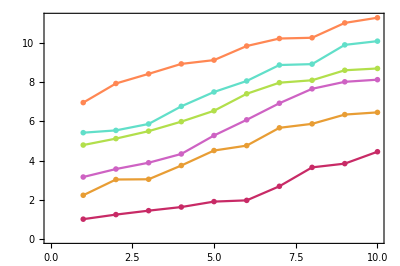

```mathematica
(*filled marker which picks up the PlotStyle automatically*)fm[name_,size_: 4]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

SeedRandom[25] (*for reproducibility*)
ListPlot[Table[Accumulate@RandomReal[1,10]+i,{i,6}],PlotMarkers->fm/@{"Triangle","LeftTriangle","Diamond","ThreePointedStar","UpTriangleTruncated","Square"},Joined->True,PlotStyle->ColorData[54,"ColorList"]]
```

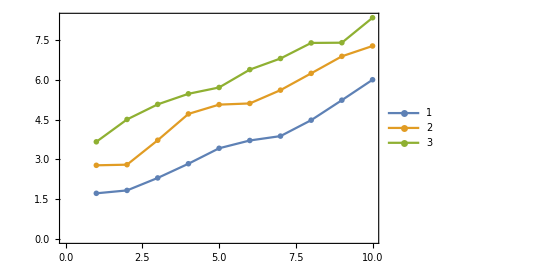

```mathematica
(*empty marker which picks up the PlotStyle automatically,see https://mathematica.stackexchange.com/a/158221/280*)em[name_,size_: 6]:=Graphics[{Dynamic@EdgeForm@Directive[CurrentValue["Color"],JoinForm["Round"],AbsoluteThickness[2],Opacity[1]],Dynamic@FaceForm[White],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}]

SeedRandom[2]
ListPlot[Table[Accumulate@RandomReal[1,10]+i,{i,3}],PlotMarkers->em/@{"Triangle","Square","Diamond"},Joined->True,PlotLegends->PointLegend[Automatic,LegendMarkerSize->{40,25}]]
```

## Load paclets

Setting up the path to the directory of the GitFolder. You’ll need to adapt this in your case!

```mathematica
pacletDirectory ="/Users/amoeri/Documents/Wolfram Mathematica/PyFrac_Mathematica_postprocessing";
PacletDirectoryLoad[pacletDirectory]
```

{/Users/amoeri/Documents/Wolfram Mathematica/PyFrac_Mathematica_postprocessing}

We simply load all the relevant packages. Based on this exercise

```mathematica
<<DescriptionUtilities`
<<NewtonianPulse`
<<RadialScaling`
<<ComputedSolutions`
<<PostProcessRadialPL`
<<RadialPowerLaw`
<<VertexSolutions`
<<rectangularMesh`
```

## General functions

#### Function to get logspaced interval array

```mathematica
logspace[a_,b_,nint_]:=10.0^Range[a,b,(b-a)/(nint-1)] (* Define a function to get a logspaced interval *)
```

#### Function to get the simulation string

```mathematica
(* Create a string according to the exported data *)
simString [int_]:=Module[{sim},
If[int<10,
sim = "DI00"<>IntegerString[int]
, If[int<100,
sim = "DI0"<>IntegerString[int]
,sim ="DI"<> IntegerString[int]]]
];
```

#### Function to load the data from the JSon files

```mathematica
LoadBuoyancyData[Dikes_,dirHost_]:= Module[{iter,sim}, 
For[iter = 1,iter≤ Length[Dikes],iter++,
sim=simString [Dikes[[iter]]];

If[ValueQ[Evaluate[Symbol[sim]]],
Clear[Symbol[sim]];];

Evaluate[Symbol[sim]] =Association[Import[dirHost<>sim<>"_geometrics.json"]];

If[ValueQ[Evaluate[Symbol[sim<>"prop"]]],
Clear[Symbol[sim<>"prop"]];];

If[KeyExistsQ[Symbol[sim],"Vo"],
Evaluate[Symbol[sim<>"prop"]] = {KIc-> √(π/32)Symbol[sim]["Kp"],Ep-> Symbol[sim]["Ep"],Cp-> Symbol[sim]["Cp"],Qo-> Symbol[sim]["Qo"],μp-> Symbol[sim]["mup"],Δγ-> Symbol[sim]["Dgamma"],Vo-> Symbol[sim]["Qo"] * Symbol[sim]["ts"],ts-> Symbol[sim]["ts"],sl-> Symbol[sim]["sources_coordinates"]};,
Evaluate[Symbol[sim<>"prop"]] = {KIc-> √(π/32)Symbol[sim]["Kp"],Ep-> Symbol[sim]["Ep"],Cp-> Symbol[sim]["Cp"],Qo-> Symbol[sim]["Qo"],μp-> Symbol[sim]["mup"],Δγ-> Symbol[sim]["Dgamma"],sl-> Symbol[sim]["sources_coordinates"]};];

If[ValueQ[Evaluate[Symbol[sim<>"fractures"]]],
Clear[Symbol[sim<>"fractures"]];];

Evaluate[Symbol[sim<>"fractures"]] = Association[Import[dirHost<>sim<>"_fractures.json"]];

If[ValueQ[Evaluate[Symbol[sim<>"sections"]]],
Clear[Symbol[sim<>"sections"]];];

Evaluate[Symbol[sim<>"sections"]] = Association[Import[dirHost<>sim<>"_sections.json"]];

];
];
```

## PostProcess functions

#### Function to plot vertical section

```mathematica
sectionPlot[simula_,var_,scaling_] := Module[{sim,nSlices, styling,Legendi, labels, optlegend, divider, plots, opt, iter, limits},

sim=simString[simula];
(* Get the number of sections *)
nSlices =Length["time"/.Symbol[sim<>"sections"]];

(* Define the style of the sections *)
styling =Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/(Length["time"/.Symbol[sim<>"sections"]]-1)]};

(* We generate the legend and the labels, and decide on the dimensional or dimensionless part *)
If[scaling=="hbm",
(* Get the according times contrast *)
Legendi=Round[("time"/.Symbol[sim<>"sections"])/(timeParameters[Symbol[sim<>"prop"],False][[-3]]),0.0001];

(* Generate the labels *)
labels={MaTeX["\\frac{z}{L_{hbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{w}{W_{hbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{p_n}{P_{hbm}} \\text{ [-]}",FontSize->Myfontsize]};

(* generate the legend *)
optlegend={PlotLegends->LineLegend["Rainbow",MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\frac{t}{t_{rmbm}} \\text{ [-]}"},FontSize->Myfontsize]]};

(* Get the length and opening scale *)
(* Note the 10^3 is needed because the unit of the extracted opening is [mm] *)
divider = {Lstarh/.vertexScaling["BMh",Symbol[sim<>"prop"],t,False],
10^3 wstar/.vertexScaling["BMh",Symbol[sim<>"prop"],t,False],
10^-6 pstar/.vertexScaling["BMh",Symbol[sim<>"prop"],t,False]};
,
If[scaling== "tbm",
(* Get the according density contrast *)
Legendi=Round[("time"/.Symbol[sim<>"sections"])/(timeParameters[Symbol[sim<>"prop"],False][[-3]]),0.0001];

(* Generate the labels *)
labels={MaTeX["\\frac{z}{L_{hbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{w}{W_{tbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{p_n}{P_{hbm}} \\text{ [-]}",FontSize->Myfontsize]};

(* generate the legend *)
optlegend={PlotLegends->LineLegend["Rainbow",MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\frac{t}{t_{rmbm}} \\text{ [-]}"},FontSize->Myfontsize]]};

(* Get the length and opening scale *)
(* Note the 10^3 is needed because the unit of the extracted opening is [mm] *)
divider = {Lstarh/.vertexScaling["BMt",Symbol[sim<>"prop"],t,False],
10^3 wstar/.vertexScaling["BMt",Symbol[sim<>"prop"],t,False],
10^-6 pstar/.vertexScaling["BMh",Symbol[sim<>"prop"],t,False]};
,
If[scaling== "hbk",
(* Get the according density contrast *)
Legendi=Round[("time"/.Symbol[sim<>"sections"])/(timeParameters[Symbol[sim<>"prop"],False][[-2]]),0.0001];

(* Generate the labels *)
labels={MaTeX["\\frac{z}{L_{hbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{w}{W_{hbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{p_n}{P_{hbk}} \\text{ [-]}",FontSize->Myfontsize]};

(* generate the legend *)
optlegend={PlotLegends->LineLegend["Rainbow",MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\frac{t}{t_{rkbk}} \\text{ [-]}"},FontSize->Myfontsize]]};

(* Get the length and opening scale *)
(* Note the 10^3 is needed because the unit of the extracted opening is [mm] *)
divider = {Lstarh/.vertexScaling["BKh",Symbol[sim<>"prop"],t,False],
10^3 wstar/.vertexScaling["BKh",Symbol[sim<>"prop"],t,False],
10^-6 pstar/.vertexScaling["BKh",Symbol[sim<>"prop"],t,False]};
,
If[scaling== "tbk",
(* Get the according density contrast *)
Legendi=Round[("time"/.Symbol[sim<>"sections"])/(timeParameters[Symbol[sim<>"prop"],False][[-2]]),0.0001];

(* Generate the labels *)
labels={MaTeX["\\frac{z}{L_{hbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{w}{W_{tbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{p_n}{P_{hbk}} \\text{ [-]}",FontSize->Myfontsize]};

(* generate the legend *)
optlegend={PlotLegends->LineLegend["Rainbow",MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\frac{t}{t_{rkbk}} \\text{ [-]}"},FontSize->Myfontsize]]};

(* Get the length and opening scale *)
(* Note the 10^3 is needed because the unit of the extracted opening is [mm] *)
divider = {Lstarh/.vertexScaling["BKt",Symbol[sim<>"prop"],t,False],
10^3 wstar/.vertexScaling["BKt",Symbol[sim<>"prop"],t,False],
10^-6 pstar/.vertexScaling["BKh",Symbol[sim<>"prop"],t,False]};
,
Legendi=Round[Symbol[sim<>"sections"]["time"],0.0001];(* Get the according times *)

(* Generate the labels *)
labels={MaTeX["z \\text{ [m]}",FontSize->Myfontsize],
MaTeX["w \\text{ [mm]}",FontSize->Myfontsize],
MaTeX["p_n \\text{ [MPa]}",FontSize->Myfontsize]};

(* generate the legend *)
optlegend={PlotLegends->LineLegend["Rainbow",MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\text{(time [s])}"},FontSize->Myfontsize]]};

(* No opening and length-scale to be defined *)
divider = {1,1,1};
];
];
];
];

If[var == "w",
opt={Frame->True,AspectRatio->Automatic(*,FrameLabel->{labels[[1]],labels[[2]]}*),ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};
plots= ConstantArray[0,{nSlices,1}];
For[iter = 1,iter≤ nSlices,iter++,
plots[[iter]]={1/divider[[1]](("w_sampling_coords_"<>ToString[iter-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]),1/divider[[2]](("w_"<>ToString[iter-1])/.Symbol[sim<>"sections"]["w_vert_slice_"])}ᵀ;
];
,
opt={Frame->True,AspectRatio->Automatic(*,FrameLabel->{labels[[1]],labels[[3]]}*),ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,PlotRange-> All};
plots= ConstantArray[0,{nSlices-1,1}];
styling=styling[[2;;]];
For[iter = 2,iter≤ nSlices,iter++,
plots[[iter-1]]={1/divider[[1]](("pn_sampling_coords_"<>ToString[iter-1])/.Symbol[sim<>"sections"]["pn_vert_slice_"]),1/divider[[3]](("pn_"<>ToString[iter-1])/.Symbol[sim<>"sections"]["pn_vert_slice_"])}ᵀ;
];
];
limits ={{-1,Max[plots[[;;,;;,1]]]},{-0.1,1.25 Max[plots[[;;,;;,2]]]}};
Show[ListPlot[plots,Joined->True,optlegend,PlotStyle->styling,PlotRange->limits],opt]
];
```

#### Function to plot colored footprints

With this function one can plot the footprints of a simulation in different colors.

```mathematica
(* Function to get necessary ingredients for colored footprints *)
coloredFootprints[sim_, dimless_:True]:=Module[{LastMesh,stringSim, footprints, styling, bck, divider,iter},
(* Prepare the string to asses the simulation*)
stringSim=simString[sim];

(* Decide if to plot in dimensionless form *)
If[dimless ,divider =Lstarh/.vertexScaling["BKh",Symbol[stringSim<>"prop"],1,False];,
divider = 1;];

(* Generate the mesh of the last footprint *)
LastMesh =meshPlan[0,0,0,0,Symbol[stringSim <>"fractures"]["mesh_info"][[-1]]];

(* We need to order the footprints correctly *)
footprints = ConstantArray[0,{Length[Symbol[stringSim <>"fractures"]["time"]],1}];
For[iter = 1,iter≤ Length[Symbol[stringSim <>"fractures"]["time"]],iter ++,
footprints[[iter]]={Symbol[stringSim <>"fractures"]["fp_x"][[iter]],Symbol[stringSim <>"fractures"]["fp_y"][[iter]]}ᵀ/divider;
];

(* Define the style of footprints *)
styling =Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/Length[Symbol[stringSim <>"fractures"]["time"]]]};

(* Generate the background mesh *)
bck =Graphics[{EdgeForm[{Thin,LightGray}],Transparent,GraphicsComplex[LastMesh["vertexes"]/divider,Polygon[LastMesh["conn"][[1;;]]]]}];

(* Output the style *)
{"Style"-> styling, "Footprints"-> footprints, "Background"-> bck, "LastMesh"-> LastMesh}

];
```

#### Function to plot a footprint with the pressure or width as colormap

With this function one can Plot opening or pressure distribution within the crack

```mathematica
get2DDistributions[sim_,index_,dimless_:"hbk",var_:"w"]:=Module[{stringSim,ind, theMesh, scale, Cdat, graphics, TheColor, iter, pn, Leg, limits,divider,decider,labels, fp},

(* Prepare the string to asses the simulation*)
stringSim=simString[sim];

(* Check if the index is ok *)
If[Abs[index]> Length[Symbol[stringSim <>"fractures"]["time"]],
ind =Sign[index] Length[Symbol[stringSim <>"fractures"]["time"]];
Print["Index was out of range so limiting index was taken instead"];,
ind = index;
];

(* Get the corresponding mesh *)
theMesh =meshPlan[0,0,0,0,Symbol[stringSim <>"fractures"]["mesh_info"][[ind]]];

(* We generate the legend and the labels, and decide on the dimensional or dimensionless part *)
If[dimless=="hbm",
(* Generate the labels *)
labels={MaTeX["\\frac{x}{L_{hbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{z}{L_{hbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{w}{W_{hbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{p_n}{P_{hbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["t/t_{rmbm} \\approx"<>ToString[Round[(Symbol[stringSim <>"fractures"]["time"][[ind]])/(timeParameters[Symbol[stringSim<>"prop"],False][[-3]]),0.0001]]<>"\\text{  [-]}",Magnification->5]};

(* Get the length and opening scale *)
divider = {Lstarh/.vertexScaling["BMh",Symbol[stringSim<>"prop"],t,False],
wstar/.vertexScaling["BMh",Symbol[stringSim<>"prop"],t,False],
pstar/.vertexScaling["BMh",Symbol[stringSim<>"prop"],t,False]};
,
If[dimless== "tbm",
(* Generate the labels *)
labels={MaTeX["\\frac{x}{L_{hbm}} \\text{ [-]}",FontSize->Myfontsize],MaTeX["\\frac{z}{L_{hbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{w}{W_{tbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{p_n}{P_{hbm}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["t/t_{rmbm} \\approx"<>ToString[Round[(Symbol[stringSim <>"fractures"]["time"][[ind]])/(timeParameters[Symbol[stringSim<>"prop"],False][[-3]]),0.0001]]<>"\\text{  [-]}",Magnification->5]};

(* Get the length and opening scale *)
divider = {Lstarh/.vertexScaling["BMt",Symbol[stringSim<>"prop"],t,False],
wstar/.vertexScaling["BMt",Symbol[stringSim<>"prop"],t,False],
pstar/.vertexScaling["BMh",Symbol[stringSim<>"prop"],t,False]};
,
If[dimless== "hbk",
(* Generate the labels *)
labels={MaTeX["\\frac{x}{L_{hbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{z}{L_{hbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{w}{W_{hbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{p_n}{P_{hbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["t/t_{rkbk} \\approx"<>ToString[Round[(Symbol[stringSim <>"fractures"]["time"][[ind]])/(timeParameters[Symbol[stringSim<>"prop"],False][[-2]]),0.0001]]<>"\\text{  [-]}",Magnification->5]};

(* Get the length and opening scale *)
divider = {Lstarh/.vertexScaling["BKh",Symbol[stringSim<>"prop"],t,False],
wstar/.vertexScaling["BKh",Symbol[stringSim<>"prop"],t,False],
pstar/.vertexScaling["BKh",Symbol[stringSim<>"prop"],t,False]};
,
If[dimless== "tbk",
(* Generate the labels *)
labels={MaTeX["\\frac{x}{L_{hbk}} \\text{ [-]}",FontSize->Myfontsize],MaTeX["\\frac{z}{L_{hbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{w}{W_{tbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["\\frac{p_n}{P_{hbk}} \\text{ [-]}",FontSize->Myfontsize],
MaTeX["t/t_{rkbk} \\approx"<>ToString[Round[(Symbol[stringSim <>"fractures"]["time"][[ind]])/(timeParameters[Symbol[stringSim<>"prop"],False][[-2]]),0.0001]]<>"\\text{  [-]}",Magnification->5]};

(* Get the length and opening scale *)
divider = {Lstarh/.vertexScaling["BKt",Symbol[stringSim<>"prop"],t,False],
wstar/.vertexScaling["BKt",Symbol[stringSim<>"prop"],t,False],
pstar/.vertexScaling["BKh",Symbol[stringSim<>"prop"],t,False]};
,
(* Generate the labels *)
labels={MaTeX["x \\text{ [m]}",FontSize->Myfontsize],
MaTeX["z \\text{ [m]}",FontSize->Myfontsize],
MaTeX["w \\text{ [mm]}",FontSize->Myfontsize],
MaTeX["p_n \\text{ [MPa]}",FontSize->Myfontsize],
MaTeX["t \\approx"<>ToString[Round[Symbol[stringSim <>"fractures"]["time"][[ind]],0.0001]]<>"\\text{  [s]}",Magnification->5]};

(* No opening and length-scale to be defined *)
divider = {1,10^-3,10^6};
];
];
];
];

(* Load opening or pressure in function of var *)
If[var == "w",
scale =Rescale[Symbol[stringSim <>"fractures"]["w"][[ind]],{Min[Symbol[stringSim <>"fractures"]["w"][[ind]]],Max[Symbol[stringSim <>"fractures"]["w"][[ind]]]}];
decider =scale;
limits = {Min[Symbol[stringSim <>"fractures"]["w"][[ind]]],Max[Symbol[stringSim <>"fractures"]["w"][[ind]]]};
,
pn=Symbol[stringSim <>"fractures"]["pn"][[ind]];
scale =Rescale[pn,{Min[pn],Max[pn]}];
decider=pn;
limits = {Min[pn],Max[pn]};
];

(* Generate the graphics *)
Cdat =ColorData["SolarColors"]/@scale[[1;;]];
graphics =ConstantArray[0,{Length[scale],1}];
For[iter = 1,iter≤ Length[scale],iter++,
If[decider[[iter]] == 0.,TheColor=Transparent;,TheColor =Cdat[[iter]];];
graphics[[iter]]=Graphics[{EdgeForm[{Thin,Gray}],TheColor,Polygon[(theMesh["vertexes"][[theMesh["conn"][[iter]]]])/divider[[1]]]}];
];

(* Generate the legend *)
If[var ≠ "pn",
Leg =BarLegend[{"SolarColors",limits /divider[[2]]},LegendLayout->"Row",LegendLabel->labels[[3]]];
,
Leg =BarLegend[{"SolarColors",limits /divider[[3]]},LegendLayout->"Row",LegendLabel->labels[[4]]];
];

(* Get the fracutre footprint *)
fp={(Symbol[stringSim <>"fractures"]["fp_x"][[ind]])/divider[[1]],(Symbol[stringSim <>"fractures"]["fp_y"][[ind]])/divider[[1]]}ᵀ;

(* Output data *)
{"Mesh"-> theMesh,"Scale"-> scale,"Graphics"-> graphics,"Index"-> ind, "Legend"-> Leg, "Labels"-> labels, "Fp"-> fp}
];
```

## Dyke Asymptotics and solver (What do I need of this?!)

```mathematica
(* Roper - Lister 2007 *)
```

```mathematica
(* -- some asymptotics *)
```

```mathematica
Ωmk[s_]=√s((1.+(2^(1/3) 3^(5/6))^3 √s)^(1/3) ) ; (* width in the mk / zero buoyancy scaling.... *)
```

```mathematica
rlw[x_]=H; (*  Weertsman  head solution  roper-lister... X = x/ Ks^(2/3)  and H= h/ Ks^(4/3) *)
```

```mathematica
rlw43[x_]=√2(x^(1/4)(x-2)^(3/4))/(2 x^2-2x -1);  (* tail first order correction - Roper-Lister *)
rlwH[x_,Kk_]=rlw[x]HeavisidePi[(x-1)/2]+ Kk^(-4/3) HeavisideTheta[x-2]rlw43[x];
```

### Elasticity discretization

```mathematica
ChebyshevDiscretization[n_]:=Module[{x,s,xmid,u,v,A,B,κ,K,L},
v= Cos[π #/n]&   /@ Range[n];  (* Colocation points in the interval [-1,1] *)
u=  Cos[π ( #-0.5)/n ]& /@ Range[n]; (* The abscissa of the phi  in the interval [-1,1] *)
u=Reverse[u];
v=Reverse[v];
s=((1+u)/(1-u));(* The abscissa of the phi *)
x=((1+v)/(1-v)); (* Colocation points  *)
xmid=x[[1;;-2]]+1/2 Differences[x];(* Mid points *)
A =π/n(1+#)&/@u[[1;;-1]];
B=2A*1/(1-u)^2;
K=1/(4π)*B*1/(#-s)&/@x;(*The elasticity matrix *)
L=Array[If[#1>#2,B[[#2]],If[#2==#1,B[[#2]]+(1/2.5(s[[#1]]^2.5-xmid[[#1]]^2.5)-s[[#1+1]]/1.5(s[[#1]]^1.5-xmid[[#1]]^1.5))/(s[[#1+1]]-s[[#1]]),If[#2==#1+1,(xmid[[#1]]^2.5/2.5-s[[#1]]/1.5(xmid[[#1]]^1.5-0.4*s[[#1]]^1.5))/(s[[#1+1]]-s[[#1]]),0]]]&,{n-1,n}]//Normal;(* The elasticity matrix for the mid point *)

{"K"->K//N,"xmid"->xmid//N,"x"->x//N,"L"->L//N}
]
```

### Lubrication discretization

```mathematica
(* Compile this fction which is the bottle neck *)
```

```mathematica
CLub=Compile[{ {Width,_Real,1}, {x,_Real,1} },
Module[{A,i},
A= DiagonalMatrix[ Flatten[{(-(Width[[1;;-1]])^2)/(x[[2;;-1]]-x[[1;;-2]])}]];
Do[
A[[i,i+1]]=(Width[[i]])^2/(x[[i+1]]-x[[i]]);
,{i,1,Length[Width]-1}];
A],CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

### Residuals

```mathematica
Residuals[pC_?(VectorQ[#,NumericQ]&),ElasMatrix_,L_,xmid_,Npts_,x_,Kstar_]:=Module [{χ1,Ic,Wid,phi,B,A,Width,p},
p=Join[pC,{0.}]//Flatten;
phi=LinearSolve[ElasMatrix,p];
Wid=L.phi;
Width=L.phi+ Kstar xmid^0.5;
 

A=CLub[Width,x];(*TribandMat[Npts,x,Width,χ1];*)
B=ConstantArray[1,Npts-1];
A.pC+Width^2-B 

]
```

### Solver

```mathematica
DykeSolver[Kstar_,n_]:=Module[{μo,μi,λc,m,M,xmid,x,Elas,Lfd,p0, 
ErrorTangent,sol,Width,phi,p,pc,finalresiduals,steps},

M=ChebyshevDiscretization[n];
xmid="xmid"/.M;
x="x"/.M;
Elas="K"/.M;
Lfd="L"/.M; 

(* initial pressure  -- viscosity dominated / zero buoyancy solution as a guess *)
p0=(-2^(1/3)3^(5/6))/(6 √3)(#)^(-1/3)&/@Range[n-1];


Print[" we now start the Non-linear solver"];
{sol,steps}=
Block[{c=0},{FindRoot[ Residuals[pc,Elas,Lfd,xmid,n,x,Kstar ],{{pc,p0 (*,p0 0 -1.,p0 0+0.1 *)}},Method-> "Newton",Jacobian-> "FiniteDifference",AccuracyGoal->8,PrecisionGoal->8, StepMonitor:>c++],c}];


finalresiduals= Residuals[pc/.sol,Elas,Lfd,xmid,n,x,Kstar] ;
 p=Join[pc/.sol,{0.}]//Flatten;

phi=LinearSolve[Elas,p];

Width=Lfd.phi+ Kstar xmid^0.5;

Print[" End of solver after ", steps," steps - norm of residuals : ", Norm[finalresiduals]];

<|"OpeningProfile"-> Transpose[{xmid,Width}],"NetPressureProfile"-> Transpose[{x,p}],"Residuals"-> finalresiduals,"Restar"-> Kstar,"n steps"-> steps|>



]
```

## Generate main Figures of paper and footprints

### Loading all the data

Setting up the path to the directory of the folder containing the json files

```mathematica
dirHost ="/JsonFiles/"; (* Directory of the stored Data *)
```

Here we say which simulations should be loaded and which are stabilized

```mathematica
Dikes = Join[Range[41,51],{55,56},Range[66,76],Range[101,158],Range[160,169]];
stabilized =Join[Range[47,51],{55},Range[66,69],Range[71,76]] ;
```

Load all the data

```mathematica
LoadBuoyancyData[Dikes,dirHost]
```

## Ongoing release case (Q_o, t_s→ ∞)

### Deviation from radial

We plot here the figures for the deviation from the radial fracture of the supplementary material of the Paper. This is followed by the two limiting solutions to validate the limits found by the linear interpolation.

#### Comparison for viscous simulations

Deviation in the viscosity case

{26673.2,8082.69,2449.27,742.196,224.906,68.1525,3.44497×10^7,11245.3}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

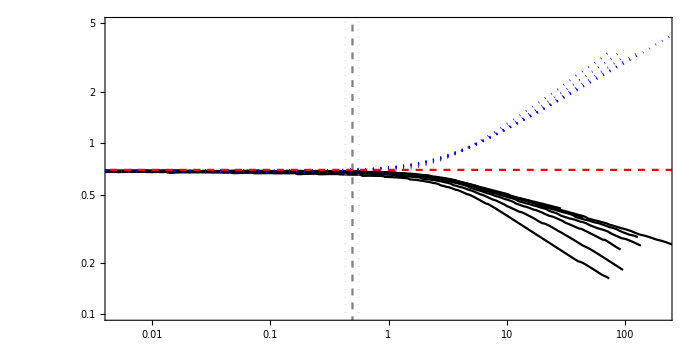

```mathematica
viscosityDikes =Join[Range[41,46],{56,70}];(* selection of dikes to show the toughness dominated transition *)
 ℳ/.vertexScaling["BKh",Symbol[simString[#]<>"prop"],t,False]&/@viscosityDikes
(* Instantiate arrays where the plots of height, and maximum breadth are stored.
The list of errors gives the dimensionless time when the error between the height and breadth exceeds 2.5% *)
breadthPlots= ConstantArray[0,{Length[viscosityDikes],1}];
heightPlots= ConstantArray[0,{Length[viscosityDikes],1}];
errors= ConstantArray[0,{Length[viscosityDikes],1}];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[viscosityDikes],iter++,
(* Get the simulation string *)
sim=simString[viscosityDikes[[iter]]];

(* Get the dimensionless time *)
time=Symbol[sim]["time"]/timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]];

(* Get the normalized plot of the maximum breadth *)
breadthPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["max_breadth"][[1]]/(2 Lstar/.vertexScaling["M",Symbol[ToString[sim]<>"prop"],t]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->Black,
PlotRange->{{5 10^-3,200},{0.1,5}}];

(* Get the normalized plot of the height *)
heightPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["height"][[1]]/(2 Lstar/.vertexScaling["M",Symbol[ToString[sim]<>"prop"],t]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dotted,Blue}];

(* Get the point where deviation takes place *)
errors[[iter]] = Position[Abs[(Symbol[sim]["height"][[1]]/(Lstar/.vertexScaling["M",Symbol[ToString[sim]<>"prop"],t])-Symbol[sim]["max_breadth"][[1]]/(Lstar/.vertexScaling["M",Symbol[ToString[sim]<>"prop"],t]))/(Symbol[sim]["height"][[1]]/(Lstar/.vertexScaling["M",Symbol[ToString[sim]<>"prop"],t]))]*100,_?(#≥2.5&)][[1,1]];
errors[[iter]] = time[[errors[[iter]]]];

];

(* We print the mean and the standard deviation of the dimensionless deviation time *)
MaTeX["\\textrm{The mean of the dimenisinless deviation time is:}",FontSize->Myfontsize]
MaTeX[ "\\overline{t_{T}/t_{rmbm}} = "<>ToString[Mean[errors]],FontSize->Myfontsize]
MaTeX["\\textrm{with a standard deviation of:}",FontSize->Myfontsize]
MaTeX[ "\\sigma\\left(\\overline{t_{T}/t_{rmbm}}\\right) = "<>ToString[StandardDeviation[errors]],FontSize->Myfontsize]
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{rmbm}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{h(t)\\vert\\vert\\underset{z}{\\text{max}}\\left\\{b\\left(z,t\\right)\\right\\}}{L_{m}(t)}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};
Show[breadthPlots,
heightPlots,
ListLogLogPlot[{{Mean[errors],10^-6},{Mean[errors],4.5 10^5}},Joined->True,PlotStyle->{Gray,Dashed}],
ListLogLogPlot[{{Mean[errors]+StandardDeviation[errors],10^-6},{Mean[errors]+StandardDeviation[errors],4.5 10^5}},Joined->True,PlotStyle->{LightGray,Dotted}],
ListLogLogPlot[{{Mean[errors]-StandardDeviation[errors],10^-6},{Mean[errors]-StandardDeviation[errors],4.5 10^5}},Joined->True,PlotStyle->{LightGray,Dotted}],
ListLogLogPlot[{{10^-4,FractureLength/.injectionVertexSolutions["M",{},.1,t,False]},{10^4,FractureLength/.injectionVertexSolutions["M",{},.1,t,False]}},Joined->True,PlotStyle->{Red,Dashed}],
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[viscosityDikes, breadthPlots, heightPlots,errors, sim, time]
Clear[xlabel, ylabel, opt, iter]
```

The plot shows the height and maximum breadth normalized by the characterstic toughnees length-scale L_m(t) in function of the dimensionless transition time t/t_mb. The red dashed line representes the viscosity solution which we approximate with sufficient precision. The dark gray vertical line is the mean where deviaiton takes place and light gray dotted lines are the upper and lower value including standard deviation.

#### Comparison for toughness simulations

Deviation in the toughness case

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

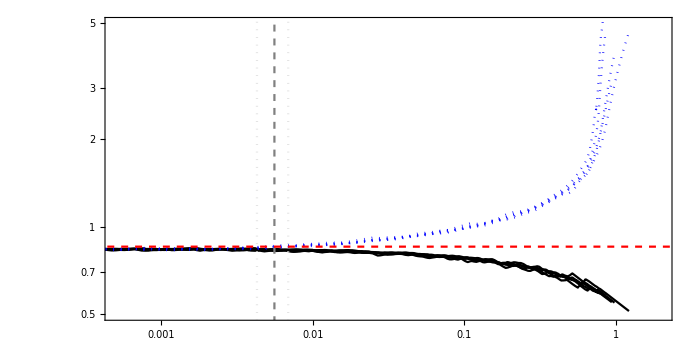

```mathematica
toughnessDikes =Join[{67},Range[71,74]];(* selection of dikes to show the toughness dominated transition *)
 
(* Instantiate arrays where the plots of height, and maximum breadth are stored.
The list of errors gives the dimensionless time when the error between the height and breadth exceeds 2.5% *)
breadthPlots= ConstantArray[0,{Length[toughnessDikes],1}];
heightPlots= ConstantArray[0,{Length[toughnessDikes],1}];
errors= ConstantArray[0,{Length[toughnessDikes],1}];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[toughnessDikes],iter++,
(* Get the simulation string *)
sim=simString[toughnessDikes[[iter]]];

(* Get the dimensionless time *)
time=Symbol[sim]["time"]/timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]];

(* Get the normalized plot of the maximum breadth *)
breadthPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["max_breadth"][[1]]/(2 Lstar/.vertexScaling["K",Symbol[ToString[sim]<>"prop"],t]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->Black,
PlotRange->{{5 10^-4,2},{0.5,5}}];

(* Get the normalized plot of the height *)
heightPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["height"][[1]]/(2 Lstar/.vertexScaling["K",Symbol[ToString[sim]<>"prop"],t]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dotted,Blue}];

(* Get the point where deviation takes place *)
errors[[iter]] = Position[Abs[(Symbol[sim]["height"][[1]]/(Lstar/.vertexScaling["K",Symbol[ToString[sim]<>"prop"],t])-Symbol[sim]["max_breadth"][[1]]/(Lstar/.vertexScaling["K",Symbol[ToString[sim]<>"prop"],t]))/(Symbol[sim]["height"][[1]]/(Lstar/.vertexScaling["K",Symbol[ToString[sim]<>"prop"],t]))]*100,_?(#≥2.5&)][[1,1]];
errors[[iter]] = time[[errors[[iter]]]];

];

(* We print the mean and the standard deviation of the dimensionless deviation time *)
MaTeX["\\textrm{The mean of the dimenisinless deviation time is:}",FontSize->Myfontsize]
MaTeX[ "\\overline{t_{T}/t_{rkbk}} = "<>ToString[Mean[errors]],FontSize->Myfontsize]
MaTeX["\\textrm{with a standard deviation of:}",FontSize->Myfontsize]
MaTeX[ "\\sigma\\left(\\overline{t_{T}/t_{rkbk}}\\right) = "<>ToString[StandardDeviation[errors]],FontSize->Myfontsize]
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{rkbk}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{h(t)\\vert\\vert\\underset{z}{\\text{max}}\\left\\{b\\left(z,t\\right)\\right\\}}{L_{rk}(t)}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};
Show[breadthPlots,
heightPlots,
ListLogLogPlot[{{Mean[errors],10^-6},{Mean[errors],4.5 10^5}},Joined->True,PlotStyle->{Gray,Dashed}],
ListLogLogPlot[{{Mean[errors]+StandardDeviation[errors],10^-6},{Mean[errors]+StandardDeviation[errors],4.5 10^5}},Joined->True,PlotStyle->{LightGray,Dotted}],
ListLogLogPlot[{{Mean[errors]-StandardDeviation[errors],10^-6},{Mean[errors]-StandardDeviation[errors],4.5 10^5}},Joined->True,PlotStyle->{LightGray,Dotted}],
ListLogLogPlot[{{10^-4,FractureLength/.injectionVertexSolutions["K",{},.1,t,False]},{10,FractureLength/.injectionVertexSolutions["K",{},.1,t,False]}},Joined->True,PlotStyle->{Red,Dashed}],
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[toughnessDikes, breadthPlots, heightPlots,errors, sim, time]
Clear[xlabel, ylabel, opt, iter]
```

The plot shows the height and maximum breadth normalized by the characterstic toughnes length-scale L_k(t) in function of the dimensionless transition time t/t_kb. The red dashed line representes the toughness solution which we approximate with sufficient precision. The dark gray vertical line is the mean where deviaiton takes place and light gray dotted lines are the upper and lower value including standard deviation.

#### Deviation in the general case

Here the figure of the supplementary material of the paper is created.

InterpolatingFunction::dmval: Input value {-43.8607} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-43.7837} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-43.7068} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {25.2956} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

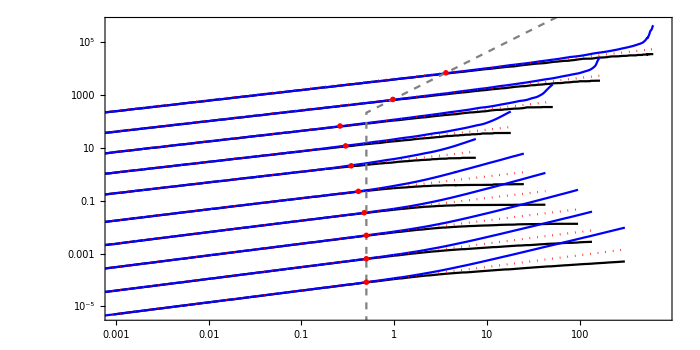

```mathematica
selectedDikes = Join[{41,43,45,47,49},Range[72,76]];(* selection of dikes to show the transition *)
 
(* Instantiate arrays where the plots of height, breadth and semi-analytical MK edge solution are stored. The list of theoretical deviation theorDev gives the points evaluated *)
heightPlots= ConstantArray[0,{Length[selectedDikes],1}];
breadthPlots= ConstantArray[0,{Length[selectedDikes],1}];
semiaPlots = ConstantArray[0,{Length[selectedDikes],1}];
theorDev = ConstantArray[0,{Length[selectedDikes],2}];

(* Function of the transition time *)
tTrans[Mb_] :=If[Mb ≤ 3.16 10^-4,5 10^-3 Mb^(-4/7),0.5]

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[selectedDikes],iter++,
(* Get the simulation string *)
sim=simString[selectedDikes[[iter]]];

(* Store the dimensionless time *)
time=Symbol[sim]["time"]/timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]];

(* Calculate the point of theoretical deviation *)
theorDev[[iter,1]] = timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]/timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]];
theorDev[[iter,2]] =((FractureLength/.edgeSolution["MK",1.,(theorDev[[iter,1]]/( (ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],1])^(27/14))),.1][[1]])( √(32/π))^-4)[[2]];

(* Generate the plot of the normalized maximum breadth *)
breadthPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["max_breadth"][[1]]/(2 Lstar/. transitionMKScales[Symbol[ToString[sim]<>"prop"],False])}ᵀ,Joined->True,PlotStyle->Black,
PlotRange->{{10^-3,7.5 10^2},{5 10^-6,5 10^5}}];

(* Generate the plot of the normalized height of the fracture *)
heightPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["height"][[1]]/(2  Lstar/. transitionMKScales[Symbol[ToString[sim]<>"prop"],False])}ᵀ,Joined->True,PlotStyle->Blue];

(* Generate the plot of the MK-Edge semianalytical solution *)
semiaPlots[[iter]] = ListLogLogPlot[{time,((FractureLength/.edgeSolution["MK",1.,(t/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]] (ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],1])^(27/14)))/.{t->Symbol[sim]["time"]},.1][[1]])[[;;,2]]( √(32/π))^-4)}ᵀ,Joined->True,PlotStyle->{Red,Dotted}];

];

(* Add limits to the funciton *)
simpDev={{0.5,10^-8},
{tTrans[3.16 10^-4],((FractureLength/.edgeSolution["MK",1.,(tTrans[3.16 10^-4]/( (3.16 10^-4(√(32/π))^(-14/3))^(27/14)))//N,.1][[1]])( √(32/π))^-4)[[2]]},{tTrans[10^-15],((FractureLength/.edgeSolution["MK",1.,(tTrans[10^-15]/( (10^-15(√(32/π))^(-14/3))^(27/14)))//N,.1][[1]])( √(32/π))^-4)[[2]]}};

(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{rmbm}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{h(t)\\vert\\vert\\underset{z}{\\text{max}}\\left\\{b\\left(z,t\\right)\\right\\}}{L_{rmrk}}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};
(* Create the figure *)
Show[breadthPlots,
heightPlots,
semiaPlots,
ListLogLogPlot[SortBy[simpDev,#2],Joined->True,PlotStyle->{Gray,Dashed}],
ListLogLogPlot[theorDev,PlotStyle-> Red,PlotMarkers->fm["SixfoldCross",7]],
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[selectedDikes, breadthPlots, heightPlots, semiaPlots,theorDev, sim, time, simpDev, tTrans]
Clear[xlabel, ylabel, opt, iter]
```

The note of the function appears because the beginning of the simulation is out of range (no problem for the range plotted).
The plot shows the height and maximum breadth normalized by the characterstic transition length-scale L_mk in function of the dimensionless transition time t/t_mb. The red dashed line representes the semianalytical solution for zero buoyancy which we approximate with sufficient precision. The dark gray vertical line is a dimensionless time of t/t_mb=1. Red stars give the dimensionless prefactor for the transition expected.

### Evaluate buoyancy-driven limits

We evaluate the velocity profiles of the simulations inferred from our simulations. The velocity in the case of a classical dike should become constant.

#### Evaluate toughness-head

```mathematica
(* -------- First we plot the evolution of geometrical parameters -------- *)
```

```mathematica
(* Choose the dikes to plot *)
toughnessDikes =Join[{50,51,55},Range[66,68],Range[71,76]];
(* Instantiate arrays where the plots of height, breadth and semi-analytical MK edge solution are stored. The list of theoretical deviation theorDev gives the points evaluated *)
velocities= ConstantArray[0,{Length[toughnessDikes],1}]; (* Array containing the velocities *)
velocitiePlots =ConstantArray[0,{Length[toughnessDikes],1}];
heightPlots =ConstantArray[0,{Length[toughnessDikes],1}];
breadthPlots = ConstantArray[0,{Length[toughnessDikes],1}];
dimViscosity = ConstantArray[0,{Length[toughnessDikes],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/(Length[toughnessDikes]-1)];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[toughnessDikes],iter++,

(* Get the simulation string *)
sim=simString[toughnessDikes[[iter]]];

(* We get the average velocity of the fracture in the buoyant direction *)
dt=Differences[Symbol[sim]["time"]];
dH=Differences[Symbol[sim]["height"][[1]]];
velocities[[iter]] = dH/dt ;

dimViscosity[[iter]] =ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],t,False];

indices = Table[i*15-1,{i,1,Floor[Length[velocities[[iter]]]/15]}];

velocitiePlots[[iter]] =
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),velocities[[iter]][[indices]]/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.1,12.5},{0.02,7}},Joined->True];
heightPlots[[iter]] =ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),Symbol[sim]["height"][[1]][[indices]]/(Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],Symbol[sim]["time"][[indices]],False])}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.001,12.5},{0.05,10}},Joined->True];
breadthPlots[[iter]] =ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),Symbol[sim]["max_breadth"][[1]][[indices]]/(Lstarh/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],Symbol[sim]["time"][[indices]],False])}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{10^-3,12.5},{0.05,1.2}},Joined->True];
];

(* ---------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Plotting the figures >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ---------------------------------------------------------------------------------------- *)

(* --------- We generate the label and the legend for the velocity figure --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{kb} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\dot{H}/\\dot{L_{v}} \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[velocitiePlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),velocities[[iter-1]][[indices]]/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
opt]

(* --------- We generate the label and the legend for the Breadht --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{kb} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{\\underset{y}{\\text{max}}\\left\\{b\\left(y,t\\right)\\right\\}}{L_b}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[breadthPlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),velocities[[iter-1]][[indices]]/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
LogLogPlot[((√(32/π))^(-2/5)2FractureLength/.injectionVertexSolutions["K",DI072prop,.5,(x timeParameters[DI072prop,False][[-2]]),True,False])/( Lstarh/.vertexScaling["BKt",DI072prop,t,False]),{x, 10^-3,5},PlotStyle->{Dotted,Red}],
LogLogPlot[1/π^(1/3),{x,0.75,12.5},PlotStyle->{Dashed, RGBColor[0.28,0.67,0.]}],
opt]

(* --------- We generate the label and the legend for the Height --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{kb} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["H(t)/L_v",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[heightPlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),velocities[[iter-1]][[indices]]/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
LogLogPlot[((√(32/π))^(-2/5)2FractureLength/.injectionVertexSolutions["K",DI072prop,.5,(x timeParameters[DI072prop,False][[-2]]),True,False])/( Lstarv/.vertexScaling["BKt",DI072prop,(x timeParameters[DI072prop,False][[-2]]),False]),{x, 10^-3,1.5},PlotStyle->{Dotted,Red}],
LogLogPlot[((√(32/π))^(-2/5)2FractureLength/.injectionVertexSolutions["K",DI050prop,.5,(x timeParameters[DI050prop,False][[-2]]),True,False])/( Lstarv/.vertexScaling["BKt",DI050prop,(x timeParameters[DI050prop,False][[-2]]),False]),{x, 10^-3,1.5},PlotStyle->{Dotted,Red}],
opt]


(* ----------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Cleaning the notebook >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ---------------------------------------------------------------------------------------- *)
Clear[toughnessDikes, velocities, velocitiePlots, heightPlots, breadthPlots,dimViscosity]
Clear[colors,iter,sim,dt,dH,legendPlot]
Clear[xlabel, ylabel, opt,optlegend,indices]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* -------- Second we plot the sections along the center line x=0 -------- *)
```

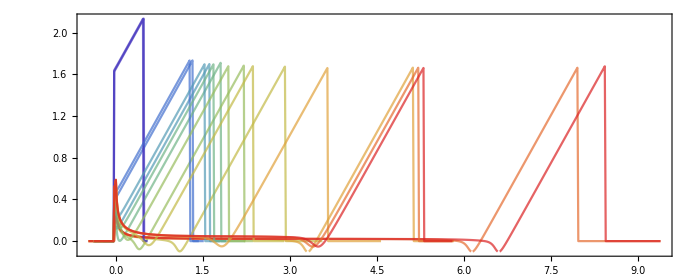

```mathematica
Show[sectionPlot[72,"pn","hbk"],sectionPlot[73,"pn","hbk"]]
```

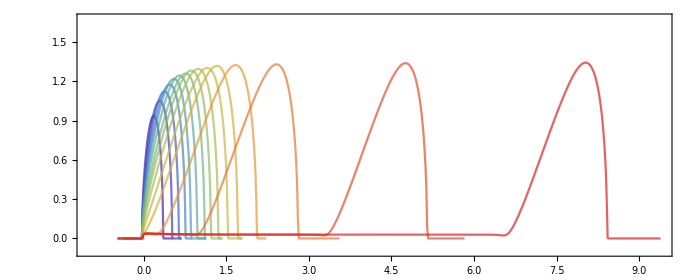

```mathematica
(* Selectino of the dikes to one can plot *)
toughnessDikes =Join[{50,51,55},Range[66,68],Range[71,76]];

dimless = "hbk"; (* Choose how to normalize choices include, "hbm,tbm,hbk,tbk,no" *)

(* Get the simulation string *)
index =-5;
sectionPlot[toughnessDikes[[index]],"w",dimless]
Clear[toughnessDikes,dimless,index]
```

#### Evaluate viscous-head

```mathematica
(* -------- First we plot the evolution of geometrical parameters -------- *)
```

```mathematica
(* Choose the dikes to plot *)
viscousDikes ={41,42,43,44,56,70};

(* Instantiate arrays where the plots of height, breadth and semi-analytical MK edge solution are stored. The list of theoretical deviation theorDev gives the points evaluated *)
velocities= ConstantArray[0,{Length[viscousDikes],1}]; (* Array containing the velocities *)
velocitiePlots =ConstantArray[0,{Length[viscousDikes],1}];
heightPlots =ConstantArray[0,{Length[viscousDikes],1}];
breadthPlots = ConstantArray[0,{Length[viscousDikes],1}];
dimViscosity = ConstantArray[0,{Length[viscousDikes],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/(Length[viscousDikes]-1)];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[viscousDikes],iter++,
(* Get the simulation string *)
sim=simString[viscousDikes[[iter]]];

(* We get the average velocity of the fracture in the buoyant direction *)
dt=Differences[Symbol[sim]["time"]];
dH=Differences[Symbol[sim]["height"][[1]]];
velocities[[iter]] = dH/dt ;

dimViscosity[[iter]] =ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],t,False];

indices = Table[i*15-1,{i,1,Floor[Length[velocities[[iter]]]/15]}];

velocitiePlots[[iter]] =
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]]),velocities[[iter]][[indices]]/(D[ Lstarv/.vertexScaling["BMt",Symbol[ToString[sim]<>"prop"],t,False],t]/.Symbol[ToString[sim]<>"prop"]/.{t-> Symbol[sim]["time"][[indices]]})}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.1,500},{0.1,1.5}}(*{{0.1,500},{0.05,1.5}}*),Joined->True];
heightPlots[[iter]] =ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]]),Symbol[sim]["height"][[1]][[indices]]/(Lstarv/.vertexScaling["BMt",Symbol[ToString[sim]<>"prop"],Symbol[sim]["time"][[indices]],False])}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.1,500},{0.2,5}}(*{{0.1,500},{0.05,5}}*),Joined->True];
breadthPlots[[iter]] =ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]]),Symbol[sim]["max_breadth"][[1]][[indices]]/(Lstarh/.vertexScaling["BMt",Symbol[ToString[sim]<>"prop"],Symbol[sim]["time"][[indices]],False])}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.1,500},{0.5,7.5}}(*{{0.05,500},{0.8,55}}*),Joined->True];
];

(* ---------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Plotting the figures >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ---------------------------------------------------------------------------------------- *)

(* --------- We generate the label and the legend for the velocity figure --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{rmbm} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\dot{h\\left(t\\right)}/\\dot{L_{vbm}\\left(t\\right)} \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{bk} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[velocitiePlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),velocities[[iter-1]][[indices]]/D[ Lstarv/.vertexScaling["BMt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
opt]

(* --------- We generate the label and the legend for the Breadht --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{rmbm} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{\\underset{z}{\\text{max}}\\left\\{b\\left(z,t\\right)\\right\\}}{L_{hbm}}\\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{bk}\\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[breadthPlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),velocities[[iter-1]][[indices]]/D[ Lstarv/.vertexScaling["BMt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
LogLogPlot[(2FractureLength/.injectionVertexSolutions["M",DI041prop,.5,(x timeParameters[DI041prop,False][[-3]]),True,False])/( Lstarh/.vertexScaling["BMt",DI041prop,t,False]),{x, 10^-3,5},PlotStyle->{Dotted,Blue}],
LogLogPlot[parAfter[[1]] x^parAfter[[2]],{x,1,10^5},PlotStyle->{Red,Dotted}],
opt]

(* --------- We generate the label and the legend for the Height --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{rmbm} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["h\\left(t\\right)/L_{vbm}\\left(t\\right)\\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{bk}\\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[heightPlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),velocities[[iter-1]][[indices]]/D[ Lstarv/.vertexScaling["BMt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
LogLogPlot[(2FractureLength/.injectionVertexSolutions["M",DI041prop,.5,(x timeParameters[DI041prop,False][[-3]]),True,False])/( Lstarv/.vertexScaling["BMt",DI041prop,(x timeParameters[DI041prop,False][[-3]]),False]),{x, 10^-3,5},PlotStyle->{Dotted,Blue}],
opt]

(* ----------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Cleaning the notebook >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ---------------------------------------------------------------------------------------- *)
(*Clear[viscousDikes, velocities, velocitiePlots, heightPlots, breadthPlots,dimViscosity]
Clear[colors,iter,sim,dt,dH,legendPlot]
Clear[xlabel, ylabel, opt,optlegend,indices]*)
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
dimViscosity
```

{26673.2,8082.69,2449.27,742.196,3.44497×10^7,11245.3}

```mathematica
beval = ({DI041["time"]/(timeParameters[DI041prop,False][[-3]]),DI041["max_breadth"][[1]]/(Lstarh/.vertexScaling["BMt",DI041prop,DI041["time"],False])}ᵀ
)[[-1500;;]];Show[ListLogLogPlot[{DI041["time"]/(timeParameters[DI041prop,False][[-3]]),DI041["max_breadth"][[1]]/(Lstarh/.vertexScaling["BMt",DI041prop,DI041["time"],False])}ᵀ,  PlotStyle->{Dashed,Blue},PlotMarkers->{"◦"},PlotRange->{{0.1,500},{0.5,7.5}}(*{{0.05,500},{0.8,55}}*),Joined->True],
ListLogLogPlot[beval,  PlotStyle->{Dashed,Red},PlotMarkers->{"◦"},PlotRange->{{0.1,500},{0.5,7.5}}(*{{0.05,500},{0.8,55}}*),Joined->True]]
```

-Graphics-

```mathematica
(* ------ Getting the power law for a transition after ------ *)
fitAfter=LinearModelFit[Log10[beval],x,x];
parAfter={10^fitAfter[[1,2,1]]};
AppendTo[parAfter,fitAfter[[1,2,2]]]
Rationalize[fitAfter[[1,2,2]],0.001]
2/9//N
8/35//N
```

{1.68824,0.228517}

8/35

0.222222

0.228571

```mathematica
(* -------- Second we plot the sections along the center line x=0 -------- *)
```

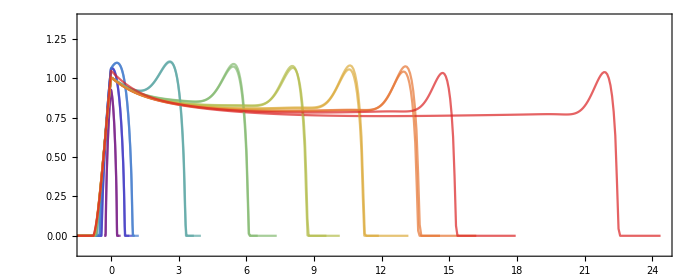

```mathematica
Show[sectionPlot[70,"w","hbm"],sectionPlot[56,"w","hbm"]]
```

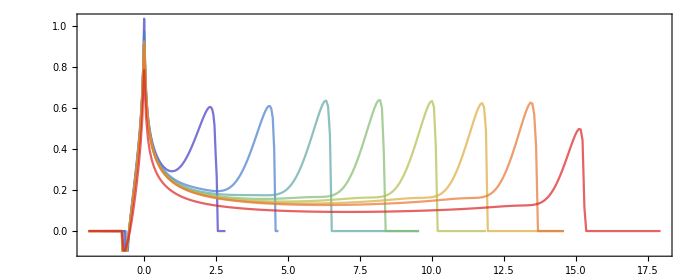

```mathematica
(* Selectino of the dikes to one can plot *)
viscousDikes ={41,42,43,44,56,70};

dimless = "hbm"; (* Choose how to normalize choices include, "hbm,tbm,hbk,tbk,no" *)

(* Get the simulation string *)
index =-2;
sectionPlot[viscousDikes[[index]],"pn",dimless];
Clear[viscousDikes,dimless,index]
```

### Prefactor on stabilized breadth

We create Figure 2 of the Paper!

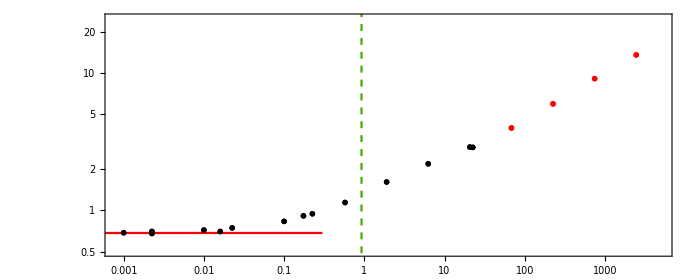

```mathematica
(* Only the simulations with constant injection rate are chosen *)
injDikes =Join[Range[41,51],{55,56},Range[66,76]];

(* ------ Getting the prefactor on the breadth ------ *)
maxBreadths = ConstantArray[0,{Length[injDikes],2}];(* Variable containing the value of Subscript[ℳ, b] and of the maximum breadth *)
plotInfo = ConstantArray[0,{Length[injDikes],2}];
(* Storing the markers to have them different for stabilized and non-stabilized fractures *)

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[injDikes],iter++,
(* Get the simulation string *)
sim=simString[injDikes[[iter]]];

(* Decide which marker type to use *)
If[MemberQ[stabilized,injDikes[[iter]]],
plotInfo[[iter,1]]  = Black;
plotInfo[[iter,2]] =fm["Disk",7];
,
plotInfo[[iter,1]]  =Red;
plotInfo[[iter,2]]  =fm["SixfoldCross",7];];

(* Save the viscosity in the head Subscript[ℳ, b] from scaling paclet *)
maxBreadths[[iter,1]] =ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],1,False];
(* Save the scaled maximum breadth *)
maxBreadths[[iter,2]] = Max[Symbol[sim]["max_breadth"][[1]]]/(Lstarh/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],1,False]);
];

(* Power-law for transition during the release *)
(* Transform the solution to plot it *)
maxBreadths={#}&/@maxBreadths;
(* Define some plot options *)
xlabel=MaTeX["\\mathcal{M}_{bk}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{\\underset{y,t}{\\text{max}}\\left\\{b\\left(y,t\\right)\\right\\}}{L_b}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio-> Automatic,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};
(* Create the figure *)
Show[ListLogLogPlot[maxBreadths,PlotStyle->plotInfo[[;;,1]],PlotMarkers->plotInfo[[;;,2]],PlotRange->{{8 10^-4,5 10^3},{0.5,25}}],LogLogPlot[1/π^(1/3),{x,7.5 10^-6,0.3},PlotStyle->{Red}],ListLogLogPlot[{{(24 2^(5/6))/π^(4/3)α^(5/3) /.{α-> 0.25}//N,0.3 },{(24 2^(5/6))/π^(4/3)α^(5/3) /.{α-> 0.25}//N,100}},Joined->True,PlotStyle->{Dashed, RGBColor[0.28,0.67,0.]}],
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[injDikes, maxBreadths, plotInfo, sim, iter]
Clear[xlabel, ylabel, opt]
```

The plot shows maximum breadth normalized by the characterstic buoyancy length-scale L_b in function of the dimensionless viscosity in the head ℳ_b. The red dashed line representes the toughness solution from Germanovich et al., (2014) which we validate for ℳ_b≤ 0.1. The green vertical line is the limiting value for stabilization from Germanovich et al., (2014) and the gray vertical line represents a value of ℳ_b= 1. Black dots show a stabilized breadth red crosses have no stabilization.

### Compare to Germanovich et al., (2014)

```mathematica
(* We select some of the simulations for visualization *)
selDikes =Join[{51,66,67,68},Range[71,76]];

(* Instantiate arrays where the plots of height, breadth and semi-analytical MK edge solution are stored. The list of theoretical deviation theorDev gives the points evaluated *)
mbs= ConstantArray[0,{Length[selDikes],1}];
openingPlots = ConstantArray[0,{Length[selDikes],1}];
pressurePlots = ConstantArray[0,{Length[selDikes],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/Length[selDikes]];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[selDikes],iter++,
(* Get the simulation string *)
sim=simString[selDikes[[iter]]];

(* Get the head viscosity *)
mbs[[iter]]=ℳ/.vertexScaling["BKh",Symbol[sim<>"prop"],t,False];

(* We generate the plots of all sections *)
intPlots = ConstantArray[0,{Length[Symbol[sim<>"sections"]["time"]],1}];
intPlotsP= ConstantArray[0,{Length[Symbol[sim<>"sections"]["time"]],1}];
For[iter2 = 1,iter2≤ Length[Symbol[sim<>"sections"]["time"]],iter2++,
coords =Reverse[("w_sampling_coords_" <>ToString[iter2-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]];
tipDist =coords[[Position[Reverse[("w_"<>ToString[iter2-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]],_?(#≠0&),1,1][[1,1]]]];
intPlots[[iter2]]=ListPlot[{(- 1)/(Lstarh/.vertexScaling["BKh",Symbol[sim<>"prop"],t,False])((("w_sampling_coords_" <>ToString[iter2-1])/.Symbol[sim<>"sections"]["w_vert_slice_"])-tipDist ),( (("w_"<>ToString[iter2-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]))/(1000 wstar/.vertexScaling["BKh",Symbol[sim<>"prop"],t,False])}ᵀ,PlotRange->All,PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},Joined->True];
intPlotsP[[iter2]]=ListPlot[{(- 1)/(Lstarh/.vertexScaling["BKh",Symbol[sim<>"prop"],t,False])((("pn_sampling_coords_" <>ToString[iter2-1])/.Symbol[sim<>"sections"]["pn_vert_slice_"])-tipDist),((("pn_"<>ToString[iter2-1])/.Symbol[sim<>"sections"]["pn_vert_slice_"]))10^6/( pstar/.vertexScaling["BKh",Symbol[sim<>"prop"],t,False])}ᵀ,PlotRange->All,PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},Joined->True];
];

(* Only select the last three --> Well buoyant*)
openingPlots[[iter]] = intPlots[[-3;;]];
pressurePlots[[iter]] = intPlotsP[[-3;;]];
];

(* Loading the data of the GeGa plots *)
gegaOpening =Import[NotebookDirectory[]<>"DataToLoad/GeGaOpening.xlsx"][[1]];
gegaOpening[[;;,1]]=-(gegaOpening[[;;,1]]-1.3935)*0.34139203162764786;
gegaOpening[[;;,2]]=gegaOpening[[;;,2]] π^(1/3) ;

gegaPressure =Import[NotebookDirectory[]<>"DataToLoad/GeGaPressure.xlsx"][[1]]
gegaPressure[[;;,1]]=-(gegaPressure[[;;,1]]-1.3935)*0.34139203162764786;
gegaPressure[[;;,2]]=gegaPressure[[;;,2]] 2/π^(1/3) ;
fit =LinearModelFit[gegaPressure,x,x][[1,2]];
fit

(* --------- We generate the label and the legend for the opening figure --------- *)
legendPlot=Round[Sort[mbs],0.00001];
xlabel=MaTeX["\\xi/L_{hbk} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\omega/W_{hbk} \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->{{-0.1,3},{-0.1,1.75}},FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[mbs]]],MaTeX[#,FontSize->Myfontsize-2]&/@legendPlot,LegendLabel->Column@MaTeX[{"\\mathcal{M}_{bk} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure of the opening --------- *)
Show[openingPlots,
ListPlot[{{1,1},{1,1}}ᵀ,PlotStyle->{Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
ListPlot[{{1.7718246441474925,-0.2},{1.7718246441474925,2.5} },Joined->True,PlotStyle->{Red,Dashed}],
ListPlot[gegaOpening,Joined->True,PlotStyle->{Thickness[.0075],Red}],
Plot[0,{x,-.5,5.5},PlotStyle->{Gray}],
opt]

(* --------- We generate the label and the legend for the pressure figure --------- *)
legendPlot=Round[Sort[mbs],0.00001];
xlabel=MaTeX["\\xi/L_{hbk} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["p_n/P_{hbk} \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->{{-0.1,3},{-0.15,1.8}},FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[mbs]]],MaTeX[#,FontSize->Myfontsize-2]&/@legendPlot,LegendLabel->Column@MaTeX[{"\\mathcal{M}_{bk} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure of the opening --------- *)
Show[pressurePlots,
ListPlot[{{1,1},{1,1}}ᵀ,PlotStyle->{Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
ListPlot[{{1.7718246441474925,-0.2},{1.7718246441474925,2.5} },Joined->True,PlotStyle->{Red,Dashed}],
Plot[0,{x,-.5,5.5},PlotStyle->{Gray}],
(*Plot[0.34048104487598174(4.7935-x/0.34048104487598174)/.{α-> 0.25},{x,0,5.19*0.34048104487598174},PlotStyle->{Thick,Red}],*)
Plot[fit[[1]] +x fit[[2]],{x,0,5.19*0.34048104487598174},PlotStyle->{Thickness[.0075],Red}],
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[selDikes,sim,openingPlots,intPlots, intPlotsP, pressurePlots,iter,opt,optlegend]
Clear[iter2,mbs,colors]
Clear[xlabel,ylabel,coords,tipDist,legendPlot]
Clear[gegaOpening,gegaPressure,fit]
```

{{0.622414,1.},{-3.37389,0.00956938}}

{1.62653,-0.991348}

-Graphics-

-Graphics-

### Compare to Roper and Lister, (2005;2007)

```mathematica
(* We select some of the simulations for visualization *)
selDikes ={68,69,72,73,74,76};

(* Instantiate arrays where the plots of height, breadth and semi-analytical MK edge solution are stored. The list of theoretical deviation theorDev gives the points evaluated *)
kappaRoLi = ConstantArray[0,{Length[selDikes],1}];
openingPlots = ConstantArray[0,{Length[selDikes],1}];
pressurePlots = ConstantArray[0,{Length[selDikes],1}];
velocityPlots = ConstantArray[0,{Length[selDikes],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/Length[selDikes]];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[selDikes],iter++,
(* Get the simulation string *)
sim=simString[selDikes[[iter]]];

(* We get velocity of the fracture in the buoyant direction *)
dt=Differences[Symbol[sim]["time"]]; (* Time steps *)
dH=Differences[Symbol[sim]["height"][[1]]]; (* Height increment *)
velocities= dH/dt ;

(* Get a mean velocity from last 100 time steps *)
velBar = Mean[velocities[[-100;;]]];

(* Generate the plot of the velocities *)
velocityPlots[[iter]] = ListLogLogPlot[{(Symbol[sim]["time"][[2;;]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),velocities/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ,PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},Joined->True,PlotRange->{{0.1,100},{0.075,2}}];

(* Now we can calculate the 2D injection rate as breadth times velocity *)
Q2D = D[ Lstarv/.vertexScaling["BKt",{},t,False],t] (wstar/.vertexScaling["BKt",{},t,False])/.{Kp-> KIc}/.Symbol[sim<>"prop"];
(*Q2D =(Qo/.Symbol[sim<>"prop"])/ Symbol[sim]["max_breadth"][[1,-1]];*)

(* Get the scales of the RoLiPaper *)
LstarRoLi =1/2(Ep^(1/2)Q2D^(1/6)μp^(1/6))/Δγ^(2/3)/.Symbol[sim<>"prop"];
WstarRoLi =1/2 (Q2D^(1/3)μp^(1/3))/Δγ^(1/3)/.Symbol[sim<>"prop"];
PstarRoLi =1/2 Ep^(1/2)Q2D^(1/6)μp^(1/6)Δγ^(1/3)/.Symbol[sim<>"prop"];
kappaRoLi[[iter]] =1/2 √(32/π)KIc/(Ep^(3/4)μp^(1/4)Q2D^(1/4))/.Symbol[sim<>"prop"];

(* We generate the plots of all sections *)
intPlots = ConstantArray[0,{Length[Symbol[sim<>"sections"]["time"]],1}];
intPlotsP= ConstantArray[0,{Length[Symbol[sim<>"sections"]["time"]],1}];
For[iter2 = 1,iter2≤ Length[Symbol[sim<>"sections"]["time"]],iter2++,
coords =Reverse[("w_sampling_coords_" <>ToString[iter2-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]];
tipDist =coords[[Position[Reverse[("w_"<>ToString[iter2-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]],_?(#≠0&),1,1][[1,1]]]];
intPlots[[iter2]]=ListPlot[{(- 1)/(LstarRoLi kappaRoLi[[iter]]^(2/3))((("w_sampling_coords_" <>ToString[iter2-1])/.Symbol[sim<>"sections"]["w_vert_slice_"])-tipDist),( 1/2(("w_"<>ToString[iter2-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]))/(WstarRoLi 1000 kappaRoLi[[iter]]^(4/3))}ᵀ,PlotRange->All,PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},Joined->True];
intPlotsP[[iter2]]=ListPlot[{-1/(LstarRoLi kappaRoLi[[iter]]^(2/3))((("pn_sampling_coords_" <>ToString[iter2-1])/.Symbol[sim<>"sections"]["pn_vert_slice_"])-tipDist),((("pn_"<>ToString[iter2-1])/.Symbol[sim<>"sections"]["pn_vert_slice_"]))10^6/( PstarRoLi kappaRoLi[[iter]]^(2/3))}ᵀ,PlotRange->All,PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},Joined->True];
];

(* Only select the last three --> Well buoyant*)
openingPlots[[iter]] = intPlots[[-3;;]];
pressurePlots[[iter]] = intPlotsP[[-3;;]];
];

(* --------- We generate the label and the legend for the opening figure --------- *)
legendPlot=Round[Sort[kappaRoLi],0.0001];
xlabel=MaTeX["\\xi/L_{RoLi} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\omega/W_{RoLi} \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->All(*,FrameLabel->{xlabel,ylabel}*),ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[kappaRoLi]]],MaTeX[#,FontSize->Myfontsize-2]&/@legendPlot,LegendLabel->Column@MaTeX[{"\\mathcal{K}_{RoLi} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure of the opening --------- *)
Show[openingPlots,
ListPlot[{(-2 2^(2/3))/(LstarRoLi kappaRoLi[[iter-1]]^(2/3))((("w_sampling_coords_" <>ToString[iter2-2])/.Symbol[sim<>"sections"]["w_vert_slice_"])-tipDist),(  2^(4/3)(("w_"<>ToString[iter2-2])/.Symbol[sim<>"sections"]["w_vert_slice_"]))/(WstarRoLi 1000 kappaRoLi[[iter-1]]^(4/3))}ᵀ,PlotRange->All,PlotStyle->{Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
Plot[ rlwH[x,8.9]  ,{x,0.,5.5},PlotStyle->Red],
(*Plot[{  2(1/2^(2/3)-x)^(3/2)√x    (*, Ωmk[x]*)},{x,0.,2^(-2/3)}],*)
PlotRange->{{-.05,5},{0,1.75}},opt]

(* --------- We generate the label and the legend for the pressure figure --------- *)
legendPlot=Round[Sort[kappaRoLi],0.0001];
xlabel=MaTeX["\\xi/L_{RoLi} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\Pi/P_{RoLi} \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->All(*,FrameLabel->{xlabel,ylabel}*),ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[kappaRoLi]]],MaTeX[#,FontSize->Myfontsize-2]&/@legendPlot,LegendLabel->Column@MaTeX[{"\\mathcal{K}_{RoLi} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure of the opening --------- *)
Show[pressurePlots,
ListPlot[{(-2 2^(2/3))/(LstarRoLi kappaRoLi[[iter-1]]^(2/3))((("w_sampling_coords_" <>ToString[iter2-2])/.Symbol[sim<>"sections"]["w_vert_slice_"])-tipDist),(  2^(4/3)(("w_"<>ToString[iter2-2])/.Symbol[sim<>"sections"]["w_vert_slice_"]))/(WstarRoLi 1000 kappaRoLi[[iter-1]]^(4/3))}ᵀ,PlotRange->All,PlotStyle->{Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
Plot[{ 3/2 - x  },{x,0.,5},PlotStyle->{Thick,Red}],
Plot[0,{x,-.5,5.5},PlotStyle->{Gray}],
PlotRange->{{-.05,5},{-0.15,2.5}},opt]

(* --------- We generate the label and the legend for the velocity figure --------- *)
legendPlot=Round[Sort[kappaRoLi],0.0001];
xlabel=MaTeX["t/t_{kb} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\dot{H}/\\dot{L_{v}} \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[kappaRoLi]]],MaTeX[#,FontSize->Myfontsize-2]&/@legendPlot,LegendLabel->Column@MaTeX[{"\\mathcal{K}_{RoLi} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure of the velocities --------- *)
Show[velocityPlots,
ListLogLogPlot[{(Symbol[sim]["time"][[2;;]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),velocities/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ,PlotStyle->{Dashed,colors[[iter-1]]},Joined->True,PlotRange->{{0.1,100},{0.075,2}},optlegend],opt
]


(* We then clear the variables to have a clean working notebook *)
Clear[selDikes,sim,openingPlots,intPlots, intPlotsP, pressurePlots,velPlots,iter,opt,optlegend]
Clear[iter2,kappaRoLi,velocityPlots,velocities,velBar,dH,dt,colors]
Clear[xlabel,ylabel,coords,tipDist,legendPlot,Q2D,LstarRoLi,WstarRoLi,PstarRoLi]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
2^(4/3)//N
```

2.51984

## Finite volume release ( t_s≠ ∞)

### Birth of a buoyant fracture

105

110

155

156

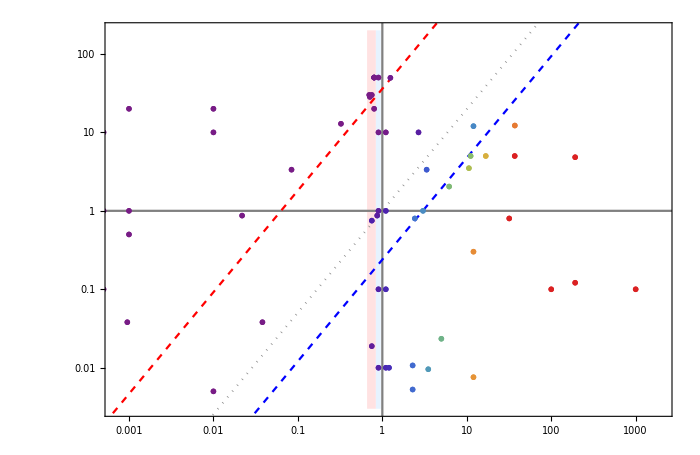

```mathematica
(* Simulations where a finite volume release is considered *)
pulseSimulations = Join[Range[101,158],Range[160,169]]; 
(* We define which simulations lead to a self-sustained buoyant dike *)
ssDike = Join[{104,105,109,110,115,114,119,123,128,130,132,133,134,142,143},Range[ 149,156],Range[160,169]];

(* ------ Getting the positions in the parametric space ------ *)
parCoord = ConstantArray[0,{Length[pulseSimulations],2}];
(* Variable containing the value of Subscript[ℬ, k] and Subscript[τ, b] *)
overrun=ConstantArray[0,{Length[pulseSimulations],1}];
(* Variable containing the aspect ratio at the end of the simulation *)
markerList = ConstantArray[0,{Length[pulseSimulations],1}];
(* Variable containing the marker type of the point to visualize *)

(* Loop over the simulations *)
For[iter = 1,iter≤ Length[pulseSimulations],iter++,

(* Get the simulation string *)
sim=simString[pulseSimulations[[iter]]];

(* Get Subscript[τ, b] *)
tstar = (ts/.Symbol[ToString[sim]<>"prop"])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]);

(* Decide which marker type to use *)
If[MemberQ[ssDike,pulseSimulations[[iter]]],
If[tstar< 1,markerList[[iter]] = fm["Triangle",10];,
markerList[[iter]] = fm["Diamond",10];;
], (* filled triangle or diamond for self-sustained dikes *)
If[tstar< 1,markerList[[iter]] =Graphics[{Dynamic@EdgeForm@Directive[CurrentValue["Color"],JoinForm["Round"],AbsoluteThickness[2],Opacity[1]],FaceForm[Transparent],PolygonMarker["Square",Offset[7]]},AlignmentPoint->{0,0}]; (* empty square for arrested fractures *),
markerList[[iter]] =Graphics[{Dynamic@EdgeForm@Directive[CurrentValue["Color"],JoinForm["Round"],AbsoluteThickness[2],Opacity[1]],FaceForm[Transparent],PolygonMarker["Square",Offset[7]]},AlignmentPoint->{0,0}]; (* empty square for arrested fractures *);
];
];

(* get the value of the value of Subscript[ℬ, k] *)
parCoord[[iter,1]] = ℬ/.vertexScaling["K",Symbol[ToString[sim]<>"prop"],ts/.Symbol[ToString[sim]<>"prop"],False];

(* Choose the color, marker type, and charactersitc value *)
parCoord[[iter,2]] = ℬ/.vertexScaling["M",Symbol[ToString[sim]<>"prop"],ts/.Symbol[ToString[sim]<>"prop"],False];

(* get the value of the overrun at the end of the simulation (transformed into the color code later) *)
overrun[[iter]] =Abs[(Max[Symbol[sim]["max_breadth"][[1]]]/(Lstarh/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],1,False])/(1/π^(1/3)))];

If[parCoord[[iter,1]]≥ 100,Print[pulseSimulations[[iter]]]];
];

(* Transform the aspect ratio into a color code, scaled between 1 (Radial) and 5 (Full buoyant) *)
colorList=ColorData["Rainbow",#]&/@Rescale[overrun,{1,8}][[;;]];
(*colorList=ColorData["Rainbow",#]&/@Rescale[aspectRatio,{1,10}][[;;]];*)
(* Transform the solution to plot it *)
parCoord={#}&/@parCoord;

(* ------ Define some plot options ------ *)
xlabel=MaTeX`MaTeX["\\mathcal{B}_{rks}",FontSize->Myfontsize];
ylabel=MaTeX`MaTeX["\\mathcal{B}_{rms}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio-> 0.65,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

(* ------ Create the figure ------ *)
Show[
ListLogLogPlot[{{{0.837,10^-5},{0.957,10^-5}},{{0.660,10^-5},{0.837,10^-5}}},Joined-> True,Filling->{1->{Top,Opacity[.75,LightBlue]},2->{Top,Opacity[.75,LightRed]}},PlotRange->{{7. 10^-4,2 10^3},{ 3 10^-3,2 10^2}}(*{{9 10^-3,501},{ 5 10^-3,75}}*)],(* Plotting the metastable zone(s) *)
LogLogPlot[1,{x,10^-7,5*10^10},PlotStyle->{Gray}],(* plotting the line for Subscript[τ, b]==1 *)
ListLogLogPlot[{{1,10^-11},{1,10^9}},Joined->True,PlotStyle->{Gray}] ,(* plotting the line for Subscript[ℬ, k]==1 *)
LogLogPlot[x^(35/27)(1)^(-4/9),{x,10^-7,5*10^10},PlotStyle->{Dotted,Gray}],(* Mb = 1 *)
LogLogPlot[x^(35/27)(3.16 10^-4)^(-4/9),{x,10^-7,5*10^10},PlotStyle->{Dashed,Red}],(* Mb = 3.16 x 10^-4 *)
LogLogPlot[x^(35/27)(25)^(-4/9),{x,10^-7,5*10^10},PlotStyle->{Dashed,Blue}],(* Mb = 25 *)
ListLogLogPlot[parCoord,PlotStyle->colorList,PlotRange->{{10^-4,10^3},{10^-4,10^2}},PlotMarkers->markerList,PlotLegends->BarLegend[{"Rainbow",{1,10}},LegendLabel->Placed[MaTeX["\\text{Overrun [-]}",FontSize->Myfontsize],Top]]],(* Plotting the simulations coordinates *)
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[pulseSimulations, ssDike, parCoord, overrun, markerList,colorList,iter,sim, tstar]
Clear[xlabel, ylabel, opt]
```

```mathematica
ℬ/.vertexScaling["K",{},t,False]/.{t-> 0.5 timeParameters[{},False,True][[-1]]}//PowerExpand
timeParameters[{},False,True][[-1]]
```

0.659754

Kp^(8/3)/(Ep Qo Δγ^(5/3))

```mathematica
(𝒦^(8/5)/.vertexScaling["M",{},ts,False]/.{Kp-> KIc})(ℬ/.pulseVertexScalings["K",{},ts,False]/.{Kp-> KIc})//PowerExpand
ℬ/.vertexScaling["M",{},ts,False]/.{Kp-> KIc}//PowerExpand
0.025^(8/5)5
```

(Qo^(1/3) ts^(7/9) Δγ)/(Ep^(5/9) μp^(4/9))

(Qo^(1/3) ts^(7/9) Δγ)/(Ep^(5/9) μp^(4/9))

0.013667

```mathematica
0.75^(5/3)
```

0.619111

```mathematica
Solve[α== (𝒦/.vertexScaling["M",{},ts,False]/.{Kp-> KIc}),KIc]
Solve[β==ℬ/.pulseVertexScalings["K",{},ts,False]/.{Kp-> KIc},Δγ]
```

{{KIc→(Ep^(13/18) Qo^(1/6) α μp^(5/18))/ts^(1/9)}}

{{Δγ→(KIc^(8/5) β)/(Ep^(3/5) (Qo ts)^(3/5))}}

### Evaluate Overrun

#### During Viscosity Dominated

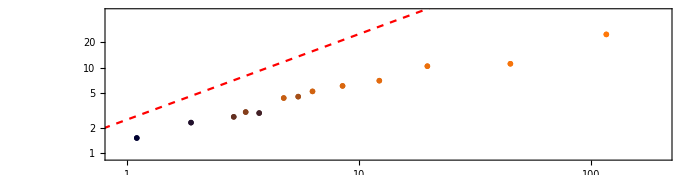

```mathematica
(* Simulations where a self-sustained dike emerged from a pulse *)
duringViscSSDike =Join[ {110,115,119,132},Range[ 152,154],Range[ 160, 165]];

(* ------ Getting the positions in the parametric space ------ *)
overrun = ConstantArray[0,{Length[duringViscSSDike],1}];
(* Variable containing the value of of the overrun Subscript[O, r] *)
charVal = ConstantArray[0,{Length[duringViscSSDike],1}];
(* Variable containing the value guiding the overrun *)

times = ConstantArray[0,{Length[duringViscSSDike],1}];
mb=ConstantArray[0,{Length[duringViscSSDike],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["RustTones"]/@Range[0,1,1/(Length[duringViscSSDike]-1)];

(* Loop over the simulations *)
For[iter = 1,iter≤ Length[duringViscSSDike],iter++,

(* Get the simulation string *)
sim=simString[duringViscSSDike[[iter]]];

(* Get the overrun Subscript[O, r] *)
overrun[[iter]]=Abs[(Max[Symbol[sim]["max_breadth"][[1]]]/(Lstarh/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],1,False])/(1/π^(1/3)))];
If[overrun[[iter]]≤ 1,overrun[[iter]]=1;]; (* set to zero if negative or below 1% *)

(* Get tstar *)
times[[iter]]=(ts/.Symbol[ToString[sim]<>"prop"])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]);

charVal[[iter]]=(ℳ/.vertexScaling["BKh",{},t,False])^(23/63)(ℬ/.vertexScaling["M",{},t,False]/.{t-> Vo/Qo})^(2/7)/.{Kp-> KIc}/.Symbol[ToString[sim]<>"prop"];

mb[[iter]]=(ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],ts/.Symbol[ToString[sim]<>"prop"],False]);

];

(* --------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Plotting the figure >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* --------------------------------------------------------------------------------------- *)

(* ------ Order the data ------ *)
plotList={#}&/@({charVal[[Ordering[mb]]] ,overrun[[Ordering[mb]]]}ᵀ);

(* ------ Define some plot options ------ *)
xlabel=MaTeX["\\mathcal{M}_{bk}^{23/63}\mathcal{B}_{rms}^{2/7}",FontSize->Myfontsize];
ylabel=MaTeX["Or",FontSize->Myfontsize];
opt={Frame->True,AspectRatio-> 1/4,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

Leg =BarLegend[{"RustTones",{Min[mb],Max[mb]}},LegendLayout->"Row",LegendLabel->MaTeX["\\mathcal{M}_{bk}",FontSize->Myfontsize],ScalingFunctions->{Log,Exp}];
optlegend={PlotLegends->Leg};

(* ------ Create the figure ------ *)
Show[ListLogLogPlot[plotList,PlotStyle->colors,PlotMarkers->fm["Diamond",7],PlotRange->{{0.9,200},{0.9,45}},optlegend]
,LogLogPlot[2.46 x,{x,0.1,10^6},PlotStyle->{Dashed,Red}]
,opt]

(* ----------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Cleaning the notebook >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ----------------------------------------------------------------------------------------- *)
Clear[plotList, charVal, overrun,duringViscSSDike,sim, iter]
Clear[parFit, fit,times, mb, colors]
Clear[xlabel, ylabel, opt]
```

```mathematica
1.68/π^(-1/3)(((pulseTimeScales[{},False,True][[-1]]/.{Mp-> μp})/(timeParameters[{},False,True][[-2]]/.{Mp-> μp}))^(2/9)(Lstarh/.vertexScaling["BMh",{},t,False])/(Lstarh/.vertexScaling["BKh",{},t,False]))//PowerExpand
(𝒦/.vertexScaling["BMh",{},t,False])^(-46/27)(ℬ/.vertexScaling["M",{},t,False]/.{t-> Vo/Qo})^(2/7)//PowerExpand
```

(2.46051 Ep^(59/63) Qo^(5/21) Vo^(2/9) Δγ^(100/189) μp^(5/21))/Kp^(46/27)

(Ep^(59/63) Qo^(5/21) Vo^(2/9) Δγ^(100/189) μp^(5/21))/Kp^(46/27)

```mathematica
0.6976/π^(-1/3)((Lstar/.vertexScaling["M",{},ts,False])/(Lstarh/.vertexScaling["BKh",{},t,False]))/.{ts-> Vo/Qo}//PowerExpand
(𝒦/.vertexScaling["BMh",{},t,False])^(-2/3)(ℬ/.vertexScaling["M",{},t,False]/.{t-> Vo/Qo})^(4/7)//PowerExpand
```

(1.0217 Ep^(1/9) Vo^(4/9) Δγ^(2/3))/(Kp^(2/3) Qo^(1/9) μp^(1/9))

(Ep^(1/9) Vo^(4/9) Δγ^(2/3))/(Kp^(2/3) Qo^(1/9) μp^(1/9))

```mathematica
((pulseTimeScales[{},False,True][[-1]]/.{Mp-> μp})/(timeParameters[{},False,True][[-2]]/.{Mp-> μp}))//PowerExpand
(ℳ/.vertexScaling["BKh",{},t,False])(ℬ/.vertexScaling["M",{},t,False]/.{t-> Vo/Qo})^(9/7)//PowerExpand
```

(Ep^(16/7) Qo^(3/7) Vo Δγ^(41/21) μp^(3/7))/Kp^(14/3)

(Ep^(16/7) Qo^(3/7) Vo Δγ^(41/21) μp^(3/7))/Kp^(14/3)

```mathematica
(ℬ/.vertexScaling["M",{},ts,False]/.{Qo-> Vo/ts})//PowerExpand
(ℳ/.vertexScaling["BKh",{},t,False])(ℬ/.vertexScaling["M",{},t,False]/.{t-> Vo/Qo})//PowerExpand
```

(ts^(4/9) Vo^(1/3) Δγ)/(Ep^(5/9) μp^(4/9))

(Ep^(22/9) Qo^(5/9) Vo^(7/9) Δγ^(5/3) μp^(5/9))/Kp^(14/3)

#### During Toughness Dominated

{0.000290767,0.00413562,0.00742555,0.000110626,0.1}

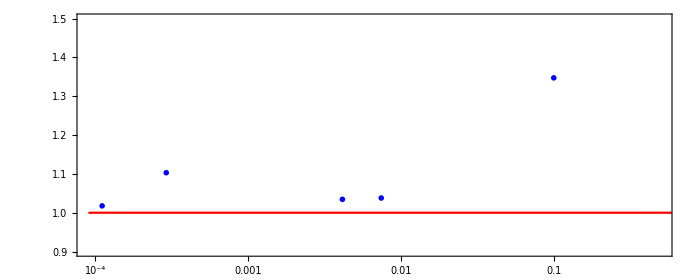

```mathematica
(* Simulations where a self-sustained dike emerged from a pulse *)
duringToughSSDike ={123,133,134,149,151};

(* ------ Getting the positions in the parametric space ------ *)
overrun = ConstantArray[0,{Length[duringToughSSDike],1}];
(* Variable containing the value of of the overrun Subscript[O, r] *)
charVal = ConstantArray[0,{Length[duringToughSSDike],1}];
(* Variable containing the value guiding the overrun *)

times = ConstantArray[0,{Length[duringToughSSDike],1}];

(* Loop over the simulations *)
For[iter = 1,iter≤ Length[duringToughSSDike],iter++,

(* Get the simulation string *)
sim=simString[duringToughSSDike[[iter]]];

(* Get the overrun Subscript[O, r] *)
overrun[[iter]]=Abs[(Max[Symbol[sim]["max_breadth"][[1]]]/(Lstarh/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],1,False])/(1/π^(1/3)))];
If[overrun[[iter]]≤ 1,overrun[[iter]]=1;]; (* set to zero if negative or below 1% *)

(* Get tstar *)
times[[iter]]=(ts/.Symbol[ToString[sim]<>"prop"])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]);

(* Get Subscript[ℳ, bk] for a transition during the release *)
charVal[[iter]] =(ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],ts/.Symbol[ToString[sim]<>"prop"],False]);

];

(* --------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Plotting the figure >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* --------------------------------------------------------------------------------------- *)
charVal
(* ------ Define some plot options ------ *)
xlabel=MaTeX["\\mathcal{M}_{bk}",FontSize->Myfontsize];
ylabel=MaTeX["Or",FontSize->Myfontsize];
opt={Frame->True,AspectRatio-> Automatic,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

(* ------ Create the figure ------ *)
Show[ListLogLinearPlot[{charVal ,overrun}ᵀ,PlotStyle->Blue,PlotMarkers-> fm["Diamond",7],PlotRange->{{9 10^-5,0.5},{0.9,1.5}}]
,LogLinearPlot[1,{x,9 10^-5,1},PlotStyle->Red]
,opt]

(* ----------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Cleaning the notebook >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ----------------------------------------------------------------------------------------- *)
Clear[charVal, overrun,duringToughSSDike,sim, iter, times]
Clear[xlabel, ylabel, opt]
```

#### Pulse transition

{1.63961,0.526088}

8/15

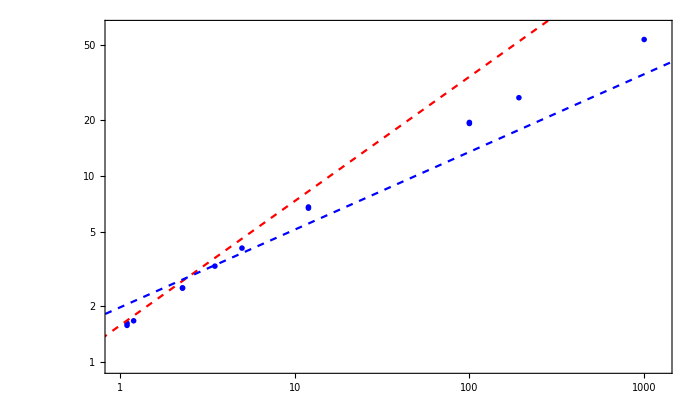

```mathematica
(* Simulations where a self-sustained dike emerged from a pulse *)
pulseSSDikes ={104,105,109,128,130,142,143,155,156,166, 167,168,169};

(* ------ Getting the positions in the parametric space ------ *)
overrun = ConstantArray[0,{Length[pulseSSDikes],1}];
(* Variable containing the value of of the overrun Subscript[O, r] *)
charVal = ConstantArray[0,{Length[pulseSSDikes],1}];
(* Variable containing the value guiding the overrun *)

times = ConstantArray[0,{Length[pulseSSDikes],1}];

(* Loop over the simulations *)
For[iter = 1,iter≤ Length[pulseSSDikes],iter++,

(* Get the simulation string *)
sim=simString[pulseSSDikes[[iter]]];

(* Get the overrun Subscript[O, r] *)
overrun[[iter]]=Abs[(Max[Symbol[sim]["max_breadth"][[1]]]/(Lstarh/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],1,False])/(1/π^(1/3)))];
If[overrun[[iter]]≤ 1,overrun[[iter]]=1;]; (* set to zero if negative or below 1% *)

(* Get tstar *)
times[[iter]]=(ts/.Symbol[ToString[sim]<>"prop"])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]);

(* Get Subscript[ℬ, rks] for a transition during the release *)
charVal[[iter]] =(ℬ/.vertexScaling["K",Symbol[ToString[sim]<>"prop"],ts/.Symbol[ToString[sim]<>"prop"],False]);

];

(* ------ Getting the power law for a transition after ------ *)
fitAfter=LinearModelFit[{Log10[charVal],Log10[overrun]}ᵀ,x,x];
parAfter={10^fitAfter[[1,2,1]]};
AppendTo[parAfter,fitAfter[[1,2,2]]]
Rationalize[fitAfter[[1,2,2]],0.01]

(* --------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Plotting the figure >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* --------------------------------------------------------------------------------------- *)

(* ------ Define some plot options ------ *)
xlabel=MaTeX["\\mathcal{B}_{rks}",FontSize->Myfontsize];
ylabel=MaTeX["Or",FontSize->Myfontsize];
opt={Frame->True,AspectRatio-> Automatic,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle(*,FrameLabel->{xlabel,ylabel}*)};

(* ------ Create the figure ------ *)
Show[ListLogLogPlot[{charVal ,overrun}ᵀ,PlotStyle->Blue,PlotMarkers-> fm["Diamond",7],PlotRange->{{0.95,1.25 10^3},{0.95,62.5}}]
,LogLogPlot[ ((3 π^(1/3))/(√2))^(2/5) x^(2/3),{x,0.5,2 10^3}, PlotStyle->{Dashed, Red}] (* Limit Superieure *)
,LogLogPlot[1.9682408204087039 x^(5/12),{x,0.5,2 10^3}, PlotStyle->{Dashed, Blue}](* Limit inferieure *)
,opt]

(* ----------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Cleaning the notebook >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ----------------------------------------------------------------------------------------- *)
Clear[charVal, overrun,duringToughSSDike,sim, iter, times]
Clear[xlabel, ylabel, opt]
```

```mathematica
ℳ/.vertexScaling["BKh",{},t]
```

(Ep^3 Qo Δγ^(2/3) μp)/Kp^(14/3)

```mathematica
29/1000*100//N
```

2.9

```mathematica
2(3/(π √2))^(2/5)/π^(-1/3)Lstar/.pulseVertexScalings["K",{},t,False]/.{Kp-> √(32/π)KIc }//N
((3 π^(1/3))/(√2))^(2/5) //N
2(3/(π √2))^(2/5)Lstar/.pulseVertexScalings["K",{},t,False]/.{Kp-> √(32/π)KIc }//N
```

(1.57373 Ep^(2/5) (Qo ts)^(2/5))/KIc^(2/5)

1.57373

(1.07452 Ep^(2/5) (Qo ts)^(2/5))/KIc^(2/5)

```mathematica
(2 (3/(π √2))^(2/5)Lstar/.pulseVertexScalings["K",{},t,False])/(π^(-1/3)Lstarh/.pulseVertexScalings["BKh",{},t,False])/.{Kp-> √(32/π)KIc }//PowerExpand//N
ℬ^(2/3)/.pulseVertexScalings["K",{},t,False]/.{Qo ts -> Vo}//PowerExpand
```

(0.725987 Ep^(2/5) Qo^(2/5) ts^(2/5) Δγ^(2/3))/KIc^(16/15)

(Ep^(2/5) Vo^(2/5) Δγ^(2/3))/Kp^(16/15)

```mathematica
((pulseTimeScales[{},False,True][[2]]/.{Mp-> μp})/
(pulseTimeScales[{},False,True][[-2]]/.{Mp-> μp}))//PowerExpand
ℬ^(2/3)/.pulseVertexScalings["K",{},t,False]/.{Qo ts -> Vo}//PowerExpand

(2 0.836Lstar/.pulseVertexScalings["M",{},t,False]/.{Qo ts -> Vo}/.{t-> (pulseTimeScales[{},False,True][[-2]]/.{Mp-> μp})})/(1/π^(1/3))//PowerExpand

(2 0.836Lstar/.pulseVertexScalings["M",{},t,False]/.{Qo ts -> Vo}/.{t-> (0.14pulseTimeScales[{},False,True][[-2]]/.{Mp-> μp})})/(Lstarh/.pulseVertexScalings["BKh",{},t,False])/(1/π^(1/3))//PowerExpand
ℬ^(5/12)/.pulseVertexScalings["K",{},t,False]/.{Qo ts -> Vo}//PowerExpand
```

(Ep^(27/20) Vo^(27/20) Δγ^(9/4))/Kp^(18/5)

(Ep^(2/5) Vo^(2/5) Δγ^(2/3))/Kp^(16/15)

(2.4488 Ep^(1/4) Vo^(1/4))/Δγ^(1/4)

(1.96824 Ep^(1/4) Vo^(1/4) Δγ^(5/12))/Kp^(2/3)

(Ep^(1/4) Vo^(1/4) Δγ^(5/12))/Kp^(2/3)

```mathematica
Solve[1.9682408204087039 ℬ^(5/12)== ℬ^(2/3)((3 π^(1/3))/(√2))^(2/5),ℬ]
```

{{ℬ→0.},{ℬ→2.44679}}

### Deviation from radial

Deviation in the case after the pulse

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

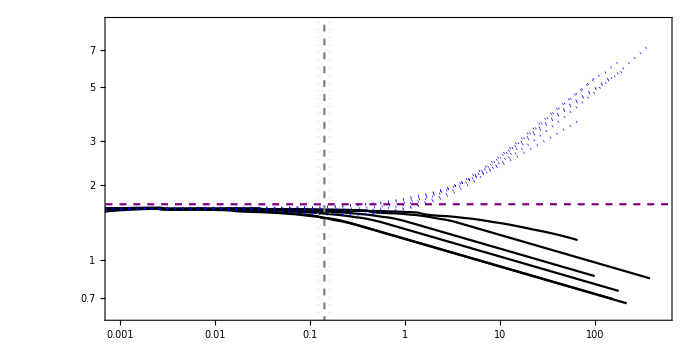

```mathematica
pulseDikes ={104,142,166,167,168,169};(* selection of dikes where the transition happens after the release *)
 
(* Instantiate arrays where the plots of height, and maximum breadth are stored.
The list of errors gives the dimensionless time when the error between the height and breadth exceeds 2.5% *)
breadthPlots= ConstantArray[0,{Length[pulseDikes],1}];
heightPlots= ConstantArray[0,{Length[pulseDikes],1}];
errors= ConstantArray[0,{Length[pulseDikes],1}];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[pulseDikes],iter++,
(* Get the simulation string *)
sim=simString[pulseDikes[[iter]]];

(* We first evaluate the transition time in this case *)
tmbVo=pulseTimeScales[Symbol[ToString[sim]<>"prop"],False][[-2]];

(* Get the dimensionless time *)
time=Symbol[sim]["time"]/(tmbVo);

(* Get the normalized plot of the maximum breadth *)
breadthPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["max_breadth"][[1]]/(Lstar/.pulseVertexScalings["M",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->Black,
PlotRange->{{9 10^-4,5 10^2},{0.6,9}}];

(* Get the normalized plot of the height *)
heightPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["height"][[1]]/(Lstar/.pulseVertexScalings["M",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dotted,Blue}];

(* Get the point where deviation takes place *)
errors[[iter]] = Position[Abs[(Symbol[sim]["height"][[1]]/(Lstar/.pulseVertexScalings["K",Symbol[ToString[sim]<>"prop"],t,False])-Symbol[sim]["max_breadth"][[1]]/(Lstar/.pulseVertexScalings["K",Symbol[ToString[sim]<>"prop"],t,False]))/(Symbol[sim]["height"][[1]]/( Lstar/.pulseVertexScalings["K",Symbol[ToString[sim]<>"prop"],t,False]))]*100,_?(#≥2.5&)][[1,1]];
errors[[iter]] = time[[errors[[iter]]]];

];

(* We print the mean and the standard deviation of the dimensionless deviation time *)
MaTeX["\\textrm{The mean of the dimensionless deviation time is:}",FontSize->Myfontsize]
MaTeX[ "\\overline{t_{dev}/t_{rmbm}^{[V]}} = "<>ToString[Mean[errors]],FontSize->Myfontsize]
MaTeX["\\textrm{with a standard deviation of:}",FontSize->Myfontsize]
MaTeX[ "\\sigma\\left(\\overline{t_{dev}/t_{rmbm}^{[V]}}\\right) = "<>ToString[StandardDeviation[errors]],FontSize->Myfontsize]
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{rmbm}^{[V]}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{H(t)\\vert\\vert\\underset{z}{\\text{max}}\\left\\{b\\left(z,t\\right)\\right\\}}{L_{rm}^{\\left[V\\right]}}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle(*,FrameLabel->{xlabel,ylabel}*)};
Show[breadthPlots,
heightPlots,
ListLogLogPlot[{{Mean[errors],10^-6},{Mean[errors],4.5 10^5}},Joined->True,PlotStyle->{Gray,Dashed}],
ListLogLogPlot[{{Mean[errors]+StandardDeviation[errors],10^-6},{Mean[errors]+StandardDeviation[errors],4.5 10^5}},Joined->True,PlotStyle->{LightGray,Dotted}],
ListLogLogPlot[{{Mean[errors]-StandardDeviation[errors],10^-6},{Mean[errors]-StandardDeviation[errors],4.5 10^5}},Joined->True,PlotStyle->{LightGray,Dotted}],
LogLogPlot[2 0.836,{x,5 10^-4,2 10^3}, PlotStyle->{Purple, Dashed}],
opt]
(* We then clear the variables to have a clean working notebook *)
Clear[pulseDikes, breadthPlots, heightPlots,errors, sim, time,tmbVo]
Clear[xlabel, ylabel, opt, iter]
```

The plot shows the height and maximum breadth normalized by the characterstic toughnees length-scale L_k(t) in function of the dimensionless transition time t/t_kb. The red dashed line representes the toughness solution which we approximate with sufficient precision. The dark gray vertical line is the mean where deviaiton takes place and light gray dotted lines are the upper and lower value including standard deviation.

### Transition Bm to Bk

#### Pulse Transition

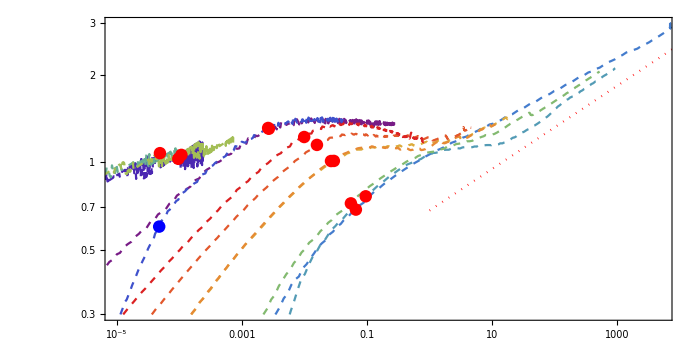

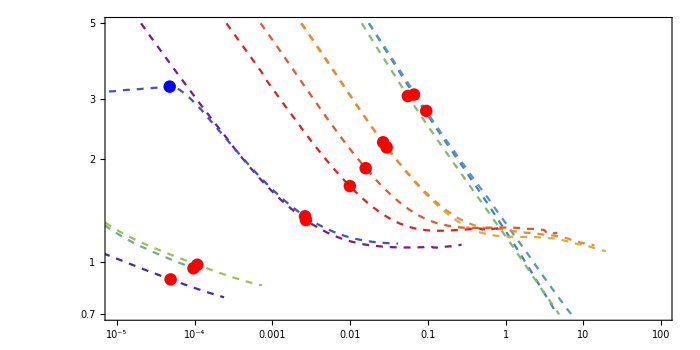

```mathematica
(* Simulations where a self-sustained dike emerged from a pulse *)
pulseSSDikes ={104,105,109,128,130,142,143,155,156,166,167,168,169};

(* Prepare plots and other stuff *)
stabBreadthPlots= ConstantArray[0,{Length[pulseSSDikes],1}];
heightPlots= ConstantArray[0,{Length[pulseSSDikes],1}];
shutIn = ConstantArray[0,{Length[pulseSSDikes],6}];
mb = ConstantArray[0,{Length[pulseSSDikes],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/(Length[pulseSSDikes]-1)];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[pulseSSDikes],iter++,
(* Get the simulation string *)
sim=simString[pulseSSDikes[[iter]]];

(* We first evaluate the transition time in this case *)
tbmbk=pulseTimeScales[Symbol[ToString[sim]<>"prop"],False][[-1]];

(* Get the dimensionless time *)
time=Symbol[sim]["time"]/(tbmbk);

(* Get parameters *)
index =Position[Symbol[sim]["time"],_?(#==(ts/.Symbol[ToString[sim]<>"prop"])&)][[1,1]];
If[Position[Position[Differences[Symbol[sim]["max_breadth"][[1]]],_?(#==0.0&)]][[1]]=={},
index2 = Length[Symbol[sim]["max_breadth"][[1]]];,
index2=Position[Differences[Symbol[sim]["max_breadth"][[1]]],_?(#==0.0&)][[1,1]];
];


shutIn[[iter,1]] = (ts/.Symbol[ToString[sim]<>"prop"])/tbmbk;
shutIn[[iter,2]] =(Symbol[sim]["stab_breadth"][[1]]/(Lstarh/.pulseVertexScalings["BMh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index]];
shutIn[[iter,3]] =(Symbol[sim]["height"][[1]]/(Lstarv/.pulseVertexScalings["BMt",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index]];
shutIn[[iter,4]] =(Symbol[sim]["time"][[index2]])/tbmbk;
shutIn[[iter,5]] =(Symbol[sim]["stab_breadth"][[1]]/(Lstarh/.pulseVertexScalings["BMh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index2]];
shutIn[[iter,6]] =(Symbol[sim]["height"][[1]]/(Lstarv/.pulseVertexScalings["BMt",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index2]];

(* Get the normalized plot of the maximum breadth *)
stabBreadthPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["stab_breadth"][[1]]/(Lstarh/.pulseVertexScalings["BMh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dashed,colors[[iter]]},(*PlotMarkers-> {"o"},*)
PlotRange->{{9.75 10^-6,5 10^3},{0.3,3}}];

(* Get the normalized plot of the height *)
heightPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["height"][[1]]/( Lstarv/.pulseVertexScalings["BMt",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dashed,colors[[iter]]},PlotRange->{{9.75 10^-6, 10^2},{0.7,5}}];

mb[[iter]]=ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],t,False];

];

(* -------------------- First make breadht behind head figure -------------------- *)
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{bmbk}^{[V]}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{b\\left(z^\\prime = 0.75 \\times L_b\\right)}{L_{hbm}^{[V]}\\left(t\\right)}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

legendPlot=Round[Sort[mb],0.0001];
optlegend={PlotLegends->LineLegend[colors[[Ordering[mb]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[mb],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

Show[stabBreadthPlots,LogLogPlot[t^(1/7)/π^(1/3),{t,1,10^4},PlotStyle->{Red,Dotted}],
ListLogLogPlot[shutIn[[;;,{1,2}]],Joined->False,PlotStyle->{Thick,Blue},optlegend],
ListLogLogPlot[shutIn[[;;,{4,5}]],Joined->False,PlotStyle->{Thick,Red}],
opt]

(* -------------------- Second make height figure -------------------- *)
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{bmbk}^{[V]}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{H(t)}{L_{vbm}^{[V]}\\left(t\\right)}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle(*,FrameLabel->{xlabel,ylabel}*)};

Show[heightPlots,
ListLogLogPlot[shutIn[[;;,{1,3}]],Joined->False,PlotStyle->{Thick,Blue}],
ListLogLogPlot[shutIn[[;;,{4,6}]],Joined->False,PlotStyle->{Thick,Red}],
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[viscDikes, stabBreadthPlots, heightPlots, sim, time,tbmbk, shutIn,colors]
Clear[maxBreadthPlots, mb]
Clear[xlabel, ylabel, opt, iter]
```

```mathematica
1.394/(2 π^(1/3))
```

0.4759

```mathematica
Position[Differences[DI168["max_breadth"][[1]]],_?(#==0.0&)][[1,1]]
Position[Position[Differences[DI168["max_breadth"][[1]]],_?(#==0.0&)]][[1]]=={}
```

722

False

t^(1/7)/π^(1/3)

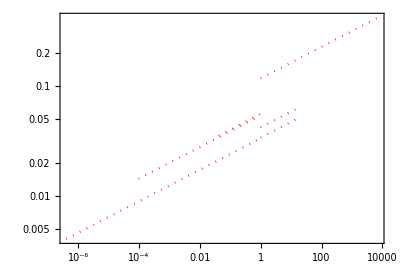

```mathematica
(π^(-1/3)(Lstarh/.pulseVertexScalings["BKh",{},t,False])/(Lstarh/.pulseVertexScalings["BMh",{},t,False]))/.{t-> t (pulseTimeScales[{},False,True][[-1]])}/.{Mp-> μp}/.{Kp-> KIc}/.{ts-> Vo/Qo}//PowerExpand
Show[analPlots,PlotRange-> All]
```

```mathematica
(π^(-1/3)(Lstarh/.pulseVertexScalings["BKh",{},t,False])/(Lstarh/.pulseVertexScalings["BMh",{},t,False]))/.{t-> t (pulseTimeScales[{},False,True][[-1]])}/.{Mp-> μp}/.{Kp-> KIc}/.{ts-> Vo/Qo}//PowerExpand
0.66^(5/3)
```

t^(1/7)/π^(1/3)

0.500311

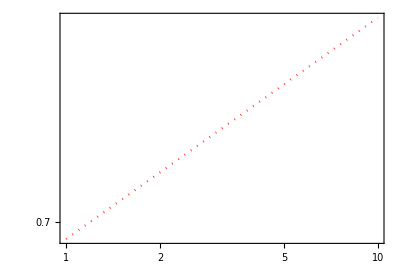

```mathematica
LogLogPlot[t^(1/7)/π^(1/3),{t,1,10},PlotStyle->{Red,Dotted}]
```

```mathematica
(π^(-1/3)Lstarh/.pulseVertexScalings["BKh",{},t,False])/(Lstarh/.pulseVertexScalings["BMh",{},t,False])
```

(Kp^(2/3) t^(1/7))/(Ep^(3/7) π^(1/3) (Qo ts)^(1/7) Δγ^(2/21) μp^(1/7))

## Plotting footprints

### Plotting colored footprints

#### Dimensionless plot

```mathematica
(* --------- Choose the simulation to display --------- *)
simulationNumber =123;

(* Get the simulation string *)
sim=simString[simulationNumber];

(* --------- Function generating the fooprints and getting backgrounds --------- *)
(* call sequence is: number of the simulation, boolean [True if dimensionless quantities should be plotted (default), False for dimensional quantities] *)
plotInfos = coloredFootprints[simulationNumber];

(* --------- We generate the label and the legend --------- *)
legendPlot=Round[(Symbol[sim <>"fractures"]["time"])/(timeParameters[Symbol[sim<>"prop"],False][[-1]]),0.0001];
xlabel=MaTeX["x/L_b \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["z/L_b \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->{xlabel,ylabel},ImageSize->300
,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend["Rainbow",MaTeX[#,FontSize->Myfontsize-2]&/@legendPlot,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","t/t_b \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure--------- *)
Show[("Background"/.plotInfos),ListPlot["Footprints"/.plotInfos,Joined->True,optlegend,PlotStyle->"Style"/.plotInfos],opt]

(* We then clear the variables to have a clean working notebook *)
(*Clear[simulationNumber,sim,plotInfos,legendPlot,xlabel,ylabel,opt,optlegend]*)
```

-Graphics-

#### Dimensional plot

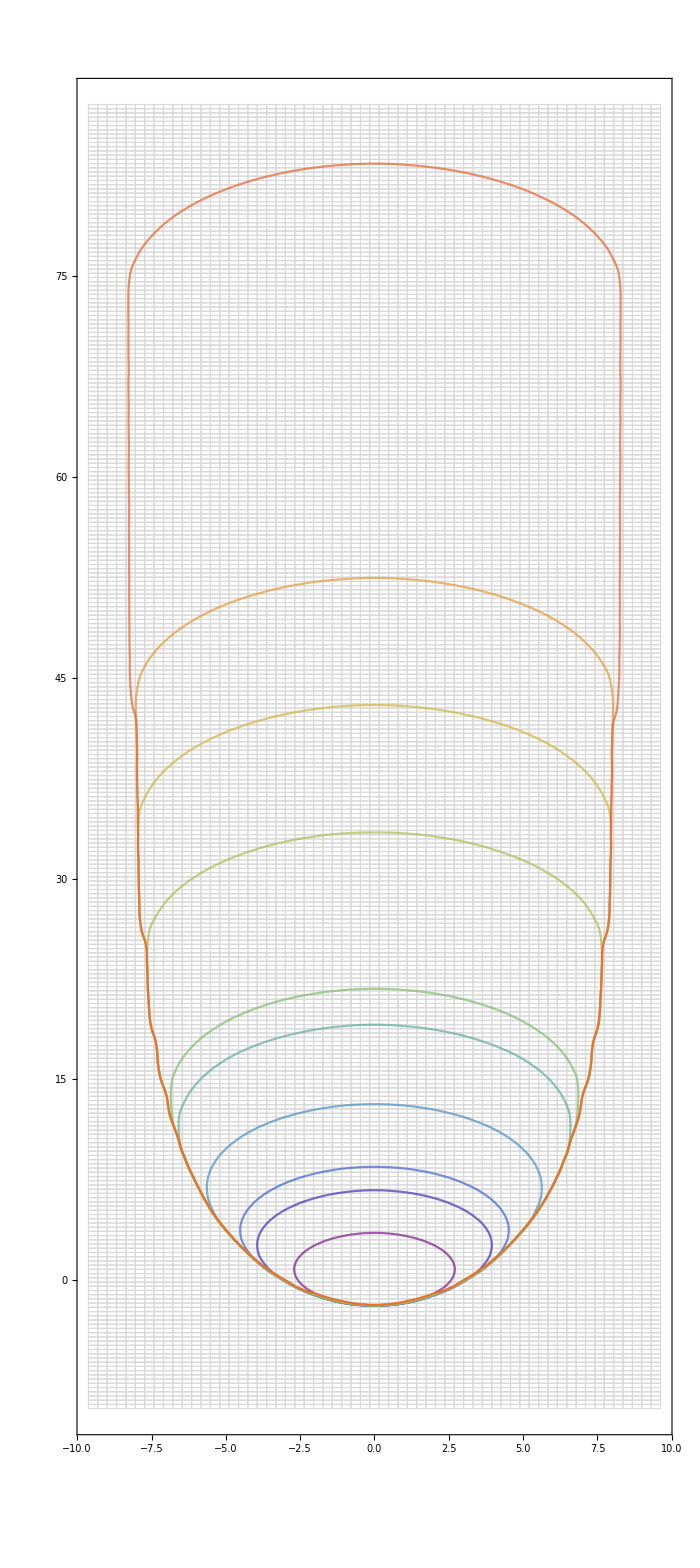

```mathematica
(* --------- Choose the simulation to display --------- *)
simulationNumber =76;

(* Get the simulation string *)
sim=simString[simulationNumber];

(* --------- Function generating the fooprints and getting backgrounds --------- *)
(* call sequence is: number of the simulation, boolean [True if dimensionless quantities should be plotted, False for dimensional quantities] *)
plotInfos = coloredFootprints[simulationNumber,False];

(* --------- We generate the label and the legend --------- *)
legendPlot=Round[Symbol[sim <>"fractures"]["time"],0.0001];
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["z \\text{ [m]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend["Rainbow",MaTeX`MaTeX[#,FontSize->Myfontsize-2]&/@legendPlot,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","t \\text{ [s]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure--------- *)
Show[("Background"/.plotInfos),ListPlot["Footprints"/.plotInfos,Joined->True,optlegend,PlotStyle->"Style"/.plotInfos],opt]

(* We then clear the variables to have a clean working notebook *)
Clear[simulationNumber,sim,plotInfos,legendPlot,xlabel,ylabel,opt,optlegend]
```

### Plotting distribution of opening or pressure

#### Plotting opening

```mathematica
ℬ/.pulseVertexScalings["K",#,t,False]&/@{DI143prop}
ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI143prop}
ℳ/.vertexScaling["BKh",#,t,False]&/@{DI143prop}
(ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI143prop})^(23/63)(ℳ/.vertexScaling["BKh",#,t,False]&/@{DI143prop})^(2/7)
```

{1.2}

{0.01}

{53820.2}

{4.1835}

```mathematica
ℬ/.pulseVertexScalings["K",#,t,False]&/@{DI134prop}
ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI134prop}
ℳ/.vertexScaling["BKh",#,t,False]&/@{DI134prop}
(ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI134prop})^(23/63)(ℳ/.vertexScaling["BKh",#,t,False]&/@{DI134prop})^(2/7)
```

{1.1}

{10.}

{0.00742555}

{0.571105}

```mathematica
ℬ/.pulseVertexScalings["K",#,t,False]&/@{DI105prop}
ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI105prop}
ℳ/.vertexScaling["BKh",#,t,False]&/@{DI105prop}
(ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI105prop})^(23/63)(ℳ/.vertexScaling["BKh",#,t,False]&/@{DI105prop})^(2/7)
```

{192.039}

{0.121169}

{5.27545×10^8}

{143.694}

```mathematica
ℬ/.pulseVertexScalings["K",#,t,False]&/@{DI164prop}
ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI164prop}
ℳ/.vertexScaling["BKh",#,t,False]&/@{DI164prop}
(ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI164prop})^(23/63)(ℳ/.vertexScaling["BKh",#,t,False]&/@{DI164prop})^(2/7)
```

{31.8292}

{0.799513}

{39983.8}

{19.026}

```mathematica
ℬ/.pulseVertexScalings["K",#,t,False]&/@{DI119prop}
ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI119prop}
ℳ/.vertexScaling["BKh",#,t,False]&/@{DI119prop}
(ℬ/.pulseVertexScalings["M",#,ts,False]&/@{DI119prop})^(23/63)(ℳ/.vertexScaling["BKh",#,t,False]&/@{DI119prop})^(2/7)
```

{3.34692}

{3.34692}

{2.2375}

{1.95645}

In dimensionless form

```mathematica
(* --------- Choose the simulation to display --------- *)
simulationNumber=164;
(* Get the simulation string *)
sim=simString[simulationNumber];

(* --------- Function generating the fooprints and getting backgrounds --------- *)
index =-1; (* which of the footprints you want to plot *)
plotInfos =get2DDistributions[simulationNumber,index,"hbk"];

(* --------- We generate the legend and the labels --------- *)
opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->("Labels"/.plotInfos)[[{1,2}]],ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};
optlegend={PlotLegends->("Legend"/.plotInfos)};


(* --------- Plooting the opening distribution on the footprint --------- *)Show[("Graphics"/.plotInfos),ListPlot[("Fp"/.plotInfos),Joined->True,PlotStyle->{Black, Thickness[0.01]},optlegend],Epilog-> {Inset[("Labels"/.plotInfos)[[5]],{0.0,0.0}]},opt]

(* We then clear the variables to have a clean working notebook *)
Clear[simulationNumber,sim,index,plotInfos,opt,optlegend]
```

-Graphics-

In dimensional form

```mathematica
(* --------- Choose the simulation to display --------- *)
simulationNumber=67;

(* Get the simulation string *)
sim=simString[simulationNumber];

(* --------- Function generating the fooprints and getting backgrounds --------- *)
index =-1; (* which of the footprints you want to plot *)
plotInfos =get2DDistributions[simulationNumber,index,"no"];

(* --------- We generate the legend and the labels --------- *)
opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->("Labels"/.plotInfos)[[{1,2}]],ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};
optlegend={PlotLegends->("Legend"/.plotInfos)};

(* --------- Plooting the opening distribution on the footprint --------- *)Show[("Graphics"/.plotInfos),ListPlot[("Fp"/.plotInfos),Joined->True,PlotStyle->{Black, Thickness[0.01]},optlegend],Epilog-> {Inset[("Labels"/.plotInfos)[[5]],{0.0,0.0}]},opt]

(* We then clear the variables to have a clean working notebook *)
Clear[simulationNumber,sim,index,plotInfos,opt,optlegend]
```

-Graphics-

#### Plotting pressure ( to adapt)

In dimensionless form

```mathematica
(* --------- Choose the simulation to display --------- *)
simulationNumber=67;

(* Get the simulation string *)
sim=simString[simulationNumber];

(* --------- Function generating the fooprints and getting backgrounds --------- *)
index =-1; (* which of the footprints you want to plot *)
plotInfos =get2DDistributions[simulationNumber,index,True,"pn"];

(* --------- We generate the legend and the labels --------- *)
xlabel=MaTeX["x/L_b \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["z/L_b \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};
optlegend={PlotLegends->("Legend"/.plotInfos)};

(* --------- Plooting the opening distribution on the footprint --------- *)Show[("Graphics"/.plotInfos),ListPlot[{(Symbol[sim <>"fractures"]["fp_x"][["Index"/.plotInfos]])/(Lstarh/.vertexScaling["BKh",Symbol[sim<>"prop"],1,False]),(Symbol[sim <>"fractures"]["fp_y"][["Index"/.plotInfos]])/(Lstarh/.vertexScaling["BKh",Symbol[sim<>"prop"],1,False])}ᵀ,Joined->True,PlotStyle->{Black,Thickness[.01]},
optlegend],
Epilog->{Inset[MaTeX["t/t_b \\approx"<>ToString[Round[(Symbol[sim <>"fractures"]["time"][["Index"/.plotInfos]])/(timeParameters[Symbol[sim<>"prop"],False][[-1]]),0.0001]]<>"\\text{  [-]}",Magnification->5],{0,6.45}]},
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[simulationNumber,sim,index,plotInfos,xlabel,ylabel,opt,optlegend]
```

-Graphics-

In dimensional form

```mathematica
(* --------- Choose the simulation to display --------- *)
simulationNumber=67;

(* Get the simulation string *)
sim=simString[simulationNumber];

(* --------- Function generating the fooprints and getting backgrounds --------- *)
index =-1; (* which of the footprints you want to plot *)
plotInfos =get2DDistributions[simulationNumber,index,False,"pn"];

(* --------- We generate the legend and the labels --------- *)
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["y \\text{ [m]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->All,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};
optlegend={PlotLegends->("Legend"/.plotInfos)};

(* --------- Plooting the opening distribution on the footprint --------- *)Show[("Graphics"/.plotInfos),ListPlot[{Symbol[stringSim <>"fractures"]["fp_x"][["Index"/.plotInfos]],Symbol[stringSim <>"fractures"]["fp_y"][["Index"/.plotInfos]]}ᵀ,Joined->True,PlotStyle->{Black,Thickness[.01]},
optlegend],
Epilog->{Inset[MaTeX["t \\approx"<>ToString[Round[Symbol[sim <>"fractures"]["time"][["Index"/.plotInfos]],0.0001]]<>"\\text{  [s]}",Magnification->5],{0,590}]},
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[simulationNumber,sim,index,plotInfos,xlabel,ylabel,opt,optlegend]
```

-Graphics-

## Generate Figures of supplementary material

## Ongoing release case (Q_o, t_s→ ∞)

#### Evaluate all dikes with continuous release

```mathematica
(* Choose the dikes to plot *)
injectDikes =Join[{41,43,45,47,49},Range[72,76]];

(* Instantiate arrays where the plots of height, breadth and semi-analytical MK edge solution are stored. The list of theoretical deviation theorDev gives the points evaluated *)
velocities= ConstantArray[0,{Length[injectDikes],1}]; (* Array containing the velocities *)
velocitiePlots =ConstantArray[0,{Length[injectDikes],1}];
heightPlots =ConstantArray[0,{Length[injectDikes],1}];
breadthPlots = ConstantArray[0,{Length[injectDikes],1}];
dimViscosity = ConstantArray[0,{Length[injectDikes],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/(Length[injectDikes]-1)];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[injectDikes],iter++,
(* Get the simulation string *)
sim=simString[injectDikes[[iter]]];

(* We get velocity of the fracture in the buoyant direction *)
dt=Differences[Symbol[sim]["time"]]; (* Time steps *)
dH=Differences[Symbol[sim]["height"][[1]]]; (* Height increment *)
velocities[[iter]] = dH/dt ;

dimViscosity[[iter]] =ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],t,False];
indices = Table[i*15-1,{i,1,Floor[Length[velocities[[iter]]]/15]}];

velocitiePlots[[iter]] =
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),(velocities[[iter]][[indices]])/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.1,750},{0.02,2}},Joined->True];
heightPlots[[iter]] =ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),Symbol[sim]["height"][[1]][[indices]]/(Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],Symbol[sim]["time"][[indices]],False])}ᵀ,PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.1,750},{0.05,10}},Joined->True];
breadthPlots[[iter]] =ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),Symbol[sim]["max_breadth"][[1]][[indices]]/(Lstarh/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],Symbol[sim]["time"][[indices]],False])}ᵀ, PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.1,750},{0.075,40}},Joined->True];
];

(* ---------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Plotting the figures >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ---------------------------------------------------------------------------------------- *)

(* --------- We generate the label and the legend for the velocity figure --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{b} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\dot{H}/\\dot{L_{v}} \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[velocitiePlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),(velocities[[iter-1]][[indices]])/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
opt]

(* --------- We generate the label and the legend for the Breadht --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{b} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{\\underset{y}{\\text{max}}\\left\\{b\\left(y,t\\right)\\right\\}}{L_b}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[breadthPlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),(velocities[[iter-1]][[indices]])/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
opt]

(* --------- We generate the label and the legend for the Height --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{b} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["H(t)/L_v",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[heightPlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),(velocities[[iter-1]][[indices]])/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
opt]

(* ----------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Cleaning the notebook >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ---------------------------------------------------------------------------------------- *)
Clear[injectDikes, velocities, velocitiePlots, heightPlots, breadthPlots,dimViscosity]
Clear[colors,iter,sim,dt,dH,legendPlot]
Clear[xlabel, ylabel, opt,optlegend,indices]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

## Finite volume case (V_o, t_s∈(0,∞))

### Transition visc SS Dike to tough SS Dike

```mathematica
pulseDikes =Join[{110,114,115,119,123,132,133,134, 149},Range[151,154],Range[160,169]];
```

#### Viscous Transition

```mathematica
(* selection of dikes where the transition happens after the release *)
viscDikes =Join[{110},Range[152,154],Range[160,165]];

(* Prepare plots and other stuff *)
stabBreadthPlots= ConstantArray[0,{Length[viscDikes],1}];
maxBreadthPlots= ConstantArray[0,{Length[viscDikes],1}];
heightPlots= ConstantArray[0,{Length[viscDikes],1}];
shutIn = ConstantArray[0,{Length[viscDikes],5}];
mb = ConstantArray[0,{Length[viscDikes],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/(Length[viscDikes]-1)];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[viscDikes],iter++,
(* Get the simulation string *)
sim=simString[viscDikes[[iter]]];

(* We first evaluate the transition time in this case *)
tbmbk=pulseTimeScales[Symbol[ToString[sim]<>"prop"],False][[-1]];
tbm =timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]];
shutIn[[iter,1]] = (ts/.Symbol[ToString[sim]<>"prop"])/tbmbk;
shutIn[[iter,2]] = (ts/.Symbol[ToString[sim]<>"prop"])/tbm;

index =Position[Symbol[sim]["time"],_?(#==(ts/.Symbol[ToString[sim]<>"prop"])&)][[1,1]];
shutIn[[iter,3]] =(Symbol[sim]["stab_breadth"][[1]]/(Lstarh/.pulseVertexScalings["BMh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index]];
shutIn[[iter,4]] =(Symbol[sim]["height"][[1]]/(Lstarv/.pulseVertexScalings["BMt",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index]];
shutIn[[iter,5]] =(Symbol[sim]["max_breadth"][[1]]/(Lstarv/.vertexScaling["BMh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index]];
index =Position[Symbol[sim]["time"],_?(#==Nearest[Symbol[sim]["time"],0.01tbmbk][[1]]&)][[1,1]];

(* Get the dimensionless time *)
time=Symbol[sim]["time"]/(tbmbk);
time2=Symbol[sim]["time"]/(tbm);

(* Get the normalized plot of the maximum breadth *)
stabBreadthPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["stab_breadth"][[1]]/(Lstarh/.pulseVertexScalings["BMh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dashed,colors[[iter]]},(*PlotMarkers-> {"o"},*)
PlotRange->{{9 10^-7,2 10^2},{0.15,2}}];

(* Get the normalized plot of the maximum breadth *)
maxBreadthPlots[[iter]]=ListLogLogPlot[{time2,Symbol[sim]["max_breadth"][[1]]/(Lstarh/.vertexScaling["BMh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dashed,colors[[iter]]},
PlotRange->{{0.05,2 10^2},{0.3,4}}];

(* Get the normalized plot of the height *)
heightPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["height"][[1]]/( Lstarv/.pulseVertexScalings["BMt",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dashed,colors[[iter]]},PlotRange->{{9 10^-7,2 10^2},{0.15,2}}];

mb[[iter]]=ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],t,False];

];

(* -------------------- First make breadht behind head figure -------------------- *)
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{bmbk}^{[V]}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{b\\left(z=z_{\\textrm{max}}-0.75\\times L_b\\right)}{L_{hbm}^{[V]}}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

Show[stabBreadthPlots,
ListLogLogPlot[shutIn[[;;,{1,3}]],Joined->False,PlotStyle->{Thick,Blue}],
opt]

(* -------------------- First make  max breadht head figure -------------------- *)
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{bm}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{\\underset{z}{\\text{max}}\\left\\{b\\left(z,t\\right)\\right\\}}{L_{hbm}}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

legendPlot=Round[Sort[mb],0.0001];
optlegend={PlotLegends->LineLegend[colors[[Ordering[mb]]],MaTeX[#,FontSize->Myfontsize-2]&/@legendPlot,LegendLabel->Column@MaTeX[{"\\mathcal{M}_{bk} \\text{ [-]}"},FontSize->Myfontsize]]};

Show[maxBreadthPlots,
LogLogPlot[(2FractureLength/.injectionVertexSolutions["M",DI041prop,.5,(x timeParameters[DI041prop,False][[-3]]),True,False])/( Lstarh/.vertexScaling["BMt",DI041prop,t,False]),{x, 10^-3,5},PlotStyle->{Dotted,Blue}],
LogLogPlot[1.68 x^(2/9),{x,1,10^5},PlotStyle->{Red,Dotted}],
ListLogLogPlot[shutIn[[;;,{2,5}]],Joined->False,PlotStyle->{Thick,Blue},optlegend],
opt]

(* -------------------- Second make height figure -------------------- *)
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{bmbk}^{[V]}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{h(t)}{L_{vbm}^{[V]}}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

Show[heightPlots,
ListLogLogPlot[shutIn[[;;,{1,4}]],Joined->False,PlotStyle->{Thick,Blue}],
opt]

(* We then clear the variables to have a clean working notebook *)
Clear[viscDikes, stabBreadthPlots, heightPlots, sim, time,tbmbk, shutIn,colors]
Clear[maxBreadthPlots, mb]
Clear[xlabel, ylabel, opt, iter]
```

-Graphics-

-Graphics-

-Graphics-

#### Toughness Transition

```mathematica
(* selection of dikes where the transition happens after the release *)
toughDikes ={123,133,134,149,151};

(* Prepare plots and other stuff *)
stabBreadthPlots= ConstantArray[0,{Length[toughDikes],1}];
maxBreadthPlots= ConstantArray[0,{Length[toughDikes],1}];
heightPlots= ConstantArray[0,{Length[toughDikes],1}];
shutIn = ConstantArray[0,{Length[toughDikes],5}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/(Length[toughDikes]-1)];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[toughDikes],iter++,
(* Get the simulation string *)
sim=simString[toughDikes[[iter]]];

(* We first evaluate the transition time in this case *)
tbmbk=pulseTimeScales[Symbol[ToString[sim]<>"prop"],False][[-1]];
tbk =timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]];
shutIn[[iter,1]] = (ts/.Symbol[ToString[sim]<>"prop"])/tbmbk;
shutIn[[iter,2]] = (ts/.Symbol[ToString[sim]<>"prop"])/tbk;


index =Position[Symbol[sim]["time"],_?(#==(ts/.Symbol[ToString[sim]<>"prop"])&)][[1,1]];
shutIn[[iter,3]] =(Symbol[sim]["stab_breadth"][[1]]/(Lstarh/.pulseVertexScalings["BKh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index]];
shutIn[[iter,4]] =(Symbol[sim]["height"][[1]]/(Lstarv/.pulseVertexScalings["BKt",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index]];
shutIn[[iter,5]] =(Symbol[sim]["max_breadth"][[1]]/(Lstarv/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]}))[[index]];

(* Get the dimensionless time *)
time=Symbol[sim]["time"]/(tbmbk);
time2=Symbol[sim]["time"]/(tbk);

(* Get the normalized plot of the maximum breadth *)
stabBreadthPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["stab_breadth"][[1]]/(Lstarh/.pulseVertexScalings["BKh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dashed,colors[[iter]]},(*PlotMarkers-> {"o"},*)
PlotRange->{{0.8,1.1 10^4},{0.5,1}},PlotStyle-> color[[iter]]];

(* Get the normalized plot of the maximum breadth *)
maxBreadthPlots[[iter]]=ListLogLogPlot[{time2,Symbol[sim]["max_breadth"][[1]]/(Lstarh/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dashed,colors[[iter]]},
PlotRange->{{0.05,20},{0.3,1.5}},PlotStyle-> color[[iter]]];

(* Get the normalized plot of the height *)
heightPlots[[iter]]=ListLogLogPlot[{time,Symbol[sim]["height"][[1]]/( Lstarv/.pulseVertexScalings["BKt",Symbol[ToString[sim]<>"prop"],t,False]/.{t->Symbol[sim]["time"]})}ᵀ,Joined->True,PlotStyle->{Dashed,colors[[iter]]},PlotRange->{{0.8,1.1 10^4},{0.1,2}},PlotStyle-> color[[iter]]];

];

(* -------------------- First make breadht behind head figure -------------------- *)
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{bmbk}^{[V]}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{b\\left(z=z_{\\textrm{max}}-0.75\\times L_b\\right)}{L_b}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

Show[stabBreadthPlots,
ListLogLogPlot[shutIn[[;;,{1,3}]],Joined->False,PlotStyle->{Thick,Blue}],
LogLogPlot[π^(-1/3),{x,0.1,10^5},PlotStyle->{Dotted,Green}],
opt]

(* -------------------- First make  max breadht head figure -------------------- *)
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{bk}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{\\underset{z}{\\text{max}}\\left\\{b\\left(z,t\\right)\\right\\}}{L_{b}}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

Show[maxBreadthPlots,
ListLogLogPlot[shutIn[[;;,{2,5}]],Joined->False,PlotStyle->{Thick,Blue}],
LogLogPlot[π^(-1/3),{x,0.1,10^5},PlotStyle->{Dotted,Green}],
opt]

(* -------------------- Second make height figure -------------------- *)
(* Define the labels and plotting options *)
xlabel=MaTeX["\\frac{t}{t_{bmbk}^{[V]}}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{h(t)}{L_{vbk}^{[V]}}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

Show[heightPlots,
ListLogLogPlot[shutIn[[;;,{1,4}]],Joined->False,PlotStyle->{Thick,Blue}],
opt]
colors
(* We then clear the variables to have a clean working notebook *)
Clear[pulseDikes, stabBreadthPlots, heightPlots, sim, time,tbmbk, shutIn,colors]
Clear[xlabel, ylabel, opt, iter]
```

-Graphics-

-Graphics-

-Graphics-

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

## Orders of magnitue

### Values for cases of MoLe21 paper

```mathematica
MoLe21Paper ={ {μp-> 12 5 10^-3,Vo-> 135,Qo-> 0.05,ts-> 135/0.05,Ep-> (20 10^9)/(1-0.25^2),KIc-> 1.5 10^6,Δγ-> 1700 9.81},(* Case 1 *)
{μp-> 12 1,Vo-> 27,Qo-> 0.01,ts-> 27/0.01,Ep-> (30 10^9)/(1-0.25^2),KIc-> 1.0 10^6,Δγ-> 1700 9.81},(* Case 2 *)
{μp-> 12 200,Vo-> 5 10^5,Qo-> 10,ts-> 5 10^5/10,Ep-> (20 10^9)/(1-0.2^2),KIc-> 1.5 10^6,Δγ-> 500},(* Case 3 *)
{μp-> 12 200,Vo-> 5 10^5,Qo-> 0.1,ts-> 5 10^5/0.1,Ep-> (20 10^9)/(1-0.2^2),KIc-> 1.5 10^6,Δγ-> 500}(* Case 4 *)
} //N;(* Give the characteristic values of all cases *)
 
(* Instantiate array with the characteristic values *)
charVals= ConstantArray[0,{Length[MoLe21Paper]+1,11}];

(* Loop over the Cases *)
For[iter = 1,iter≤ Length[MoLe21Paper],iter++,

(* Get Subscript[ℬ, K](t=ts) *)
charVals[[iter+1,2]] = ℬ/.vertexScaling["K",MoLe21Paper[[iter]],ts/.MoLe21Paper[[iter]],False];

(* Get Subscript[ℳ, b] *)
charVals[[iter+1,3]] = ℳ/.vertexScaling["BKh",MoLe21Paper[[iter]],ts/.MoLe21Paper[[iter]],False];

(* Get Subscript[ℳ, b] *)
charVals[[iter+1,4]] = ℬ/.vertexScaling["M",MoLe21Paper[[iter]],ts/.MoLe21Paper[[iter]],False];

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,5]] = (ts/.MoLe21Paper[[iter]])/(timeParameters[MoLe21Paper[[iter]],False][[-1]]);

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,6]] = (ℳ/.vertexScaling["BKh",MoLe21Paper[[iter]],ts/.MoLe21Paper[[iter]],False])^(23/63)*(ℬ/.vertexScaling["M",MoLe21Paper[[iter]],ts/.MoLe21Paper[[iter]],False])^(2/7);

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,7]] = (Lstarh/.vertexScaling["BKh",MoLe21Paper[[iter]],ts/.MoLe21Paper[[iter]],False]);

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,8]] = 
pulseTimeScales[MoLe21Paper[[iter]],False][[-1]]/3600/24/365;

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,9]] = (Lstarv/.pulseVertexScalings["BMt",MoLe21Paper[[iter]],
pulseTimeScales[MoLe21Paper[[iter]],False][[-1]],False])/1000;

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,10]] = (Lstar/.vertexScaling["M",MoLe21Paper[[iter]],
timeParameters[MoLe21Paper[[iter]],False][[-3]],False]);

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,11]] = (Lstar/.pulseVertexScalings["M",MoLe21Paper[[iter]],
pulseTimeScales[MoLe21Paper[[iter]],False][[-2]],False]);
];

(* We format the table *)
charVals[[;;,1]]={"MöLe21","1","2","3","4"};
charVals[[1,2;;]]={MaTeX["\\mathcal{B}_{rk}^{[V]}"],MaTeX["\\mathcal{M}_{bk}"],MaTeX["\\mathcal{B}_{rms}"],MaTeX["\\frac{t_s}{t_T}"],MaTeX["\\mathcal{M}_{bk}^{23/63}\\mathcal{B}_{rms}^{2/7}"],MaTeX["L_b \\left[\\textrm{m}\\right]"],MaTeX["t_{bmbk}^{[V]} \\left[\\textrm{y}\\right]"],MaTeX["H\\left(t=t_{bmbk}^{[V]}\\right) \\left[\\textrm{km}\\right]"],
MaTeX["L_{rmbm} \\left[\\textrm{m}\\right]"],
MaTeX["L_{rmbm}^{[V]} \\left[\\textrm{m}\\right]"]};

(* Show the table *)
MaTeX["\\textrm{We show characteristic values of cases from Möri and Lecampion, (2021) in the following Table:}",FontSize->Myfontsize]
Grid[charVals,Alignment->Left,Spacings->{2,1},Frame->All,Background->{{Gray,None},{LightGray,None}}]

(* We then clear the variables to have a clean working notebook *)
Clear[MoLe21Paper, charVals]
Clear[iter]
```

-Graphics-

MöLe21 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1 | 65.4647 | 286.605 | 18.2792 | 83.8585 | 18.0993 | 20.0747 | 0.0245381 | 21.3466 | 45.0494 | 114.635
2 | 60.8172 | 256671. | 0.809952 | 1.52523 | 88.8581 | 15.3199 | 21.9752 | 14.4089 | 90.7868 | 84.8397
3 | 267.831 | 2.06083×10^8 | 0.283203 | 0.394989 | 756.383 | 208.008 | 326742. | 2314.81 | 3204.8 | 2136.44
4 | 267.831 | 2.06083×10^6 | 2.19274 | 5.48835 | 252.669 | 208.008 | 326742. | 2314.81 | 1659.92 | 2136.44

### Other examples

```mathematica
(* Give the characteristic values of other examples *)
otherExamples ={ {μp-> 12 300,Vo-> 3.2 10^6,Qo->0.1,ts->3.2 10^6/0.1,Ep-> (12.5 10^9)/(1-0.2^2),KIc-> 1.5 10^6,Δγ-> 1000},(* Dahm et al. (2021) example with lower volume *)
{μp-> 12 300,Vo->6.05 10^8,Qo-> 50,ts->6.05 10^8/50,Ep-> 44 10^9,KIc->1.5  10^6,Δγ-> 4120},
(* Reches and Fink (1988) A assuming a reasonable toughness *)
{μp-> 12 300,Vo->6.05 10^8,Qo-> 50,ts->6.05 10^8/50,Ep-> 44 10^9,KIc->1000  10^6,Δγ-> 4120},
(* Reches and Fink (1988) B assuming a reasonable toughness *)
{μp-> 12 300,Vo->6.05 10^8,Qo-> 0.05,ts->6.05 10^8/0.05,Ep-> 44 10^9,KIc->1.5  10^6,Δγ-> 4120},
(* Reches and Fink (1988) C assuming a reasonable toughness *)
{μp-> 12 300,Vo->6.05 10^8,Qo-> 0.05,ts->6.05 10^8/0.05,Ep-> 44 10^9,KIc->1000  10^6,Δγ-> 4120},
(* Reches and Fink (1988) D assuming a reasonable toughness *)
{μp-> 12 100,Vo->1 10^6,Qo-> 10,ts->1 10^6/10,Ep-> 2 10^9,KIc->5 10^6,Δγ-> 1000}
(* Delaney and Pollard (1981) assuming a reasonable toughness *)
};
 
(* Instantiate array with the characteristic values *)
charVals= ConstantArray[0,{Length[otherExamples]+1,11}];

(* Loop over the Cases *)
For[iter = 1,iter≤ Length[otherExamples],iter++,

(* Get Subscript[ℬ, K](t=ts) *)
charVals[[iter+1,2]] = ℬ/.vertexScaling["K",otherExamples[[iter]],ts/.otherExamples[[iter]],False];

(* Get Subscript[ℳ, b] *)
charVals[[iter+1,3]] = ℳ/.vertexScaling["BKh",otherExamples[[iter]],ts/.otherExamples[[iter]],False];

(* Get Subscript[ℳ, b] *)
charVals[[iter+1,4]] = ℬ/.vertexScaling["M",otherExamples[[iter]],ts/.otherExamples[[iter]],False];

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,5]] = (ts/.otherExamples[[iter]])/(timeParameters[otherExamples[[iter]],False][[-1]]);

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,6]] = (ℳ/.vertexScaling["BKh",otherExamples[[iter]],ts/.otherExamples[[iter]],False])^(23/63)*(ℬ/.vertexScaling["M",otherExamples[[iter]],ts/.otherExamples[[iter]],False])^(2/7);

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,7]] = (Lstarh/.vertexScaling["BKh",otherExamples[[iter]],ts/.otherExamples[[iter]],False]);

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,8]] = 
pulseTimeScales[otherExamples[[iter]],False][[-1]]/3600/24/365;

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,9]] = (Lstarv/.pulseVertexScalings["BMt",otherExamples[[iter]],
pulseTimeScales[otherExamples[[iter]],False][[-1]],False])/1000;

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,10]] = (Lstar/.vertexScaling["M",otherExamples[[iter]],
timeParameters[otherExamples[[iter]],False][[-3]],False]);

(* Get Subscript[t, s]/Subscript[t, b] *)
charVals[[iter+1,11]] = (Lstar/.pulseVertexScalings["M",otherExamples[[iter]],
pulseTimeScales[otherExamples[[iter]],False][[-2]],False]);
];

(* We format the table *)
charVals[[;;,1]]={"Parameter \\\ Paper",MaTeX["\\textrm{Dahm et al. (2020)} \\left\\{\\textrm{Low } V_o\\right\\}"],MaTeX["\\textrm{Reches and Fink (1988) A }"],
MaTeX["\\textrm{Reches and Fink (1988) B }"],
MaTeX["\\textrm{Reches and Fink (1988) C }"],
MaTeX["\\textrm{Reches and Fink (1988) D }"],
MaTeX["\\textrm{Delaney and Pollard (1981) assuming } Q_o = 100 \\left[\\textrm{m}^3\\textrm{ s}^{-1}\\right], K_{Ic}= 5 \\left[\\textrm{MPa }\\textrm{m}^{1/2}\\right]"]};
charVals[[1,2;;]]={MaTeX["\\mathcal{B}_{rk}^{[V]}"],MaTeX["\\mathcal{M}_{bk}"],MaTeX["\\mathcal{B}_{rms}"],MaTeX["\\frac{t_s}{t_T}"],MaTeX["\\mathcal{M}_{bk}^{23/63}\\mathcal{B}_{rms}^{2/7}"],MaTeX["L_b \\left[\\textrm{m}\\right]"],MaTeX["t_{bmbk}^{[V]} \\left[\\textrm{y}\\right]"],MaTeX["H\\left(t=t_{bmbk}^{[V]}\\right) \\left[\\textrm{km}\\right]"],
MaTeX["L_{rmbm} \\left[\\textrm{m}\\right]"],
MaTeX["L_{rmbm}^{[V]} \\left[\\textrm{m}\\right]"]};

(* Show the table *)
MaTeX["\\textrm{We show characteristic values of some other examples in the following Table:}",FontSize->Myfontsize]
Grid[charVals,Alignment->Left,Spacings->{2,1},Frame->All,Background->{{Gray,None},{LightGray,None}}]

(* We then clear the variables to have a clean working notebook *)
Clear[otherExamples, charVals]
Clear[iter]
```

-Graphics-

Parameter \ Paper | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 1230.63 | 1.19801×10^6 | 20.1457 | 95.0247 | 390.61 | 131.037 | 1.21563×10^6 | 18518.5 | 967.711 | 2540.66
-Graphics- | 244498. | 5.94022×10^10 | 157.197 | 1333.62 | 36378.8 | 50.9874 | 2.2792×10^10 | 4.87442×10^7 | 1764.32 | 8965.57
-Graphics- | 7.41348 | 0.0039406 | 157.197 | 2360.66 | 0.562011 | 3891.07 | 0.00151196 | 109.674 | 1764.32 | 8965.57
-Graphics- | 244498. | 5.94022×10^7 | 3386.72 | 69074.4 | 7023.66 | 50.9874 | 2.2792×10^10 | 4.87442×10^7 | 657.667 | 8965.57
-Graphics- | 7.41348 | 3.9406×10^-6 | 3386.72 | 5637.24 | 0.108507 | 3891.07 | 0.00151196 | 109.674 | 657.667 | 8965.57
-Graphics- | 28.9912 | 525.305 | 4.85801 | 15.2623 | 15.4631 | 292.402 | (640 5^(1/3))/657 | 80. | 715.501 | 1189.21

## Special evaluations

```mathematica
(* Davis et al. (2020) ; Limiting volume *)
```

```mathematica
(1-ν)/(16 G)((9 π^4 KIc^8)/(Cos[θ] Δγ^5))^(1/3)/.{G-> Emod/(2(1+ν)),θ-> 0}/.{Emod-> Ep(1-ν^2)}//PowerExpand
(3^(2/3)π^(4/3))/8//N
0.7(3^(2/3)π^(4/3))/8//N
0.8(3^(2/3)π^(4/3))/8//N
```

(3^(2/3) KIc^(8/3) π^(4/3) (1-ν) (1+ν))/(8 Ep Δγ^(5/3) (1-ν^2))

1.19635

0.837443

0.957078

```mathematica
G/(1-ν)/.{G-> Emod/(2(1+ν))}/.{Emod-> Ep(1-ν^2)}
```

(Ep (1-ν^2))/(2 (1-ν) (1+ν))

```mathematica
(* Salimzadeh et al. (2020) ; Limiting volume *)
```

```mathematica
(16/27(π^4 KIc^8)/(Fg^8 Ep^3 Δγ^5))^(1/3)/.{Fg-> 1.57}//PowerExpand
```

(1.1607 KIc^(8/3))/(Ep Δγ^(5/3))

```mathematica
Q0SaZi = 0.015
KIcSaZi = 2 * 10^6
dgSaZi =10*{5000, 1000, 2000, 3000, 1000, 1000,2000,2000}
muSaZi = 12{0.005,0.05,0.005,0.001,0.001,0.05,0.005,0.005}
EpSaZi = 10^9/(1-0.25^2){20,20,20,20,20,20,10,20}
tsSaZi = {15,130,25,10,50,40,25,10}
VoSaZi = tsSaZi*Q0SaZi
```

0.015

2000000

{50000,10000,20000,30000,10000,10000,20000,20000}

{0.06,0.6,0.06,0.012,0.012,0.6,0.06,0.06}

{2.13333×10^10,2.13333×10^10,2.13333×10^10,2.13333×10^10,2.13333×10^10,2.13333×10^10,1.06667×10^10,2.13333×10^10}

{15,130,25,10,50,40,25,10}

{0.225,1.95,0.375,0.15,0.75,0.6,0.375,0.15}

```mathematica
tstT = ConstantArray[0,{Length[tsSaZi],9}];
mb= ConstantArray[0,{Length[tsSaZi],9}];
bk= ConstantArray[0,{Length[tsSaZi],9}];
brms= ConstantArray[0,{Length[tsSaZi],9}];

For[iter =1,iter≤ Length[tsSaZi],iter++,
params = {KIc->KIcSaZi,Ep->EpSaZi[[iter]],Cp->0.,Qo->Q0SaZi,μp->muSaZi[[iter]],Δγ->dgSaZi[[iter]],ts->tsSaZi[[iter]],Vo->VoSaZi[[iter]], sl->{0,0}};
tstT[[iter]] = tsSaZi[[iter]]/(timeParameters[params,False][[-1]]) ;
mb[[iter]] = ℳ/.vertexScaling["BKh",params,t,False];
bk[[iter]] = ℬ/.pulseVertexScalings["K",params,t,False];
brms[[iter]] = ℬ/.pulseVertexScalings["M",params,tsSaZi[[iter]],False];

];
```

```mathematica
tstT
mb
bk
brms
mb^(23/63)brms^(2/7)
```

{1.14571,0.334986,0.609987,1.11775,1.42265,0.103073,1.13481,0.243995}

{46.6937,159.69,25.3493,6.64339,3.19381,159.69,3.16866,25.3493}

{2.66727,1.94898,1.44956,1.25477,1.09856,0.9609,0.956352,0.836512}

{0.646273,0.249139,0.384614,0.578443,0.674191,0.0996117,0.56528,0.188589}

{3.59125,4.28476,2.47739,1.70731,1.36519,3.29742,1.29443,2.02099}

```mathematica
(* Heimpel Olsen stuff *)
(* HeOlData *)
HeOlEp = (2{190, 276, 355, 2150}(1+0.5))/(1-0.5^2)(* 1.4 1.6 1.8 and 4%*)
HeOlKIc ={15,19,23,114}
HeOldg =1000*{9.8,3.4,1.8,1.5,-4.1,-126}(* Assumes density of gelatine about 1'000 kg/m3 || Air Hexane Sil OIl Mineral Oil Corn Syrup Mercury*)
CritVols =10^-6 {0.02,0.6,0.9,1.5,10} (* 1.6 Mercury ; 1.4 air ; 1.6 Air ; 1.8 Air; 4.0 Air *) 
HeOlKIcCalc = CritVols^(3/8)*HeOlEp[[{2,1,2,3,4}]]^(3/8)*Abs[HeOldg[[{-1,1,1,1,1}]]]^(5/8)
```

{760.,1104.,1420.,8600.}

{15,19,23,114}

{9800.,3400.,1800.,1500.,-4100.,-126000}

{2.×10^-8,6.×10^-7,9.×10^-7,1.5×10^-6,1/100000}

{27.6523,17.4433,23.3599,31.0927,124.438}

```mathematica
1/100000//N
```

0.00001

### Horizontal section

```mathematica
(* We load all the horizontal sections *)
horizSections =FileNames["*horizontal*",dirHost];
strList = ConstantArray[0,{Length[horizSections],2}];
For[iter = 1, iter ≤ Length[horizSections],iter++,
strList[[iter,1]] =StringSplit[StringSplit[horizSections[[iter]],"JsonFiles/"][[-1]],"_"][[1]]; (* simulation index *)
strList[[iter,2]] =  StringSplit[StringSplit[StringSplit[horizSections[[iter]],"JsonFiles/"][[-1]],"_"][[-1]],".json"][[1]]; (* location on y axis *)
Evaluate[Symbol[strList[[iter,1]]<>"horizSec"<>strList[[iter,2]]]] =Association[Import[dirHost<>StringSplit[horizSections[[iter]],"JsonFiles/"][[-1]]]]; (* Create the symbol *)
];

strList
```

Set::setraw: Cannot assign to raw object <|time→{1/10000000000,1.18173×10^7,2.37535×10^7,3.56153×10^7,4.74134×10^7,5.93308×10^7,7.12245×10^7,8.29864×10^7,9.48275×10^7,1.06821×10^8,1.18636×10^8,1.30239×10^8,1.42298×10^8},w…_→«1»,pn_horiz_slice_→{pn_sampling_coords_0→{-6933.89,«31»,6933.89},«10»,pn_3→{«1»}}|>.

Set::setraw: Cannot assign to raw object <|time→{1/10000000000,1.18173×10^7,2.37535×10^7,3.56153×10^7,4.74134×10^7,5.93308×10^7,7.12245×10^7,8.29864×10^7,9.48275×10^7,1.06821×10^8,1.18636×10^8,1.30239×10^8,1.42298×10^8},…→«1»,pn_horiz_slice_→{pn_sampling_coords_0→{-4622.6,«59»,4622.6},«31»,pn_10→{«1»}}|>.

Set::setraw: Cannot assign to raw object <|time→{1/10000000000,1.18173×10^7,2.37535×10^7,3.56153×10^7,4.74134×10^7,5.93308×10^7,7.12245×10^7,8.29864×10^7,9.48275×10^7,1.06821×10^8,1.18636×10^8,1.30239×10^8,1.42298×10^8},w…_→«1»,pn_horiz_slice_→{pn_sampling_coords_0→{-5547.11,«47»,5547.11},«25»,pn_8→{«1»}}|>.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

{{DI042,100000},{DI042,20000},{DI042,50000},{DI042,75000},{DI047,12500},{DI047,2500},{DI047,6000},{DI049,200000},{DI056,100000},{DI056,200000},{DI056,50000},{DI056,75000}}

```mathematica
opPlots = ConstantArray[0,{14,1}];
For[iter = 1,iter≤4,iter++,
opPlots[[iter]]=ListPlot[{(("w_sampling_coords_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"])/(Lstarh/.vertexScaling["Bh",DI056prop,t,False]),(("w_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"])/(10^3 wstar/.vertexScaling["Bh",DI056prop,t,False])}ᵀ,Joined->True,PlotMarkers->Automatic,PlotStyle->{Dashed,Black}];
];
For[iter = 1,iter≤6,iter++,
opPlots[[4+iter]]=ListPlot[{(("w_sampling_coords_"<>ToString[iter-1])/.DI056horizSec50000["w_horiz_slice_"])/(Lstarh/.vertexScaling["Bh",DI056prop,t,False]),(("w_"<>ToString[iter-1])/.DI056horizSec50000["w_horiz_slice_"])/(10^3 wstar/.vertexScaling["Bh",DI056prop,t,False])}ᵀ,Joined->True,PlotMarkers->Automatic,PlotStyle->{Dashed,Red}];
];

For[iter = 1,iter≤4,iter++,
opPlots[[10+iter]]=ListPlot[{(("w_sampling_coords_"<>ToString[iter-1])/.DI056horizSec200000["w_horiz_slice_"])/(Lstarh/.vertexScaling["Bh",DI056prop,t,False]),(("w_"<>ToString[iter-1])/.DI056horizSec200000["w_horiz_slice_"])/(10^3 wstar/.vertexScaling["Bh",DI056prop,t,False])}ᵀ,Joined->True,PlotMarkers->Automatic,PlotStyle->{Dashed,Blue}];
];

xlabel=MaTeX["\\frac{x}{L_b}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{w}{W_h}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};

Show[opPlots,PlotRange-> All,opt]
```

-Graphics-

```mathematica
pnPlots = ConstantArray[0,{14,1}];
For[iter = 1,iter≤4,iter++,
pnPlots[[iter]]=ListPlot[{(("pn_sampling_coords_"<>ToString[iter-1])/.DI056horizSec100000["pn_horiz_slice_"])/(Lstarh/.vertexScaling["Bh",DI056prop,t]),(10^6("pn_"<>ToString[iter-1])/.DI056horizSec100000["pn_horiz_slice_"])/(pstar/.vertexScaling["Bh",DI056prop,t])}ᵀ,Joined->True,PlotMarkers->Automatic,PlotStyle->{Dashed,Black}];
];
For[iter = 1,iter≤6,iter++,
pnPlots[[4+iter]]=ListPlot[{(("pn_sampling_coords_"<>ToString[iter-1])/.DI056horizSec50000["pn_horiz_slice_"])/(Lstarh/.vertexScaling["Bh",DI056prop,t]),(10^6("pn_"<>ToString[iter-1])/.DI056horizSec50000["pn_horiz_slice_"])/(pstar/.vertexScaling["Bh",DI056prop,t])}ᵀ,Joined->True,PlotMarkers->Automatic,PlotStyle->{Dashed,Red}];
];

For[iter = 1,iter≤4,iter++,
pnPlots[[10+iter]]=ListPlot[{(("pn_sampling_coords_"<>ToString[iter-1])/.DI056horizSec200000["pn_horiz_slice_"])/(Lstarh/.vertexScaling["Bh",DI056prop,t]),(10^6("pn_"<>ToString[iter-1])/.DI056horizSec200000["pn_horiz_slice_"])/(pstar/.vertexScaling["Bh",DI056prop,t])}ᵀ,Joined->True,PlotMarkers->Automatic,PlotStyle->{Dashed,Blue}];
];

xlabel=MaTeX["\\frac{x}{L_b}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{p}{P_h}",FontSize->Myfontsize];opt={Frame->True,AspectRatio-> 1/2,ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle,FrameLabel->{xlabel,ylabel}};
Show[pnPlots,PlotRange->{{-10,10},{0,2.25 }},opt]
```

-Graphics-

## Plotting Sections

# Under development

```mathematica
(2670-2250)*9.81
```

4120.2

{760.,1104.,1420.,8600.}

{15,19,23,114}

{9800.,3400.,1800.,1500.,-4100.,-126000}

{2.×10^-8,6.×10^-7,9.×10^-7,1.5×10^-6,1/100000}

{27.6523,17.4433,23.3599,31.0927,124.438}

```mathematica
jj/(2(1+ν)(1-ν))//Simplify
```

jj/(2-2 ν^2)

```mathematica
vertexScaling["BKt",{},t,False]
```

{Lstarv→(Qo^(2/3) t Δγ^(7/9))/(Kp^(4/9) μp^(1/3)),Lstarh→Kp^(2/3)/Δγ^(2/3),wstar→(Qo^(1/3) μp^(1/3))/(Kp^(2/9) Δγ^(1/9)),pstar→(Qo^(2/3) t Δγ^(16/9))/(Kp^(4/9) μp^(1/3)),qstar→Qo,𝒦→Kp^(14/9)/(Ep Qo^(1/3) Δγ^(2/9) μp^(1/3)),Vt→Qo t-(1. Kp^(8/3))/(Ep Δγ^(5/3))}

```mathematica
2/(π R)^(1/2)Integrate[P/((R^2-x^2)^(1/2))x,{x,0,R}]
```

ConditionalExpression[(2 P √R)/(√π), Re[R]>0&&Im[R]==0]

```mathematica
(* Choose the dikes to plot *)
toughnessDikes =Join[Range[73,75]];
(* Instantiate arrays where the plots of height, breadth and semi-analytical MK edge solution are stored. The list of theoretical deviation theorDev gives the points evaluated *)
velocities= ConstantArray[0,{Length[toughnessDikes],1}]; (* Array containing the velocities *)
velocitiePlots =ConstantArray[0,{Length[toughnessDikes],1}];
dimViscosity = ConstantArray[0,{Length[toughnessDikes],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/(Length[toughnessDikes]-1)];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[toughnessDikes],iter++,

(* Get the simulation string *)
sim=simString[toughnessDikes[[iter]]];

(* We get the average velocity of the fracture in the buoyant direction *)
dt=Differences[Symbol[sim]["time"]];
dH=Differences[Symbol[sim]["height"][[1]]];
velocities[[iter]] = dH/dt ;

dimViscosity[[iter]] =ℳ/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],t,False];

indices = Table[i*6-1,{i,1,Floor[Length[velocities[[iter]]]/6]}];

velocitiePlots[[iter]] =
ListLogLogPlot[{(Symbol[sim]["time"][[indices]] Qo/.Symbol[ToString[sim]<>"prop"])/(Vh/.vertexScaling["BKh",Symbol[ToString[sim]<>"prop"],t,False]),velocities[[iter]][[indices]]/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.6,1.35},{0.125,2.5}},Joined->True];
];

(* ---------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Plotting the figures >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ---------------------------------------------------------------------------------------- *)
dimViscosity
(* --------- We generate the label and the legend for the velocity figure --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["Q_o t / V_c \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\dot{L_{v}} \\text{ [m $\\cdot$ s$^{-1}$]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->1(*,FrameLabel->{xlabel,ylabel}*),ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[velocitiePlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-1]]),velocities[[iter-1]][[indices]](*/D[ Lstarv/.vertexScaling["BKt",Symbol[ToString[sim]<>"prop"],t,False],t]*)}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
opt]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{0.0001,0.001,0.01}

-Graphics-

## Plotting Stuff flow

### On footprint

```mathematica
Clear[DI041flow]
Evaluate[DI041flow] =Association[Import[dirHost<>"DI041"<>"_flow.json"]];
```

```mathematica
Keys[DI041flow]
```

{time,vel_list,mesh_info}

```mathematica
VelVecList=DI041flow["vel_list"][[1]];
timeVelList=DI041flow["time"];
MI=DI041flow["mesh_info"][[1]];
```

```mathematica
SELECTEDTIME=-1;
dataVELr=VelVecList[[SELECTEDTIME]];
Veltime=timeVelList[[SELECTEDTIME]];
MIlocal=MI[[SELECTEDTIME]];
Lx=MIlocal[[1]];
Nx=MIlocal[[3]];
Ly=MIlocal[[2]];
Ny=MIlocal[[4]];
myMesh=meshPlan[Lx,Nx,Ly,Ny];
centers=myMesh["centers"];
neighbors=myMesh["Neighbors"];
```

```mathematica
NumOfVelElem=Length[dataVELr];
ElementVELlist=dataVELr[[;;,9]];
```

```mathematica
VectorData={};
Table[m=neighbors[[ElementVELlist]][[i,j]];
k=ElementVELlist[[i]];
preparedDataForplot={Mean[{centers[[k]],centers[[m]]}],{dataVELr[[i,j*2-1]],dataVELr[[i,j*2]]}};
If[MemberQ[ElementVELlist,m],If[m>k,AppendTo[VectorData,preparedDataForplot];,Nothing],AppendTo[VectorData,preparedDataForplot];];Nothing,{i,1,Length[ElementVELlist]},{j,1,4}];
```

```mathematica
Table[m=neighbors[[i,j]];
If[MemberQ[ElementVELlist,i],Nothing,If[MemberQ[ElementVELlist,m],AppendTo[VectorData,{Mean[{centers[[i]],centers[[m]]}],{0,0}}]]];Nothing,{i,1,Length[neighbors]},{j,1,4}];
```

```mathematica
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["y \\text{ [m]}",FontSize->Myfontsize];
ListVectorPlot[VectorData,AspectRatio->Automatic,PlotLegends->BarLegend[Automatic,LegendLabel->Placed[MaTeX["\\text{Fluid velocity magnitude [m/s]}",FontSize->Myfontsize],Left,Rotate[#,90Degree]&],LabelStyle->Directive[FontFamily->"CMU Serif",FontSize->Myfontsize]],VectorPoints->All,VectorScaling->Automatic,VectorSizes->{0.1,15},FrameLabel->{xlabel,ylabel},Epilog->{Inset[MaTeX["\\text{time =}"<>ToString[Round[Veltime,0.0001]]<>"\\text{  s}",Magnification->20],{0,.15},Scaled[{0.5,1}]]},PlotRange->All]
```

### Sections

```mathematica
Clear[DI041sections]
Evaluate[DI041sections] =Association[Import[dirHost<>"DI041"<>"_sections.json"]];
```

```mathematica
Keys[DI041sections]
```

{time,w_vert_slice_,pn_vert_slice_,ux_vertical_y0_value,ux_vertical_y0_time,ux_vertical_y0_coord,uy_vertical_x0_value,uy_vertical_x0_time,uy_vertical_x0_coord}

```mathematica
uyVsliceVAL=DI041sections["ux_vertical_y0_value"];
uyVsliceCOOR=DI041sections["ux_vertical_y0_coord"];
uyVsliceTIME=DI041sections["ux_vertical_y0_time"];
sizeOfdata=Length[uyVsliceVAL]
```

7

```mathematica
xlabel=MaTeX["y \\text{ [m] }",FontSize->Myfontsize];
ylabel=MaTeX["u\\textsubscript{y} \\text{ [m/s]}",FontSize->Myfontsize];
LegenduyOFy01=MaTeX[#,FontSize->Myfontsize-2]&/@Round[uyVsliceTIME,0.000001];

uyTOplot=Table[ux=Abs[uyVsliceVAL[[i]]];uxcoor=uyVsliceCOOR[[i]];Table[{uxcoor[[j]],ux[[j]]},{j,1,Length[ux]}],{i,1,sizeOfdata}];
ListLogPlot[uyTOplot,PlotStyle->Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/sizeOfdata]},FrameLabel->{xlabel,ylabel},Joined->True,PlotRange->All,PlotMarkers->{"◦"},PlotLegends->LineLegend[LegenduyOFy01,LegendLabel->MaTeX["\\text{Numerical data [s]:}",FontSize->Myfontsize]]]
```

-Graphics-

# No longer used

```mathematica
pulseVertexScalings["BKt",{},t]
```

{Lstarv→(t^(1/3) (Qo ts)^(2/3) Δγ^(7/9))/(Kp^(4/9) μp^(1/3)),Lstarh→Kp^(2/3)/Δγ^(2/3),wstar→((Qo ts)^(1/3) μp^(1/3))/(Kp^(2/9) t^(1/3) Δγ^(1/9)),pstar→(t^(1/3) (Qo ts)^(2/3) Δγ^(16/9))/(Kp^(4/9) μp^(1/3)),𝒦→(Kp^(14/9) t^(1/3))/(Ep (Qo ts)^(1/3) Δγ^(2/9) μp^(1/3)),Vt→Qo ts-(1. Kp^(8/3))/(Ep Δγ^(5/3))}

```mathematica
pulseTimeScales[DI160prop,False]/10^4
```

{0,1.21257,∞,0,∞,0.0201189,4.08457}

```mathematica
𝒦/.vertexScaling["M",{},ts,False]/.{ts-> Vo/Qo}//PowerExpand
ℳ/.vertexScaling["BKh",{},ts,False]
(ℳ/.vertexScaling["BKh",{},ts,False])(Lstarh/.vertexScaling["BKh",{},ts,False])//PowerExpand
```

(Kp Vo^(1/9))/(Ep^(13/18) Qo^(5/18) μp^(5/18))

(Ep^3 Qo Δγ^(2/3) μp)/Kp^(14/3)

(Ep^3 Qo μp)/Kp^4

```mathematica
ℬ/.vertexScaling["M",{},ts,False]
(ℬ/.vertexScaling["K",{},ts,False])^(35/27)(ℳ/.vertexScaling["BKh",{},ts,False])^(-4/9)//PowerExpand
```

(Qo^(1/3) ts^(7/9) Δγ)/(Ep^(5/9) μp^(4/9))

(Qo^(1/3) ts^(7/9) Δγ)/(Ep^(5/9) μp^(4/9))

```mathematica
𝒦/.vertexScaling["M",{},ts,False]
ℬ/.vertexScaling["K",{},ts,False]/.{Qo-> Vo/ts}//PowerExpand
```

(Kp ts^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18))

(Ep^(3/5) Vo^(3/5) Δγ)/Kp^(8/5)

```mathematica
μp/.Solve[(𝒦/.vertexScaling["M",{},ts,False]/.{Qo-> Vo/ts})==α,μp][[1]]//PowerExpand
Δγ/.Solve[(ℬ/.vertexScaling["K",{},ts,False]/.{Qo-> Vo/ts})==β,Δγ][[1]]//PowerExpand
Δγ/.Solve[ts/((0.5 Ep^(5/7) μp^(4/7))/(Qo^(3/7) Δγ^(9/7)))==θ,Δγ][[1]]//PowerExpand
0.5^(7/9)
```

(Kp^(18/5) ts)/(Ep^(13/5) Vo^(3/5) α^(18/5))

(Kp^(8/5) β)/(Ep^(3/5) Vo^(3/5))

(0.583265 Ep^(5/9) θ^(7/9) μp^(4/9))/(Qo^(1/3) ts^(7/9))

0.583265

```mathematica
15 timeParameters[DI076prop,False][[-1]]
timeParameters[DI076prop,False][[-3]]
```

201359.

39086.8

```mathematica
ℳ/.vertexScaling["K",{},t]
(t/(t/.Solve[(ℳ/.vertexScaling["K",{},t])==1,t][[1]]))^(-2/5)//PowerExpand
𝒦/.vertexScaling["M",{},t]
(t/(t/.Solve[(𝒦/.vertexScaling["M",{},t])==1,t][[1]]))^(1/9)//PowerExpand
ℬ/.vertexScaling["K",{},t]
(t/(t/.Solve[(ℬ/.vertexScaling["K",{},t])==1,t][[1]]))^(3/5)//PowerExpand
ℬ/.vertexScaling["M",{},t]
(t/(t/.Solve[(ℬ/.vertexScaling["M",{},t])==1,t][[1]]))^(7/9)//PowerExpand
```

(Ep^(13/5) Qo^(3/5) μp)/(Kp^(18/5) t^(2/5))

(Ep^(13/5) Qo^(3/5) μp)/(Kp^(18/5) t^(2/5))

(Kp t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18))

(Kp t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18))

(Ep^(3/5) Qo^(3/5) t^(3/5) Δγ)/Kp^(8/5)

(Ep^(3/5) Qo^(3/5) t^(3/5) Δγ)/Kp^(8/5)

(Qo^(1/3) t^(7/9) Δγ)/(Ep^(5/9) μp^(4/9))

(Qo^(1/3) t^(7/9) Δγ)/(Ep^(5/9) μp^(4/9))

```mathematica
t/.Solve[(ℳ/.vertexScaling["BKh",{},t]/.{Qo-> Vo/t})==1,t][[1]]
```

(Ep^3 Vo Δγ^(2/3) μp)/Kp^(14/3)

```mathematica
𝒦/.pulseVertexScalings["M",{},t]/.{Qo-> Vo/ts}//PowerExpand
t/.Solve[(𝒦/.pulseVertexScalings["M",{},t]/.{Qo-> Vo/ts})==1 ,t][[1]]//PowerExpand
(t/(t/.Solve[(𝒦/.pulseVertexScalings["M",{},t]/.{Qo-> Vo/ts})==1 ,t][[1]]))^(5/18)//PowerExpand
ℳ/.pulseVertexScalings["K",{},t]/.{Qo-> Vo/ts}//PowerExpand
t/.Solve[(ℳ/.pulseVertexScalings["K",{},t]/.{Qo-> Vo/ts})==1 ,t][[1]]//PowerExpand
(t/(t/.Solve[(ℳ/.pulseVertexScalings["K",{},t]/.{Qo-> Vo/ts})==1 ,t][[1]]))^-1//PowerExpand
```

(Kp t^(5/18))/(Ep^(13/18) Vo^(1/6) μp^(5/18))

(Ep^(13/5) Vo^(3/5) μp)/Kp^(18/5)

(Kp t^(5/18))/(Ep^(13/18) Vo^(1/6) μp^(5/18))

(Ep^(13/5) Vo^(3/5) μp)/(Kp^(18/5) t)

(Ep^(13/5) Vo^(3/5) μp)/Kp^(18/5)

(Ep^(13/5) Vo^(3/5) μp)/(Kp^(18/5) t)

```mathematica
ℬ/.vertexScaling["M",{},t]/.{Qo-> Vo/t}//PowerExpand
(t/(t/.Solve[(ℬ/.vertexScaling["M",{},t]/.{Qo-> Vo/t})==1,t][[-1]]))^(4/9)//PowerExpand
```

(t^(4/9) Vo^(1/3) Δγ)/(Ep^(5/9) μp^(4/9))

(t^(4/9) Vo^(1/3) Δγ)/(Ep^(5/9) μp^(4/9))

```mathematica
𝒦/.vertexScaling["BMh",{},t]/.{Qo-> Vo/t}//PowerExpand
(t/(t/.Solve[(𝒦/.vertexScaling["BMh",{},t]/.{Qo-> Vo/t})==1,t][[1]]))^(3/14)//PowerExpand
ℳ/.vertexScaling["BKh",{},t]/.{Qo-> Vo/t}//PowerExpand
(t/(t/.Solve[(ℳ/.vertexScaling["BKh",{},t]/.{Qo-> Vo/t})==1,t][[1]]))^-1//PowerExpand
```

(Kp t^(3/14))/(Ep^(9/14) Vo^(3/14) Δγ^(1/7) μp^(3/14))

(Kp t^(3/14))/(Ep^(9/14) Vo^(3/14) Δγ^(1/7) μp^(3/14))

(Ep^3 Vo Δγ^(2/3) μp)/(Kp^(14/3) t)

(Ep^3 Vo Δγ^(2/3) μp)/(Kp^(14/3) t)

### Divers tests

```mathematica
𝒦/.pulseVertexScalings["M",{},t,False]/.{Kp-> KIc,ts-> Vo/Qo}/.{t->.1(Ep^(5/4) μp)/(Vo^(3/4) Δγ^(9/4))}//PowerExpand
𝒦/.vertexScaling["M",{},t,False]/.{Kp-> KIc,Qo-> Vo/t}/.{t->.1(Ep^(5/4) μp)/(Vo^(3/4) Δγ^(9/4))}//PowerExpand
ℬ^(-5/8)/.vertexScaling["K",{},t,False]/.{Qo-> Vo/t}//PowerExpand
```

(0.5275 KIc)/(Ep^(3/8) Vo^(3/8) Δγ^(5/8))

(0.5275 KIc)/(Ep^(3/8) Vo^(3/8) Δγ^(5/8))

Kp/(Ep^(3/8) Vo^(3/8) Δγ^(5/8))

```mathematica
𝒦/.vertexScaling["M",{},t,False]
(Kp t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18))/.Solve[(ℬ/.vertexScaling["K",{},t,False])== 1,t][[1]]//PowerExpand
ℬ/.vertexScaling["K",{},t,False]/.{Qo-> Vo/t}//PowerExpand
```

(Kp t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18))

Kp^(35/27)/(Ep^(5/6) Qo^(5/18) Δγ^(5/27) μp^(5/18))

(Ep^(3/5) Vo^(3/5) Δγ)/Kp^(8/5)

```mathematica
ℳ/.vertexScaling["Bh",{},t,False]
𝒦/.vertexScaling["M",{},t,False]
ℬ/.vertexScaling["K",{},t,False]
ℬ/.vertexScaling["M",{},t,False]
```

(Ep^3 Qo Δγ^(2/3) μp)/Kp^(14/3)

(Kp t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18))

(Ep^(3/5) Qo^(3/5) t^(3/5) Δγ)/Kp^(8/5)

(Qo^(1/3) t^(7/9) Δγ)/(Ep^(5/9) μp^(4/9))

```mathematica
transitionMKScales[{}]
(Lstar/.transitionMKScales[{}])//PowerExpand
(ℳ/.vertexScaling["Bh",{},t,False])(Lstarh/.vertexScaling["Bh",{},t,False])
```

{Lstar→(Ep^3 Qo μp)/Kp^4,wstar→(√Ep √Qo √μp)/Kp,pstar→Kp^3/(Ep^(3/2) √Qo √μp),qstar→Kp^4/(Ep^3 μp),tstar→√((Ep^13 Qo^3 μp^5)/Kp^18)}

(Ep^3 Qo μp)/Kp^4

(Ep^3 Qo μp)/Kp^4

```mathematica
(Lstar/.vertexScaling["M",{},t,False])
(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9)/.Solve[(ℬ/.vertexScaling["M",{},t,False])== 1,t][[1]]//PowerExpand
(ℳ^(1/7)/.vertexScaling["Bh",{},t,False])(Lstarh/.vertexScaling["Bh",{},t,False])//PowerExpand
```

(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9)

(Ep^(3/7) Qo^(1/7) μp^(1/7))/Δγ^(4/7)

(Ep^(3/7) Qo^(1/7) μp^(1/7))/Δγ^(4/7)

```mathematica
ℬ^(-5/8)/.vertexScaling["K",{},t,False]//PowerExpand
ℬ^(5/8)/.vertexScaling["M",{},t,False]//PowerExpand
𝒦/.vertexScaling["M",{},t,False]
(ℬ^(-5/8)/.vertexScaling["K",{},t,False])*(ℬ^(5/8)/.vertexScaling["M",{},t,False])//PowerExpand
(Bm/Bk)^(5/8) = Km
```

Kp/(Ep^(3/8) Qo^(3/8) t^(3/8) Δγ^(5/8))

(Qo^(5/24) t^(35/72) Δγ^(5/8))/(Ep^(25/72) μp^(5/18))

(Kp t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18))

(Kp t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18))

Set::write: Tag Power in (Bm/Bk)^(5/8) is Protected.

Km

```mathematica
(* Limits of DaRi 2020 *)
0.80 2/(16 Ep)((9 π^4 KIc^8)/Δγ^5)^(1/3)//PowerExpand
Vo/.Solve[aa ==  Subscript[ℬ, KRP]/.RKPScaling,Vo][[1]]//PowerExpand
```

(0.957078 KIc^(8/3))/(Ep Δγ^(5/3))

(aa^(5/3) KIc^(8/3))/(Ep Δγ^(5/3))

```mathematica
0.8972606250588099^(5/3)
0.8374432500548892^(5/3) 
0.9570780000627306^(5/3)
```

0.834701

0.744033

0.929492

```mathematica
(* Limits of SaZi 2020 *)
(16/27(π^4 KIc^8)/(Δγ^5 Ep^3 1.57^8))^(1/3)//PowerExpand
Vo/.Solve[a ==  Subscript[ℬ, KRP]/.RKPScaling,Vo][[1]]//PowerExpand
```

(1.1607 KIc^(8/3))/(Ep Δγ^(5/3))

(a^(5/3) KIc^(8/3))/(Ep Δγ^(5/3))

```mathematica
1.1606986963698125^(3/5)
```

1.09353

```mathematica
(Subscript[𝒦, MR]^(-14/3)/.RMScaling)
(Subscript[ℳ, KR]/.RKScaling)//PowerExpand
Subscript[ℳ, BK]/.BKScaling//PowerExpand
```

(KIc t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18))

(Ep^(13/5) Qo^(3/5) μp)/(KIc^(18/5) t^(2/5))

(Ep^3 Qo Δγ^(2/3) μp)/KIc^(14/3)

```mathematica
(* Here we go from elongated scaling we find the limit *)
```

```mathematica
ElTough =Solve[ ( # /.DimensionlessGroups/.{Qo-> Vo/t})==1 & /@ {Gq,Gk,Gb,Gv ,Gle Gr ,Glk Gr,Ge }, {Lh,Lv,Le,Lk, Wstar,Pstar,Qstar}] [[-1]]//PowerExpand
```

```mathematica
{Lh->(Ep Vo Δγ)/KIc^2,Lv->KIc^2/(√Ep √Vo Δγ^(3/2)),Le->(Ep Vo Δγ)/KIc^2,Lk->(Ep Vo Δγ)/KIc^2,Wstar->(√Vo √Δγ)/(√Ep),Pstar->KIc^2/(√Ep √Vo √Δγ),Qstar->Vo/t}
```

```mathematica
Solve[KIc^2/(√Ep √Vo Δγ^(3/2))== (Lh/.BKScaling),Vo]//PowerExpand
Vh/.BKScaling//PowerExpand
```

{{Vo→KIc^(8/3)/(Ep Δγ^(5/3))}}

KIc^(8/3)/(Ep Δγ^(5/3))

```mathematica
tmkp/.timescales
```

(Ep^(13/5) Vo^(3/5) μp)/KIc^(18/5)

```mathematica
(Lh/.RKPScaling)/(Lh/.BKScaling)
(Vo/Vh)^(2/5)/.BKScaling//PowerExpand
Subscript[ℬ, KRP]^(2/3)/.RKPScaling//PowerExpand
```

(Ep^(2/5) Vo^(2/5) Δγ^(2/3))/KIc^(16/15)

(Ep^(2/5) Vo^(2/5) Δγ^(2/3))/KIc^(16/15)

(Ep^(2/5) Vo^(2/5) Δγ^(2/3))/KIc^(16/15)

```mathematica
(* Elongated Viscosity *)
ElVis =Solve[ ( # /.DimensionlessGroups/.{Lv-> (Qo^(1/2)  Δγ^(1/2)t^(5/6))/(Ep^(3/18)μp^(1/3))}/.{Qo-> Vo/t})==1 & /@ {Gq,Gm,Gb,Gv ,Gle  ,Glk }, {Lh,Le,Lk, Wstar,Pstar,Qstar}] [[-1]]//PowerExpand
```

{Lh→(Ep^(1/4) Vo^(1/4))/Δγ^(1/4),Le→(t^(1/3) √Vo √Δγ)/(Ep^(1/6) μp^(1/3)),Lk→(t^(1/3) √Vo √Δγ)/(Ep^(1/6) μp^(1/3)),Wstar→(Vo^(1/4) μp^(1/3))/(Ep^(1/12) t^(1/3) Δγ^(1/4)),Pstar→(t^(1/3) √Vo Δγ^(3/2))/(Ep^(1/6) μp^(1/3)),Qstar→Vo/t}

```mathematica
tmemp/.timescales 
ttest =t/.Solve[(Vo^(1/2)  Δγ^(1/2))/(Ep^(3/18)μp^(1/3))t^(1/3)==(Lh/.BKScaling),t][[1]]//PowerExpand
```

(Ep^(5/4) μp)/(Vo^(3/4) Δγ^(9/4))

(√Ep KIc^2 μp)/(Vo^(3/2) Δγ^(7/2))

```mathematica
(tmemp/.timescales)/ttest
(Vo/Vh)^(3/4)/.BKScaling//PowerExpand
Subscript[ℬ, KRP]^(5/4)/.RKPScaling//PowerExpand
```

(Ep^(3/4) Vo^(3/4) Δγ^(5/4))/KIc^2

(Ep^(3/4) Vo^(3/4) Δγ^(5/4))/KIc^2

(Ep^(3/4) Vo^(3/4) Δγ^(5/4))/KIc^2

```mathematica
(Lh/.ElVis)/(Lh/.BKScaling)
(Vo/Vh)^(1/4)/.BKScaling//PowerExpand
Subscript[ℬ, KRP]^(5/12)/.RKPScaling//PowerExpand
```

(Ep^(1/4) Vo^(1/4) Δγ^(5/12))/KIc^(2/3)

(Ep^(1/4) Vo^(1/4) Δγ^(5/12))/KIc^(2/3)

(Ep^(1/4) Vo^(1/4) Δγ^(5/12))/KIc^(2/3)

```mathematica
dga=Δγ/.Solve[(Subscript[ℬ, MRP]/.RMPScaling)==bm,Δγ][[1]]//PowerExpand
mbk=KIc/.Solve[(Subscript[ℳ, BK]/.BKScaling/.{Δγ-> dga})==mb,KIc][[1]]//PowerExpand
(Subscript[ℬ, KRP]/.RKPScaling/.{Δγ-> dga,KIc-> mbk}/.{Qo-> Vo/t})//PowerExpand
Subscript[ℬ, KRP]/.RKPScaling
((Subscript[ℬ, MRP]/.RMPScaling)^(27/35) (Subscript[ℳ, BK]/.BKScaling)^(12/35))/.{Qo-> Vo/t}//PowerExpand
```

(bm Ep^(5/9) μp^(4/9))/(t^(4/9) Vo^(1/3))

(bm^(1/7) Ep^(13/18) Qo^(3/14) μp^(5/18))/(mb^(3/14) t^(4/63) Vo^(1/21))

bm^(27/35) mb^(12/35)

(Ep^(3/5) Vo^(3/5) Δγ)/KIc^(8/5)

(Ep^(3/5) Vo^(3/5) Δγ)/KIc^(8/5)

```mathematica
((Subscript[ℬ, MRP]/.RMPScaling)^(27/35) (Subscript[ℳ, BK]/.BKScaling)^(12/35))/.{Qo-> Vo/t}//PowerExpand
```

```mathematica
Reduce[{1<bm,bm^(17/35)Mbk^(12/35)> 1,Mbk< 1},Mbk]
```

bm>1&&Root[-1+bm^17 #1^12&,2]<Mbk<1

```mathematica
1.5^(-27/12)
(1.5^(27/35) (0.41)^(12/35))
```

0.401601

1.00712

```mathematica
(tmem/.timescales)/(tkek/.timescales)
Subscript[ℳ, BK]^(4/7)/.BKScaling//PowerExpand
```

(Ep^(12/7) Qo^(4/7) Δγ^(8/21) μp^(4/7))/KIc^(8/3)

(Ep^(12/7) Qo^(4/7) Δγ^(8/21) μp^(4/7))/KIc^(8/3)

```mathematica
Solve[a/b==c^(4/7),b]
```

{{b→a/c^(4/7)}}

```mathematica
Solve[5 10^-3 a^(-4/7)==0.5,a]
```

```mathematica
(0.5/(5 10^-3))^(-7/4)
```

0.000316228

```mathematica
5 10^-3( (0.5/(5 10^-3))^(-7/4))^(-4/7)//N
(* Thats 0.5 10^(-2/7) *)
```

0.5

```mathematica
RKScaling
RKPScaling
```

{Lh→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Lv→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Le→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Lk→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Wstar→(KIc^(4/5) Qo^(1/5) t^(1/5))/Ep^(4/5),Pstar→KIc^(6/5)/(Ep^(1/5) Qo^(1/5) t^(1/5)),Qstar→Qo,ℳ_KR→(Ep^(13/5) Qo^(3/5) μp)/(KIc^(18/5) t^(2/5)),ℬ_KR→(Ep^(3/5) Qo^(3/5) t^(3/5) Δγ)/KIc^(8/5)}

{Lh→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Lv→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Le→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Lk→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Wstar→(KIc^(4/5) Vo^(1/5))/Ep^(4/5),Pstar→KIc^(6/5)/(Ep^(1/5) Vo^(1/5)),Qstar→Vo/t,ℳ_KRP→(Ep^(13/5) Vo^(3/5) μp)/(KIc^(18/5) t),ℬ_KRP→(Ep^(3/5) Vo^(3/5) Δγ)/KIc^(8/5)}

```mathematica
5*10^-3*(10^-3)^(-4/7)//N
```

0.258974

```mathematica
tmbPrefac[mb_]:=Module[{},
If[mb<10^-3,
5*10^-3*mb^(-4/7),
If[mb>50,
0.5,
1/(2 10^(2/7))+(mb-10^-3)*(0.5-1/(2 10^(2/7)))/(50-10^-3)]]
]
tmbPrefacOld[mb_]:=Module[{},
If[mb<10^-3,
5*10^-3*mb^(-4/7),
If[mb>500,
0.5,
1/(2 10^(2/7))+(mb-10^-3)*(0.5-1/(2 10^(2/7)))/(500-10^-3)]]
]
mbPrefac[mb_]:=Module[{},
If[mb<10^-3,
5*10^-3*mb^(-4/7),
If[mb>50,
0.5,
0.3947185566894727 mb^0.060438065385210016]]
]
```

```mathematica
Show[LogLinearPlot[{tmbPrefac[x],tmbPrefacOld[x],mbPrefac[x]},{x,10^-5,10^6}],
ListLogLinearPlot[{mb,theorDev[[;;,1]]}ᵀ]]
LogLogPlot[{mbPrefac[x]},{x,10^-3,50}]
```

-Graphics-

-Graphics-

```mathematica
tkb = tmb /Mb ^4/7
sol=Solve[{Log10[0.26]== c1+c2 Log10[10^-3],Log10[.5]== c1+c2 Log10[50]},{c1,c2}]
a=10^c1/.sol
b=c2/.sol
```

tmb/(7 Mb^4)

{{c1→-0.403712,c2→0.0604381}}

{0.394719}

{0.0604381}

```mathematica
DimensionlessGroups={ Ge-> (Wstar Ep)/(Pstar Le)(* elasticity*),Gle-> Le/Lv (* choice of elastic scale *), 
Gv-> ((Qstar t)/(Wstar  Lv Lh))(* storage continuity*), 
Gm-> (μp  Qstar  Lv)/(Pstar Wstar^3 Lh)(* viscosity*),
Gk-> (KIc Lk^(1/2))/(Ep Wstar)(* toughness*),Glk-> Lk/Lv (* choice of toughness scale *),
Gq-> Qo/Qstar(* inj rate*),
Gb-> (Δγ Lv)/Pstar (* Buoyancy *),Gbr-> b/Lh (* breadth when stab. or not*)
,Gr-> Lv/Lh  (* aspect ratio *)
};
```

### Radial scalings (Constant injection)

#### Viscosity

```mathematica
(* akin to radial growth   - we do enforce Lh=Lv *)
```

```mathematica
(* viscous -injection *)
```

```mathematica
RMscales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Ge,Gr  ,Gv,Gq,Gm,Gle,Glk }, {Lh,Lv,Le,Lk, Wstar,Pstar,Qstar}] [[1]]
RMScaling=Join[RMscales,{Subscript[𝒦, MR]-> Gk/.DimensionlessGroups/.RMscales//PowerExpand,Subscript[ℬ, MR]-> Gb/.DimensionlessGroups/.RMscales//PowerExpand}]
timescales = {tmk->t/.Solve[(Subscript[𝒦, MR]/.RMScaling)==1,t][[1]]//PowerExpand,tmem-> t/.Solve[(Subscript[ℬ, MR]/.RMScaling)==1,t][[1]]//PowerExpand}
transitionLengthScales={Subscript[L, mk]-> Lh/.RMScaling/.{t-> tmk/.timescales}//PowerExpand,Subscript[L, Subscript[me, m]]->Lh/.RMScaling/.{t-> tmem/.timescales}//PowerExpand }
```

{Lh→(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9),Lv→(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9),Le→(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9),Lk→(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9),Wstar→(Qo^(1/3) t^(1/9) μp^(2/9))/Ep^(2/9),Pstar→(Ep^(2/3) μp^(1/3))/t^(1/3),Qstar→Qo}

{Lh→(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9),Lv→(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9),Le→(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9),Lk→(Ep^(1/9) Qo^(1/3) t^(4/9))/μp^(1/9),Wstar→(Qo^(1/3) t^(1/9) μp^(2/9))/Ep^(2/9),Pstar→(Ep^(2/3) μp^(1/3))/t^(1/3),Qstar→Qo,𝒦_MR→(KIc t^(1/9))/(Ep^(13/18) Qo^(1/6) μp^(5/18)),ℬ_MR→(Qo^(1/3) t^(7/9) Δγ)/(Ep^(5/9) μp^(4/9))}

{tmk→(Ep^(13/2) Qo^(3/2) μp^(5/2))/KIc^9,tmem→(Ep^(5/7) μp^(4/7))/(Qo^(3/7) Δγ^(9/7))}

{L_mk→(Ep^3 Qo μp)/KIc^4,L_me_m→(Ep^(3/7) Qo^(1/7) μp^(1/7))/Δγ^(4/7)}

#### Toughness

```mathematica
(* akin to radial growth   - we do enforce Lh=Lv *)
```

```mathematica
(* toughness -injection *)
```

```mathematica
RKscales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Ge,Gr  ,Gv,Gq,Gk,Gle,Glk }, {Lh,Lv,Le,Lk, Wstar,Pstar,Qstar}] [[1]]
RKScaling=Join[RKscales,{Subscript[ℳ, KR]-> Gm/.DimensionlessGroups/.RKscales//PowerExpand,Subscript[ℬ, KR]-> Gb/.DimensionlessGroups/.RKscales//PowerExpand}]
timescales = Join[timescales,{tkek-> t/.Solve[(Subscript[ℬ, KR]/.RKScaling)==1,t][[1]]//PowerExpand}]
transitionLengthScales=Join[transitionLengthScales,{Subscript[L, Subscript[ke, k]]->Lh/.RKScaling/.{t-> tkek/.timescales}//PowerExpand }]
```

{Lh→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Lv→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Le→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Lk→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Wstar→(KIc^(4/5) Qo^(1/5) t^(1/5))/Ep^(4/5),Pstar→KIc^(6/5)/(Ep^(1/5) Qo^(1/5) t^(1/5)),Qstar→Qo}

{Lh→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Lv→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Le→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Lk→(Ep^(2/5) Qo^(2/5) t^(2/5))/KIc^(2/5),Wstar→(KIc^(4/5) Qo^(1/5) t^(1/5))/Ep^(4/5),Pstar→KIc^(6/5)/(Ep^(1/5) Qo^(1/5) t^(1/5)),Qstar→Qo,ℳ_KR→(Ep^(13/5) Qo^(3/5) μp)/(KIc^(18/5) t^(2/5)),ℬ_KR→(Ep^(3/5) Qo^(3/5) t^(3/5) Δγ)/KIc^(8/5)}

{tmk→(Ep^(13/2) Qo^(3/2) μp^(5/2))/KIc^9,tmem→(Ep^(5/7) μp^(4/7))/(Qo^(3/7) Δγ^(9/7)),tkek→KIc^(8/3)/(Ep Qo Δγ^(5/3))}

{L_mk→(Ep^3 Qo μp)/KIc^4,L_me_m→(Ep^(3/7) Qo^(1/7) μp^(1/7))/Δγ^(4/7),L_ke_k→KIc^(2/3)/Δγ^(2/3)}

### Elongated fracture scalings (Constant injection)

```mathematica
(* How to set the elastic and the toughness length-scales *)
```

```mathematica
Gle Gr/.DimensionlessGroups
Glk Gr/.DimensionlessGroups
```

Le/Lh

Lk/Lh

#### Viscosity

```mathematica
(* we relax Gr=1 (meaning Lv is not equa to Lh) - but do not force Lh=b *)
```

```mathematica
(* - viscosity - injectoin - boyancy *)
```

```mathematica
EMscales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Ge,Gle Gr,Gq,Gm,Gv ,Glk, Gb}, {Lh,Lv,Lk,Le, Wstar,Pstar,Qstar}][[2]]
EMScaling=Join[EMscales,{Subscript[𝒦, EM]-> Gk/.DimensionlessGroups/.EMscales//PowerExpand}]
timescales = Join[timescales,{temek-> t/.Solve[(Subscript[𝒦, EM]/.EMScaling)==1,t][[1]]//PowerExpand}]
transitionLengthScales=Join[transitionLengthScales,{Subscript[L, Subscript[e, m] Subscript[e, k]]->Lv/.EMScaling/.{t-> temek/.timescales}//PowerExpand }]
```

{Lh→(Ep^(3/2) μp)/(√Qo t^(3/2) Δγ^(5/2)),Lv→(Qo t^2 Δγ^2)/(Ep μp),Lk→(Qo t^2 Δγ^2)/(Ep μp),Le→(Ep^(3/2) μp)/(√Qo t^(3/2) Δγ^(5/2)),Wstar→(√Qo √t √Δγ)/(√Ep),Pstar→(Qo t^2 Δγ^3)/(Ep μp),Qstar→Qo}

{Lh→(Ep^(3/2) μp)/(√Qo t^(3/2) Δγ^(5/2)),Lv→(Qo t^2 Δγ^2)/(Ep μp),Lk→(Qo t^2 Δγ^2)/(Ep μp),Le→(Ep^(3/2) μp)/(√Qo t^(3/2) Δγ^(5/2)),Wstar→(√Qo √t √Δγ)/(√Ep),Pstar→(Qo t^2 Δγ^3)/(Ep μp),Qstar→Qo,𝒦_EM→(KIc √t √Δγ)/(Ep √μp)}

{tmk→(Ep^(13/2) Qo^(3/2) μp^(5/2))/KIc^9,tmem→(Ep^(5/7) μp^(4/7))/(Qo^(3/7) Δγ^(9/7)),tkek→KIc^(8/3)/(Ep Qo Δγ^(5/3)),temek→(Ep^2 μp)/(KIc^2 Δγ)}

{L_mk→(Ep^3 Qo μp)/KIc^4,L_me_m→(Ep^(3/7) Qo^(1/7) μp^(1/7))/Δγ^(4/7),L_ke_k→KIc^(2/3)/Δγ^(2/3),L_(e_k e_m)→(Ep^3 Qo μp)/KIc^4}

#### Toughness

```mathematica
(* - toughness - injectoin - boyancy *)
```

```mathematica
EKscales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Ge,Gle Gr,Gq,Gb,Gk,Gv ,Glk }, {Lh,Lv,Le,Lk, Wstar,Pstar,Qstar}] [[2]]
EKScaling=Join[EKscales,{Subscript[ℳ, KE]-> Gm/.DimensionlessGroups/.EKscales//PowerExpand}]
```

{Lh→KIc^2/(√Ep √Qo √t Δγ^(3/2)),Lv→(Ep Qo t Δγ)/KIc^2,Le→KIc^2/(√Ep √Qo √t Δγ^(3/2)),Lk→(Ep Qo t Δγ)/KIc^2,Wstar→(√Qo √t √Δγ)/(√Ep),Pstar→(Ep Qo t Δγ^2)/KIc^2,Qstar→Qo}

{Lh→KIc^2/(√Ep √Qo √t Δγ^(3/2)),Lv→(Ep Qo t Δγ)/KIc^2,Le→KIc^2/(√Ep √Qo √t Δγ^(3/2)),Lk→(Ep Qo t Δγ)/KIc^2,Wstar→(√Qo √t √Δγ)/(√Ep),Pstar→(Ep Qo t Δγ^2)/KIc^2,Qstar→Qo,ℳ_KE→(Ep^2 μp)/(KIc^2 t Δγ)}

### Constant Breadth scalings (Constant injection)

#### Toughness (Head)

```mathematica
(* toughness - buoyancy  - fixed breadth  - this is the GeGa14 scaling : Scaling only for the head ..... *)
```

```mathematica
BKscales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Ge,Gle ,Gq,Gk,Gb,Gbr, Glk , Gr}, {Lh,Lv,Le,Lk, Wstar,Pstar,Qstar,b}] [[1]]//PowerExpand
BKScaling=Join[BKscales,{Vh-> V/.Solve[(Gv/.DimensionlessGroups/. BKscales /.{Qo t-> V})==1,V][[1]]//PowerExpand,
Subscript[ℳ, BK]-> Gm/.DimensionlessGroups/.BKscales//PowerExpand}]
```

{Lh→KIc^(2/3)/Δγ^(2/3),Lv→KIc^(2/3)/Δγ^(2/3),Le→KIc^(2/3)/Δγ^(2/3),Lk→KIc^(2/3)/Δγ^(2/3),Wstar→KIc^(4/3)/(Ep Δγ^(1/3)),Pstar→KIc^(2/3) Δγ^(1/3),Qstar→Qo,b→KIc^(2/3)/Δγ^(2/3)}

{Lh→KIc^(2/3)/Δγ^(2/3),Lv→KIc^(2/3)/Δγ^(2/3),Le→KIc^(2/3)/Δγ^(2/3),Lk→KIc^(2/3)/Δγ^(2/3),Wstar→KIc^(4/3)/(Ep Δγ^(1/3)),Pstar→KIc^(2/3) Δγ^(1/3),Qstar→Qo,b→KIc^(2/3)/Δγ^(2/3),Vh→KIc^(8/3)/(Ep Δγ^(5/3)),ℳ_BK→(Ep^3 Qo Δγ^(2/3) μp)/KIc^(14/3)}

```mathematica
Gv/.DimensionlessGroups/. BKscales
```

(Ep Qo t Δγ^(5/3))/KIc^(8/3)

#### Viscosity (Tail)

```mathematica
(* viscosity - buoyancy - injection - fixed breadth :
 scaling only for the  Head / Tail structure --- we retract the head volume from the total volume and impose the fixed breadth following the head scaling *)
```

```mathematica
BMscales=Solve[ ( # /.DimensionlessGroups/.(*{(Qstar t)/(Lh Lv Wstar)->Vt/(Lh Lv Wstar)}*){(Qstar t)/(Lh Lv Wstar)->(Qstar t-Vh)/(Lh Lv Wstar)/.{Vh-> V/.Solve[(Gv/.DimensionlessGroups/. BKscales /.{Qo t-> V})==1,V][[1]]}}/.{Lh-> Lhg}/. {Lhg-> Lh/.BKScaling}//PowerExpand)==1 & /@ {Gv,Gle Gr,Gq,Gm,Gbr,Glk Gr,Gb}, {b,Lv,Le,Lk, Wstar,Pstar,Qstar}][[1]] //FullSimplify//PowerExpand//Expand
BMScaling=Join[BMscales,{Vt->Qo t- Vh/.BKScaling,
Subscript[𝒦, BM]-> Gk/.DimensionlessGroups/.{Lh-> Lhg}/. {Lhg-> Lh/.BKScaling}/.BMscales //PowerExpand}]
```

{b→KIc^(2/3)/Δγ^(2/3),Lv→-KIc^(20/9)/(Ep Qo^(1/3) Δγ^(8/9) μp^(1/3))+(Qo^(2/3) t Δγ^(7/9))/(KIc^(4/9) μp^(1/3)),Le→KIc^(2/3)/Δγ^(2/3),Lk→KIc^(2/3)/Δγ^(2/3),Wstar→(Qo^(1/3) μp^(1/3))/(KIc^(2/9) Δγ^(1/9)),Pstar→-(KIc^(20/9) Δγ^(1/9))/(Ep Qo^(1/3) μp^(1/3))+(Qo^(2/3) t Δγ^(16/9))/(KIc^(4/9) μp^(1/3)),Qstar→Qo}

{b→KIc^(2/3)/Δγ^(2/3),Lv→-KIc^(20/9)/(Ep Qo^(1/3) Δγ^(8/9) μp^(1/3))+(Qo^(2/3) t Δγ^(7/9))/(KIc^(4/9) μp^(1/3)),Le→KIc^(2/3)/Δγ^(2/3),Lk→KIc^(2/3)/Δγ^(2/3),Wstar→(Qo^(1/3) μp^(1/3))/(KIc^(2/9) Δγ^(1/9)),Pstar→-(KIc^(20/9) Δγ^(1/9))/(Ep Qo^(1/3) μp^(1/3))+(Qo^(2/3) t Δγ^(16/9))/(KIc^(4/9) μp^(1/3)),Qstar→Qo,Vt→Qo t-KIc^(8/3)/(Ep Δγ^(5/3)),𝒦_BM→KIc^(14/9)/(Ep Qo^(1/3) Δγ^(2/9) μp^(1/3))}

#### Garagash Scaling

```mathematica
(* This is the scaling following GeGa 14 presentation*)
```

```mathematica
ParameterTransformation = {Kbar -> 1/4 √(32/π)KIc,μbar-> π^2/12 μp,Ebar-> Ep/π}
```

{Kbar→KIc √(2/π),μbar→(π^2 μp)/12,Ebar→Ep/π}

```mathematica
GeGaLengthScales = {L-> (Kbar/Δγ)^(2/3),bstar-> α^(2/3) (Kbar/Δγ)^(2/3)}//PowerExpand
GeGaSclaes = {W-> (Kbar √bstar)/Ebar,P-> Kbar/(√bstar),Vel->(Kbar/Ebar)^2 Kbar/(√bstar μbar),Vol->(Kbar √bstar)/Ebar bstar^2,T-> bstar/((Kbar/Ebar)^2 Kbar/(√bstar μbar)),Q->  (Kbar √bstar)/(Ebar bstar/((Kbar/Ebar)^2 Kbar/(√bstar μbar)))bstar^2}/.GeGaLengthScales//PowerExpand;
GeGaSclaes = Join[GeGaSclaes,GeGaLengthScales]
```

{L→Kbar^(2/3)/Δγ^(2/3),bstar→(Kbar^(2/3) α^(2/3))/Δγ^(2/3)}

{W→(Kbar^(4/3) α^(1/3))/(Ebar Δγ^(1/3)),P→(Kbar^(2/3) Δγ^(1/3))/α^(1/3),Vel→(Kbar^(8/3) Δγ^(1/3))/(Ebar^2 α^(1/3) μbar),Vol→(Kbar^(8/3) α^(5/3))/(Ebar Δγ^(5/3)),T→(Ebar^2 α μbar)/(Kbar^2 Δγ),Q→(Kbar^(14/3) α^(2/3))/(Ebar^3 Δγ^(2/3) μbar),L→Kbar^(2/3)/Δγ^(2/3),bstar→(Kbar^(2/3) α^(2/3))/Δγ^(2/3)}

```mathematica
2/π^(1/3)//N
```

1.36557

### Conclusions (Constant injection)

```mathematica
(* Transition Subscript[E, m] to B: Viscous and toughness the same as they have the same breadth the important is whitch elongated state we take *)
timescales = Join[timescales,{temb->t/.Solve[(b/.BMScaling) / (Lh/.EMScaling)==1,t][[1]]//PowerExpand//Expand,tekb ->t/.Solve[(b/.BKScaling) / (Lh/.EKScaling)==1,t][[1]] //PowerExpand//Expand}]
```

{tmk→(Ep^(13/2) Qo^(3/2) μp^(5/2))/KIc^9,tmem→(Ep^(5/7) μp^(4/7))/(Qo^(3/7) Δγ^(9/7)),tkek→KIc^(8/3)/(Ep Qo Δγ^(5/3)),temek→(Ep^2 μp)/(KIc^2 Δγ),temb→(Ep μp^(2/3))/(KIc^(4/9) Qo^(1/3) Δγ^(11/9)),tekb→KIc^(8/3)/(Ep Qo Δγ^(5/3))}

```mathematica
(* Toughness: the timescale from the radial to the elongated corresponds exactly to the timescale from the elongated to the head tail structure*)
```

```mathematica
(tkek/.timescales)==(t/.Solve[(b/.BKScaling) / (Lh/.EKScaling)==1,t][[1]]//PowerExpand)
(tkek/tmem/.timescales)==(Subscript[ℳ, BK]^(-4/7)/.BKScaling//PowerExpand)
```

True

True

```mathematica
(* The fraction between the timescales Subscript[t, Subscript[me, m]] and Subscript[t, mkK] can be related to the dimensionless viscosity Subscript[ℳ, B] as *)
```

```mathematica
(tmem/tmk/.timescales)== (Subscript[ℳ, BK]^(-27/14)/.BKScaling//PowerExpand)
```

```mathematica
(* Viscosity: the timescale from the radial to the elongated does not correspond to the timescale from the elongated to the head-tail structure!
However their fraction is a power law function of Subscript[ℳ, BK].*)
```

```mathematica
(temb/.timescales)/(temek/.timescales) == (Subscript[ℳ, BK]^(-1/3)/.BKScaling//PowerExpand)
```

True

```mathematica
(* We additionally observe that the dimensionless Viscosity (constant) in the head tail structure Constant dimensionless Toughness in the tail can be related.*)
(Subscript[ℳ, BK]^(-1/3)/.BKScaling//PowerExpand) == (Subscript[𝒦, BM]/.BMScaling//PowerExpand)
(* which means that *)
(temb/.timescales)/(temek/.timescales) == (Subscript[𝒦, BM]/.BMScaling//PowerExpand)
```

True

True

```mathematica
(* This leads to the conslusion that we have a family of solutions depending on the Dimensionless viscosity respectively dimensionless toughness in the buoyant head tail structure. *)
```

```mathematica
(Subscript[𝒦, BM]/.BMScaling//PowerExpand)
```

Kp^(14/9)/(Ep Qo^(1/3) Δγ^(2/9) μp^(1/3))

```mathematica
(* Comparing now the constant breadth following GeGa 14 with our head scaling *)
```

```mathematica
(L/.GeGaSclaes)/(Lh/.BKScaling)
```

(2/π)^(1/3)

```mathematica
(* We calculate the equivalent prefactor to the Germanovih and Garagash solution *)
(bstar/.GeGaSclaes)/(Lh/.BKScaling)  2/.{α-> 1/4}
```

1/π^(1/3)

```mathematica
(* Get the limiting Q resp limiting Subscript[ℳ, BK]*)
(α/√2 Q/.GeGaSclaes ) (* --> that's the limit for Qo [dimensional] *)
(α/√2 Q/.GeGaSclaes )== (24 2^(5/6))/π^(4/3)α^(5/3) ℳ^-1 Qo/.vertexScaling["BKh",{},t,False](* --> relate the limit we get now Qo <(3 π α^(2/3))/(128 2^(1/3))α/2 Subscript[ℳ, BK]^-1 Qo respectively Subscript[ℳ, BK]<(3 π α^(5/3))/(128 2^(4/3)) *)
(3 π α^(2/3))/(128 2^(1/3))α/2 /.{α-> 0.25}//N (* with α = 0.25 --> Subscript[ℳ, BK]< 0.0028990420271871624*)
```

(24 2^(5/6) KIc^(14/3) α^(5/3))/(Ep^3 π^(4/3) Δγ^(2/3) μp)

(24 2^(5/6) KIc^(14/3) α^(5/3))/(Ep^3 π^(4/3) Δγ^(2/3) μp)==(24 2^(5/6) Kp^(14/3) α^(5/3))/(Ep^3 π^(4/3) Δγ^(2/3) μp)

0.00289904

```mathematica
(24 2^(1/3))/π^(4/3)α^(5/3)/.{α-> 1/4}//N
```

0.652011

```mathematica
Subscript[ℳ, BK]/.BKScaling
```

(Ep^3 Qo Δγ^(2/3) μp)/KIc^(14/3)

```mathematica
(1/4)^(2/3)Kbar L^(5/2)/Ebar/.ParameterTransformation/.GeGaSclaes//PowerExpand
(Vo/Vh)^(3/5)/.BKPScaling//PowerExpand
(Vo/((1/4)^(2/3)Kbar L^(5/2)/Ebar))^(3/5)/.ParameterTransformation/.GeGaSclaes/.BKScaling//PowerExpand
((Vo/((1/4)^(2/3)Kbar L^(5/2)/Ebar))^(3/5)/.ParameterTransformation/.GeGaSclaes/.BKScaling//PowerExpand)== (π^(1/5)Subscript[ℬ, KRP]/.RKPScaling//PowerExpand)
```

KIc^(8/3)/(Ep π^(1/3) Δγ^(5/3))

(Ep^(3/5) Vo^(3/5) Δγ)/KIc^(8/5)

(Ep^(3/5) π^(1/5) Vo^(3/5) Δγ)/KIc^(8/5)

True

```mathematica
(Subscript[ℬ, KRP]/π^(1/5))^(5/3)/.RKPScaling//PowerExpand
1/π^(1/3)//N
```

(Ep Vo Δγ^(5/3))/(KIc^(8/3) π^(1/3))

0.682784

```mathematica
5.19/2^(4/3)2^(1/3)/π^(1/3)
```

1.77182

### Radial scalings (Pulse injection)

#### Viscosity

```mathematica
(* akin to radial growth   - we do enforce Lh=Lv *)
```

```mathematica
(* viscous - pulse *)
```

```mathematica
RMPscales=Solve[ ( # /.DimensionlessGroups/.{Qo-> Vo/t})==1 & /@ {Ge,Gr ,Gq ,Gv,Gm,Gle,Glk }, {Lh,Lv,Le,Lk, Wstar,Pstar,Qstar}] [[1]]
RMPScaling=Join[RMPscales,{Subscript[𝒦, MRP]-> Gk/.DimensionlessGroups/.RMPscales//PowerExpand,Subscript[ℬ, MRP]-> Gb/.DimensionlessGroups/.RMPscales//PowerExpand}]
timescales =Join[timescales, {tmkp->t/.Solve[(Subscript[𝒦, MRP]/.RMPScaling)==1,t][[1]]//PowerExpand,tmemp-> t/.Solve[(Subscript[ℬ, MRP]/.RMPScaling)==1,t][[1]]//PowerExpand}]
transitionLengthScales=Join[transitionLengthScales,{Subscript[L, mkp]-> Lh/.RMPScaling/.{t-> tmkp/.timescales}//PowerExpand,Subscript[L, Subscript[pme, m]]->Lh/.RMPScaling/.{t-> tmemp/.timescales}//PowerExpand }]
```

{Lh→(Ep^(1/9) t^(1/9) Vo^(1/3))/μp^(1/9),Lv→(Ep^(1/9) t^(1/9) Vo^(1/3))/μp^(1/9),Le→(Ep^(1/9) t^(1/9) Vo^(1/3))/μp^(1/9),Lk→(Ep^(1/9) t^(1/9) Vo^(1/3))/μp^(1/9),Wstar→(Vo^(1/3) μp^(2/9))/(Ep^(2/9) t^(2/9)),Pstar→(Ep^(2/3) μp^(1/3))/t^(1/3),Qstar→Vo/t}

{Lh→(Ep^(1/9) t^(1/9) Vo^(1/3))/μp^(1/9),Lv→(Ep^(1/9) t^(1/9) Vo^(1/3))/μp^(1/9),Le→(Ep^(1/9) t^(1/9) Vo^(1/3))/μp^(1/9),Lk→(Ep^(1/9) t^(1/9) Vo^(1/3))/μp^(1/9),Wstar→(Vo^(1/3) μp^(2/9))/(Ep^(2/9) t^(2/9)),Pstar→(Ep^(2/3) μp^(1/3))/t^(1/3),Qstar→Vo/t,𝒦_MRP→(KIc t^(5/18))/(Ep^(13/18) Vo^(1/6) μp^(5/18)),ℬ_MRP→(t^(4/9) Vo^(1/3) Δγ)/(Ep^(5/9) μp^(4/9))}

{tmk→(Ep^(13/2) Qo^(3/2) μp^(5/2))/KIc^9,tmem→(Ep^(5/7) μp^(4/7))/(Qo^(3/7) Δγ^(9/7)),tkek→KIc^(8/3)/(Ep Qo Δγ^(5/3)),temek→(Ep^2 μp)/(KIc^2 Δγ),temb→(Ep μp^(2/3))/(KIc^(4/9) Qo^(1/3) Δγ^(11/9)),tekb→KIc^(8/3)/(Ep Qo Δγ^(5/3)),tmkp→(Ep^(13/5) Vo^(3/5) μp)/KIc^(18/5),tmemp→(Ep^(5/4) μp)/(Vo^(3/4) Δγ^(9/4))}

{L_mk→(Ep^3 Qo μp)/KIc^4,L_me_m→(Ep^(3/7) Qo^(1/7) μp^(1/7))/Δγ^(4/7),L_ke_k→KIc^(2/3)/Δγ^(2/3),L_(e_k e_m)→(Ep^3 Qo μp)/KIc^4,L_mkp→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),L_pme_m→(Ep^(1/4) Vo^(1/4))/Δγ^(1/4)}

#### Toughness

```mathematica
(* akin to radial growth   - we do enforce Lh=Lv *)
```

```mathematica
(* toughness - pulse *)
```

```mathematica
RKPscales=Solve[ ( # /.DimensionlessGroups/.{Qo-> Vo/t})==1 & /@ {Ge,Gr  ,Gv,Gq,Gk,Gle,Glk }, {Lh,Lv,Le,Lk, Wstar,Pstar,Qstar}] [[1]]
RKPScaling=Join[RKPscales,{Subscript[ℳ, KRP]-> Gm/.DimensionlessGroups/.RKPscales//PowerExpand,Subscript[ℬ, KRP]-> Gb/.DimensionlessGroups/.RKPscales//PowerExpand}]
```

{Lh→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Lv→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Le→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Lk→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Wstar→(KIc^(4/5) Vo^(1/5))/Ep^(4/5),Pstar→KIc^(6/5)/(Ep^(1/5) Vo^(1/5)),Qstar→Vo/t}

{Lh→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Lv→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Le→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Lk→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),Wstar→(KIc^(4/5) Vo^(1/5))/Ep^(4/5),Pstar→KIc^(6/5)/(Ep^(1/5) Vo^(1/5)),Qstar→Vo/t,ℳ_KRP→(Ep^(13/5) Vo^(3/5) μp)/(KIc^(18/5) t),ℬ_KRP→(Ep^(3/5) Vo^(3/5) Δγ)/KIc^(8/5)}

### Elongated fracture scalings (Pulse injection)

```mathematica
(* How to set the elastic and the toughness length-scales *)
```

```mathematica
Gle Gr/.DimensionlessGroups
Glk Gr/.DimensionlessGroups
```

Le/Lh

Lk/Lh

#### Viscosity

```mathematica
(* we relax Gr=1 (meaning Lv is not equa to Lh) - but do not force Lh=b *)
```

```mathematica
(* - viscosity - pulse - boyancy *)
```

```mathematica
EMPscales=Solve[ ( # /.DimensionlessGroups/.{Qo-> Vo/t})==1 & /@ {Ge,Gle Gr,Gq,Gm,Gv ,Glk, Gb}, {Lh,Lv,Lk,Le, Wstar,Pstar,Qstar}][[2]]
EMPScaling=Join[EMPscales,{Subscript[𝒦, EMP]-> Gk/.DimensionlessGroups/.EMPscales//PowerExpand}]
timescales = Join[timescales,{temekp-> t/.Solve[(Subscript[𝒦, EMP]/.EMPScaling)==1,t][[1]]//PowerExpand}]
transitionLengthScales=Join[transitionLengthScales,{Subscript[L, Subscript[pe, m] Subscript[e, k]]->Lv/.EMPScaling/.{t-> temekp/.timescales}//PowerExpand }]
```

{Lh→(Ep^(3/2) μp)/(t √Vo Δγ^(5/2)),Lv→(t Vo Δγ^2)/(Ep μp),Lk→(t Vo Δγ^2)/(Ep μp),Le→(Ep^(3/2) μp)/(t √Vo Δγ^(5/2)),Wstar→(√Vo √Δγ)/(√Ep),Pstar→(t Vo Δγ^3)/(Ep μp),Qstar→Vo/t}

{Lh→(Ep^(3/2) μp)/(t √Vo Δγ^(5/2)),Lv→(t Vo Δγ^2)/(Ep μp),Lk→(t Vo Δγ^2)/(Ep μp),Le→(Ep^(3/2) μp)/(t √Vo Δγ^(5/2)),Wstar→(√Vo √Δγ)/(√Ep),Pstar→(t Vo Δγ^3)/(Ep μp),Qstar→Vo/t,𝒦_EMP→(KIc √t √Δγ)/(Ep √μp)}

{tmk→(Ep^(13/2) Qo^(3/2) μp^(5/2))/KIc^9,tmem→(Ep^(5/7) μp^(4/7))/(Qo^(3/7) Δγ^(9/7)),tkek→KIc^(8/3)/(Ep Qo Δγ^(5/3)),temek→(Ep^2 μp)/(KIc^2 Δγ),temb→(Ep μp^(2/3))/(KIc^(4/9) Qo^(1/3) Δγ^(11/9)),tekb→KIc^(8/3)/(Ep Qo Δγ^(5/3)),tmkp→(Ep^(13/5) Vo^(3/5) μp)/KIc^(18/5),tmemp→(Ep^(5/4) μp)/(Vo^(3/4) Δγ^(9/4)),temekp→(Ep^2 μp)/(KIc^2 Δγ)}

{L_mk→(Ep^3 Qo μp)/KIc^4,L_me_m→(Ep^(3/7) Qo^(1/7) μp^(1/7))/Δγ^(4/7),L_ke_k→KIc^(2/3)/Δγ^(2/3),L_(e_k e_m)→(Ep^3 Qo μp)/KIc^4,L_mkp→(Ep^(2/5) Vo^(2/5))/KIc^(2/5),L_pme_m→(Ep^(1/4) Vo^(1/4))/Δγ^(1/4),L_(e_k pe_m)→(Ep Vo Δγ)/KIc^2}

#### Toughness

```mathematica
(* - toughness - pulse - boyancy *)
```

```mathematica
EKPscales=Solve[ ( # /.DimensionlessGroups/.{Qo-> Vo/t})==1 & /@ {Ge,Gle Gr,Gq,Gb,Gk,Gv ,Glk }, {Lh,Lv,Le,Lk, Wstar,Pstar,Qstar}] [[2]]
EKPScaling=Join[EKPscales,{Subscript[ℳ, KE]-> Gm/.DimensionlessGroups/.EKPscales//PowerExpand}]
```

{Lh→KIc^2/(√Ep √Vo Δγ^(3/2)),Lv→(Ep Vo Δγ)/KIc^2,Le→KIc^2/(√Ep √Vo Δγ^(3/2)),Lk→(Ep Vo Δγ)/KIc^2,Wstar→(√Vo √Δγ)/(√Ep),Pstar→(Ep Vo Δγ^2)/KIc^2,Qstar→Vo/t}

{Lh→KIc^2/(√Ep √Vo Δγ^(3/2)),Lv→(Ep Vo Δγ)/KIc^2,Le→KIc^2/(√Ep √Vo Δγ^(3/2)),Lk→(Ep Vo Δγ)/KIc^2,Wstar→(√Vo √Δγ)/(√Ep),Pstar→(Ep Vo Δγ^2)/KIc^2,Qstar→Vo/t,ℳ_KE→(Ep^2 μp)/(KIc^2 t Δγ)}

### Constant Breadth scalings (Pulse injection)

#### Toughness (Head)

```mathematica
(* toughness - buoyancy  - fixed breadth  - this is the GeGa14 scaling : Scaling only for the head ..... *)
```

```mathematica
BKPscales=Solve[ ( # /.DimensionlessGroups/.{Qo-> Vo/t})==1 & /@ {Ge,Gle ,Gq,Gk,Gb,Gbr, Glk , Gr}, {Lh,Lv,Le,Lk, Wstar,Pstar,Qstar,b}] [[1]]//PowerExpand
BKPScaling=Join[BKPscales,{Vh-> V/.Solve[(Gv/.DimensionlessGroups/. BKPscales /.{Vo-> V})==1,V][[1]]//PowerExpand,
Subscript[ℳ, BKP]-> Gm/.DimensionlessGroups/.BKPscales//PowerExpand}]
```

{Lh→KIc^(2/3)/Δγ^(2/3),Lv→KIc^(2/3)/Δγ^(2/3),Le→KIc^(2/3)/Δγ^(2/3),Lk→KIc^(2/3)/Δγ^(2/3),Wstar→KIc^(4/3)/(Ep Δγ^(1/3)),Pstar→KIc^(2/3) Δγ^(1/3),Qstar→Vo/t,b→KIc^(2/3)/Δγ^(2/3)}

{Lh→KIc^(2/3)/Δγ^(2/3),Lv→KIc^(2/3)/Δγ^(2/3),Le→KIc^(2/3)/Δγ^(2/3),Lk→KIc^(2/3)/Δγ^(2/3),Wstar→KIc^(4/3)/(Ep Δγ^(1/3)),Pstar→KIc^(2/3) Δγ^(1/3),Qstar→Vo/t,b→KIc^(2/3)/Δγ^(2/3),Vh→KIc^(8/3)/(Ep Δγ^(5/3)),ℳ_BKP→(Ep^3 Vo Δγ^(2/3) μp)/(KIc^(14/3) t)}

#### Viscosity (Tail)

```mathematica
(* viscosity - buoyancy - injection - fixed breadth :
 scaling only for the  Head / Tail structure --- we retract the head volume from the total volume and impose the fixed breadth following the head scaling *)
```

```mathematica
BMPscales=Solve[ ( # /.DimensionlessGroups/.{Qo-> Vo/t}/.{(Qstar t)/(Lh Lv Wstar)->(Vo-Vh)/(Lh Lv Wstar)/.{Vh-> V/.Solve[(Gv/.DimensionlessGroups/. BKPscales /.{Vo-> V})==1,V][[1]]}}/.{Lh-> Lhg}/. {Lhg-> Lh/.BKPScaling}//PowerExpand)==1 & /@ {Gv,Gle Gr,Gq,Gm,Gbr,Glk Gr,Gb}, {b,Lv,Le,Lk, Wstar,Pstar,Qstar}][[1]]//FullSimplify//PowerExpand
BMPScaling=Join[BMPscales,{Vt->Vo- Vh/.BKPScaling,
Subscript[𝒦, BMP]-> Gk/.DimensionlessGroups/.{Lh-> Lhg}/. {Lhg-> Lh/.BKScaling}/.BMPscales //PowerExpand//Expand}]
```

{b→KIc^(2/3)/Δγ^(2/3),Lv→(t^(1/3) (-KIc^(8/3)+Ep Vo Δγ^(5/3)))/(Ep KIc^(4/9) Vo^(1/3) Δγ^(8/9) μp^(1/3)),Le→KIc^(2/3)/Δγ^(2/3),Lk→KIc^(2/3)/Δγ^(2/3),Wstar→(Vo^(1/3) μp^(1/3))/(KIc^(2/9) t^(1/3) Δγ^(1/9)),Pstar→(t^(1/3) Δγ^(1/9) (-KIc^(8/3)+Ep Vo Δγ^(5/3)))/(Ep KIc^(4/9) Vo^(1/3) μp^(1/3)),Qstar→Vo/t}

{b→KIc^(2/3)/Δγ^(2/3),Lv→(t^(1/3) (-KIc^(8/3)+Ep Vo Δγ^(5/3)))/(Ep KIc^(4/9) Vo^(1/3) Δγ^(8/9) μp^(1/3)),Le→KIc^(2/3)/Δγ^(2/3),Lk→KIc^(2/3)/Δγ^(2/3),Wstar→(Vo^(1/3) μp^(1/3))/(KIc^(2/9) t^(1/3) Δγ^(1/9)),Pstar→(t^(1/3) Δγ^(1/9) (-KIc^(8/3)+Ep Vo Δγ^(5/3)))/(Ep KIc^(4/9) Vo^(1/3) μp^(1/3)),Qstar→Vo/t,Vt→Vo-KIc^(8/3)/(Ep Δγ^(5/3)),𝒦_BMP→(KIc^(14/9) t^(1/3))/(Ep Vo^(1/3) Δγ^(2/9) μp^(1/3))}

### Conclusions (Pulse injection)

```mathematica
(* Transition Subscript[E, m] to B: Viscous and toughness the same as they have the same breadth the important is whitch elongated state we take *)
(*timescales = Join[timescales,{temb->t/.Solve[(b/.BMScaling) / (Lh/.EMScaling)==1,t][[1]]//PowerExpand//Expand,tekb ->t/.Solve[(b/.BKScaling) / (Lh/.EKScaling)==1,t][[1]] //PowerExpand//Expand}]*)
```

```mathematica
Subscript[ℳ, BK]/.BKScaling/.{t-> ts}
tkek/.timescales/.{Kp-> KIc  √(2/π)}//N
1/22.080054490376455
tmem/.timescales
```

(Ep^3 Qo Δγ^(2/3) μp)/Kp^(14/3)

(22.0801 KIc^(8/3))/(Ep Qo Δγ^(5/3))

0.0452897

(Ep^(5/7) μp^(4/7))/(Qo^(3/7) Δγ^(9/7))

### RoLiOld

```mathematica
Join[Range[66,69],{71},Range[74,76]];
DikesToPlot ={68,69,74,76};
colors = ColorData["Rainbow"]/@Range[0,1,1/Length[DikesToPlot]];
Kstarvec = ConstantArray[0,{Length[DikesToPlot],1}];
FullPlots = ConstantArray[0,{Length[DikesToPlot],1}];
velPlots = ConstantArray[0,{Length[DikesToPlot],1}];
For[i = 1,i≤ Length[DikesToPlot],i++,
(* We need to get the velocity and the breadth to evaluate the actual 2D injection rate*)

(* Get the simulation string *)
sim=simString[DikesToPlot[[i]]]; 

dt=Differences[Symbol[sim]["time"]];
dLv=Differences[Symbol[sim]["height"][[1]]];
vel = dLv/dt;
velBar = Mean[vel[[-100;;]]];

velPlots[[i]] = ListLogLogPlot[{(Symbol[sim]["time"][[2;;]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),vel/D[ Lstarv/.vertexScaling["Bt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ,PlotStyle->colors[[i]] ,Joined->True,PlotRange->{{0.1,100},{0.075,2}}(* For sim Mb=1e-5 {{5,500},{0.01,1}}*)];

(* Now we can calculate the 2D injection rate *)
Q2D = Symbol[sim]["max_breadth"][[1,-1]]*velBar/2;
(*Q2D =( Qo/.Symbol[sim<>"prop"])/(Symbol[sim]["max_b…readth"][[1,-1]]);*)

(* Get the scales *)
Lstarroli = (Ep^(1/2)Q2D^(1/6)μp^(1/6))/Δγ^(2/3)/.Symbol[sim<>"prop"];
Wstar = (Q2D^(1/3)μp^(1/3))/Δγ^(1/3)/.Symbol[sim<>"prop"];
Pstar = Ep^(1/2)Q2D^(1/6)μp^(1/6)Δγ^(1/3)/.Symbol[sim<>"prop"];
Kstarvec[[i]] = √(32/π)KIc/(Ep^(3/4)μp^(1/4)Q2D^(1/4))/.Symbol[sim<>"prop"];
openingPlots = ConstantArray[0,{Length[Symbol[sim<>"sections"]["time"]],1}];
For[j = 1,j≤ Length[Symbol[sim<>"sections"]["time"]],j++,
coords =Reverse[("w_sampling_coords_" <>ToString[j-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]];
tipDist =coords[[Position[Reverse[("w_"<>ToString[j-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]],_?(#≠0&),1,1][[1,1]]]];
openingPlots[[j]]=ListPlot[{(-2  2^(2/3))/(Lstarroli Kstarvec[[i]]^(2/3))((("w_sampling_coords_" <>ToString[j-1])/.Symbol[sim<>"sections"]["w_vert_slice_"])-tipDist),(2^(4/3)(("w_"<>ToString[j-1])/.Symbol[sim<>"sections"]["w_vert_slice_"]))/(Wstar 1000 Kstarvec[[i]]^(4/3))}ᵀ,PlotRange->All,PlotStyle->colors[[i]],PlotMarkers->{"◦"},Joined->True];
];
FullPlots[[i]] = Show[openingPlots[[-3;;]]];
];

Show[FullPlots,
Plot[{   rlwH[x,100/√(16/π)]  (*, Ωmk[x]*)},{x,0.,5},PlotStyle->Red],
PlotRange->{{-.05,5},{0,1.75}}]
```

```mathematica
Ks= 2.5 √(16/π)
sol =DykeSolver[Ks,100];
Show[FullPlots,
ListPlot[{(2 2^(2/3))/Ks^(2/3)sol["OpeningProfile"][[;;,1]],2^(4/3)/Ks^(4/3)sol["OpeningProfile"][[;;,2]]}ᵀ,PlotStyle->{Dashed,Red},Joined->True],
Plot[{   rlwH[x,100/√(16/π)]  (*, Ωmk[x]*)},{x,0.,5},PlotStyle->Red],
PlotRange->{{-.05,5},{0,1.75}}]
Kstarvec √(16/π)
Sort[Kstarvec √(16/π)]
colors[[Ordering[Kstarvec]]]
```

5.6419

we now start the Non-linear solver

End of solver after 14 steps - norm of residuals : 1.15858×10^-10

-Graphics-

{0.492389,0.176707,1.77985,0.702208}

{0.176707,0.492389,0.702208,1.77985}

{RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.513417, 0.72992, 0.440682]}

```mathematica
Show[velPlots]
```

-Graphics-

### Initialization 𝒦 (Not yet done)

```mathematica
PulseDikes =Join[ Range[101,156]]
```

{101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156}

```mathematica
Kinit= ConstantArray[0,{Length[PulseDikes],4}];

For[iter = 1,iter≤ Length[PulseDikes],iter++,
If[PulseDikes[[iter]]<10,
sim = "DI00"<>IntegerString[PulseDikes[[iter]]];
, If[PulseDikes[[iter]]<100,
sim = "DI0"<>IntegerString[PulseDikes[[iter]]];
,sim ="DI"<> IntegerString[PulseDikes[[iter]]];];];

Kinit[[iter,1]]=Subscript[𝒦, MR]/.RMScaling/.Symbol[ToString[sim]<>"prop"]/.{t->Symbol[sim]["time"][[1]]} ;
Kinit[[iter,2]]=Symbol[sim]["time"][[1]]/tmk/.timescales/.Symbol[ToString[sim]<>"prop"] ;
Kinit[[iter,3]]=(100/(DescriptionUtilities`FractureLength/.VertexSolutions`injectionVertexSolutions["M",{},.1,t,False]))((DescriptionUtilities`FractureLength/.VertexSolutions`injectionVertexSolutions["M",{},.1,t,False])-Symbol[sim]["height"][[1,1]]/(2 Lh/.RMScaling/.Symbol[ToString[sim]<>"prop"]/.{t->Symbol[sim]["time"][[1]]}));
Kinit[[iter,4]]=sim;

];
Sort[Kinit,#1[[1]]<#2[[1]]&]
Max[Kinit[[;;,1]]]
Max[Abs[Kinit[[;;,3]]]]
```

{{7.49894×10^-6,7.49894×10^-47,0.186808,DI142},{0.000369919,1.29706×10^-31,0.113267,DI153},{0.000501778,2.01653×10^-30,0.186808,DI143},{0.000529821,3.28977×10^-30,0.186808,DI128},{0.000600618,1.01715×10^-29,0.186808,DI127},{0.000605888,1.10036×10^-29,0.113267,DI152},{0.000747674,7.30151×10^-29,0.0387183,DI146},{0.0016681,1.×10^-25,0.0385906,DI106},{0.0016681,1.×10^-25,0.0385906,DI105},{0.00223424,1.38729×10^-24,0.186808,DI130},{0.00253279,4.28929×10^-24,0.186808,DI129},{0.00293937,1.63789×10^-23,0.113267,DI151},{0.00599484,1.×10^-20,8.21945,DI119},{0.00599484,1.×10^-20,8.21945,DI118},{0.00599484,1.×10^-20,8.21945,DI117},{0.00599484,1.×10^-20,8.21945,DI116},{0.00599484,1.×10^-20,8.21945,DI115},{0.00599484,1.×10^-20,8.21945,DI114},{0.00599484,1.×10^-20,8.21945,DI113},{0.00599484,1.×10^-20,8.21945,DI112},{0.00599484,1.×10^-20,0.057214,DI104},{0.00599484,1.×10^-20,0.057214,DI103},{0.00599484,1.×10^-20,0.057214,DI102},{0.00599484,1.×10^-20,0.057214,DI101},{0.0064842,2.02631×10^-20,0.186808,DI144},{0.00693301,3.70078×10^-20,3.15582,DI145},{0.00942171,5.85014×10^-19,0.186808,DI132},{0.0106807,1.80878×10^-18,0.186808,DI131},{0.0129538,1.02704×10^-17,0.113267,DI148},{0.0135246,1.51402×10^-17,0.113267,DI147},{0.0159062,6.51767×10^-17,0.113267,DI149},{0.0171213,1.26423×10^-16,0.113267,DI150},{0.0278256,1.×10^-14,3.15582,DI126},{0.0278256,1.×10^-14,3.15582,DI125},{0.0278256,1.×10^-14,3.15582,DI124},{0.0278256,1.×10^-14,3.15582,DI123},{0.0278256,1.×10^-14,3.15582,DI121},{0.0292362,1.56061×10^-14,3.15582,DI141},{0.0292362,1.56061×10^-14,3.15582,DI138},{0.0376483,1.51952×10^-13,6.69084,DI136},{0.039731,2.46698×10^-13,0.186808,DI134},{0.04504,7.62756×10^-13,0.186808,DI133},{0.0580616,7.49894×10^-12,6.69084,DI137},{0.0580616,7.49894×10^-12,0.0411744,DI135},{0.0599484,1.×10^-11,8.21945,DI120},{0.0599484,1.×10^-11,0.057214,DI111},{0.0599484,1.×10^-11,0.057214,DI110},{0.0599484,1.×10^-11,0.093128,DI109},{0.0599484,1.×10^-11,0.057214,DI108},{0.0599484,1.×10^-11,0.057214,DI107},{0.0763112,8.77594×10^-11,0.325952,DI139},{0.0895432,3.70078×10^-10,6.69084,DI140},{0.1,1.×10^-9,0.186808,DI122}}

0.1

8.21945

#### Functions to plot mesh or Sections

This function allows to transform the mesh of PyFrac into a mesh region

```mathematica
MeshTransform[impMesh_,simData_,dimless_:True]:= Module[{ii,Nelt,ℛ,connectivity,nodes},
If[Depth[impMesh]≠ 2,
ℛ = ConstantArray[0,{Length[impMesh],1}];
For[ii = 1,ii≤ Length[impMesh],ii++,
Nelt = IntegerPart[impMesh[[ii,1]]];
connectivity =ArrayReshape[IntegerPart[impMesh[[ii,6;;4 Nelt +5]]+1],{Nelt,4}];
connectivity={Polygon[#]}&/@connectivity;
nodes = ArrayReshape[impMesh[[ii,4 Nelt +6;;]],{Length[impMesh[[ii,4 Nelt +6;;]]]/2,2}];
If[dimless,nodes = nodes/Lh/.BKScaling/.simData;];
ℛ [[ii]]=MeshRegion[nodes,connectivity,MeshCellStyle->{{1,All}-> {Black,Thin}}];
];
,
Nelt = IntegerPart[impMesh[[1]]];
connectivity =ArrayReshape[IntegerPart[impMesh[[6;;4 Nelt +5]]+1],{Nelt,4}];
connectivity={Polygon[#]}&/@connectivity;
nodes = ArrayReshape[impMesh[[4 Nelt +6;;]],{Length[impMesh[[4 Nelt +6;;]]]/2,2}];
If[dimless,nodes = nodes/Lh/.BKScaling/.simData;];
ℛ =MeshRegion[nodes,connectivity,MeshCellStyle->{{1,All}-> {Black,Thin}}];
];
ℛ
];
```

This function uses a Mesh Region and the footprints exportet from PyFrac to plot the fracture with an indication on background stress

```mathematica
PlotFpWithBackgroundStress[ℛ_,fpx_,fpy_,props_,dimless_:True]:=Module[{Conf,styles,fp},
If[dimless,
fp = ({fpx,fpy}ᵀ)/(Lh/.BKScaling/.props);,
fp = {fpx,fpy}ᵀ;];
Conf =1-( AnnotationValue[{ℛ,2},MeshCellCentroid][[;;,2]]-Min[AnnotationValue[{ℛ,2},MeshCellCentroid][[;;,2]]])/(Max[AnnotationValue[{ℛ,2},MeshCellCentroid][[;;,2]]]-Min[AnnotationValue[{ℛ,2},MeshCellCentroid][[;;,2]]]);
styles = ConstantArray[0,{1,Length[Conf]}][[1]];
For[jj = 1,jj≤Length[Conf],jj++,
styles[[jj]]=Style[{2,{jj}},ColorData["ThermometerColors",Conf[[jj]]]]; 
];
Show[HighlightMesh[ℛ,styles],ListPlot[fp,Joined->True,PlotStyle->{Black,Thickness[0.01]}],Frame-> True,BaseStyle->{FontFamily->"Arial",FontSize->60},ImageSize-> 600]
];
```

This function uses a Mesh Region and the footprints exportet from PyFrac to plot the fracture footprint

```mathematica
PlotFp[ℛ_,fpx_,fpy_,props_,color_:RGBColor[1,1,1],dimless_:True]:=Module[{Conf,styles,fp,ncell,jj},
If[dimless,
fp = ({fpx,fpy}ᵀ)/(Lh/.BKScaling/.props);,
fp = {fpx,fpy}ᵀ;];
ncell = Length[AnnotationValue[{ℛ,1},MeshCellCentroid]];
styles = ConstantArray[0,{1,ncell}][[1]];
For[jj = 1,jj≤ncell,jj++,
styles[[jj]]=Style[{2,{jj}},color]; 
];
Show[HighlightMesh[ℛ,styles],ListPlot[fp,Joined->True,PlotStyle->{Black,Thickness[0.01]}],Frame-> True,BaseStyle->{FontFamily->"Arial",FontSize->60},ImageSize-> 600]
];
```

This function uses a Mesh Region and the footprints exportet from PyFrac to plot the fracture footprint

```mathematica
TwoAxisListPlot[{f_,g_},opts___]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks,out},{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]],opts]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
out =Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}];
out
]
```

### Field data evaluation

```mathematica
ReFi88 = {μp-> 12 200,Vo->6.05 10^8,Qo-> Q0,ts->6.05 10^8/Q0,Ep-> 44 10^9,KIc->5  10^6,Δγ-> 4120}
```

{μp→2400,Vo→6.05×10^8,Qo→Q0,ts→(6.05×10^8)/Q0,Ep→44000000000,KIc→5000000,Δγ→4120}

```mathematica
solRefi88=Minimize[{αbnum (ℳ/.vertexScaling["Bh",ReFi88,1,False])^βbnum π^(-1/3)/2( Lstarh/.vertexScaling["Bh",ReFi88,1,False])-5500 ,αbnum (ℳ/.vertexScaling["Bh",ReFi88,1,False])^βbnum π^(-1/3)/2 (Lstarh/.vertexScaling["Bh",ReFi88,1,False])≥ 5500,Q0>0},Q0]
ReFi88full=(ReFi88/.solRefi88[[2]])
```

{-9.09495×10^-13,{Q0→60.247}}

{μp→2400,Vo→6.05×10^8,Qo→60.247,ts→1.0042×10^7,Ep→44000000000,KIc→5000000,Δγ→4120}

```mathematica
Print["ℬ_K = "<> ToString[ℬ/.vertexScaling["K",ReFi88full,ts/.ReFi88full,False],FormatType->TraditionalForm]<>"[-]"]
Print["ℳ_B = "<> ToString[ℳ/.vertexScaling["Bh",ReFi88full,1,False],FormatType->TraditionalForm]<>"[-]"]
Print["τ_b = "<> ToString[(ts/.ReFi88full)/(timeParameters[ReFi88full,False][[-1]]),FormatType->TraditionalForm]<>"[-]"]
Print["Time for the emplacement, t = "<>ToString[ts/3600/24/.ReFi88full,FormatType->TraditionalForm]<>"[days]"]
Print["Opening fraction, a/W_h = "<>ToString[3.5/wstar/.vertexScaling["Bh",ReFi88full,1,False],FormatType->TraditionalForm]<>"[-]"]
```

ℬ_K = 35618.[-]

ℳ_B = 1.73211×10^8[-]

τ_b = 1511.43[-]

Time for the emplacement, t = 116.227[days]

Opening fraction, a/W_h = 2887.53[-]

```mathematica
Print["Calculated r = "<>ToString[αbnum (Subscript[ℳ, BK])^βbnum π^(-1/3)Lh/2/.BKScaling/.ReFi88,FormatType->TraditionalForm]<>"[m]"]
Print["Time for the emplacement, t = "<>ToString[ts/3600/24/.ReFi88,FormatType->TraditionalForm]<>"[days]"]
```

{μp→12 mu,Vo→6.05×10^8,Qo→14.8849,ts→4.06453×10^7,Ep→44000000000,KIc→647577.,Δγ→4120}

ReplaceAll::reps: {RKPScaling} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ℬ_KRP = ℬ_KRP/.RKPScaling

ReplaceAll::reps: {BKScaling} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ℳ_BK = ℳ_BK/.BKScaling

ReplaceAll::reps: {BKScaling} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {timescales} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

τ_b = (4.06453×10^7)/(tmem tmbPrefac(ℳ_BK/.BKScaling)/.timescales)

ReplaceAll::reps: {BKScaling} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Calculated r = 0.644125 Lh ℳ_BK^0.22763/.BKScaling[m]

Time for the emplacement, t = 470.432[days]

```mathematica
DePo81 = {μp-> 12 100,Vo->1 10^6,Qo-> Q0,ts->1 10^6/Q0,Ep-> 2 10^9,KIc->5 10^6,Δγ-> 1000}/.{Q0-> 100}
Solve[(ℬ/.vertexScaling["K",{},t,False]/.{t-> Vo/Qo}/.DePo81//PowerExpand)==1,Kp]//N
Solve[(ℳ/.vertexScaling["Bh",{},t,False]/.{t-> Vo/Qo}/.DePo81//PowerExpand)==0.01,Kp]//N
```

{μp→1200,Vo→1000000,Qo→100,ts→10000,Ep→2000000000,KIc→5000000,Δγ→1000}

{{Kp→4.10097×10^7}}

{{Kp→8.40954×10^7}}

```mathematica
Print["ℬ_K = "<> ToString[ℬ/.vertexScaling["K",DePo81,ts/.DePo81,False],FormatType->TraditionalForm]<>"[-]"]
Print["ℳ_B = "<> ToString[ℳ/.vertexScaling["Bh",DePo81,1,False],FormatType->TraditionalForm]<>"[-]"]
Print["τ_b = "<> ToString[(ts/.DePo81)/(timeParameters[DePo81,False][[-1]]),FormatType->TraditionalForm]<>"[-]"]
Print["Time for the emplacement, t = "<>ToString[ts/3600/24/.DePo81//N,FormatType->TraditionalForm]<>"[days]"]
```

ℬ_K = 28.9912[-]

ℳ_B = 5253.05[-]

τ_b = 4.0944[-]

Time for the emplacement, t = 0.115741[days]

```mathematica
DePo81 = {μp-> 12 100,Vo->V0,Qo-> Q0,ts->V0/Q0,Ep-> 2 10^9,KIc-> K1c,Δγ-> dg}/.solDePo[[2]]
Print["ℬ_KRP = "<> ToString[Subscript[ℬ, KRP]/.RKPScaling/.DePo81,FormatType->TraditionalForm]]
Print["ℳ_BK = "<> ToString[Subscript[ℳ, BK]/.BKScaling/.DePo81,FormatType->TraditionalForm]]
Print["τ_b = "<> ToString[(ts/.DePo81)/(tmbPrefac[Subscript[ℳ, BK]/.BKScaling/.DePo81]tmem/.timescales/.DePo81),FormatType->TraditionalForm]]
Print["Calculated r = "<>ToString[αbnum (Subscript[ℳ, BK])^βbnum π^(-1/3)Lh/2/.BKScaling/.DePo81,FormatType->TraditionalForm]<>"[m]"]
Print["Time for the emplacement, t = "<>ToString[ts/3600/24/.DePo81,FormatType->TraditionalForm]<>"[days]"]
```

{μp→1200,Vo→1.4925×10^6,Qo→0.105775,ts→1.41102×10^7,Ep→2000000000,KIc→2.96921×10^6,Δγ→977.66}

ℬ_KRP = 82.9714

ℳ_BK = 62.2947

τ_b = 515.123

Calculated r = 346.[m]

Time for the emplacement, t = 163.313[days]

### Horizontal section (Not the best option but tried to normalize)

```mathematica
opPlots = ConstantArray[0,{6,1}];
Kplots =ConstantArray[0,{6,1}];
Mplots= ConstantArray[0,{6,1}];
For[iter = 1,iter≤6,iter++,
facW=Max[("w_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"]]/Opening/.injectionVertexSolutions["M",{},0,t,False];
ind =-Position[Reverse[("w_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"]][[;;Floor[Length[("w_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"]]/2]]],_?(#≤ 0.0&)][[-1,1]];
facL = (("w_sampling_coords_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"])[[ind]]/FractureLength/.injectionVertexSolutions["M",{},0.1,t,False];
timeusedw = (facW/wstar/.vertexScaling["M",DI056prop,1] )^9;
timeusedl =(facL/Lstar/.vertexScaling["M",DI056prop,1])^(9/4);
wscal = wstar/.vertexScaling["M",DI056prop,timeusedw];
Lscal =  FractureLength/.injectionVertexSolutions["M",DI056prop,0.1,timeusedl];

opPlots[[iter]]=ListPlot[{1/Lscal(("w_sampling_coords_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"]),(("w_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"])/wscal}ᵀ,Joined->True,PlotMarkers->Automatic,PlotStyle->{Dashed,Green},PlotRange-> {{0,1},{0,1.25}}];
Mplots[[iter]]=Plot[Opening/.injectionVertexSolutions["M",DI056prop,x,timeusedw,False],{x,0,1},PlotStyle->Blue];
Kplots[[iter]]=Plot[Opening/.injectionVertexSolutions["M",DI056prop,x,timeusedw,False],{x,0,1},PlotStyle->Red];
];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[w_4].

Reverse::argt: Reverse called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part -1 of {} does not exist.

Part::pkspec1: The expression -{}⟦-1,1⟧ cannot be used as a part specification.

Transpose::nmtx: The first two levels of {(1. w_sampling_coords_4)/((w_sampling_coords_4⟦-{}⟦-1,1⟧⟧^(9/4))^(4/9)),(1.1953 w_4)/((w_4^9)^(1/9))} cannot be transposed.

ListPlot::lpn: Transpose[{(1. w_sampling_coords_4)/((w_sampling_coords_4⟦-Part[«3»]⟧^(9/4))^(4/9)),(1.1953 w_4)/((w_4^9)^(1/9))}] is not a list of numbers or pairs of numbers.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[w_5].

Reverse::argt: Reverse called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part -1 of {} does not exist.

Part::pkspec1: The expression -{}⟦-1,1⟧ cannot be used as a part specification.

Transpose::nmtx: The first two levels of {(1. w_sampling_coords_5)/((w_sampling_coords_5⟦-{}⟦-1,1⟧⟧^(9/4))^(4/9)),(1.1953 w_5)/((w_5^9)^(1/9))} cannot be transposed.

ListPlot::lpn: Transpose[{(1. w_sampling_coords_5)/((w_sampling_coords_5⟦-Part[«3»]⟧^(9/4))^(4/9)),(1.1953 w_5)/((w_5^9)^(1/9))}] is not a list of numbers or pairs of numbers.

```mathematica
Show[Mplots,Kplots,opPlots]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,ListPlot[Transpose[{(1. w_sampling_coords_4)/((w_sampling_coords_4⟦-{}⟦-1,1⟧⟧^(9/4))^(4/9)),(1.1953 w_4)/((w_4^9)^(1/9))}],Joined→True,PlotMarkers→Automatic,PlotStyle→{Dashing[{Small,Small}],RGBColor[0, 1, 0]},PlotRange→{{0,1},{0,1.25}}],ListPlot[Transpose[{(1. w_sampling_coords_5)/((w_sampling_coords_5⟦-{}⟦-1,1⟧⟧^(9/4))^(4/9)),(1.1953 w_5)/((w_5^9)^(1/9))}],Joined→True,PlotMarkers→Automatic,PlotStyle→{Dashing[{Small,Small}],RGBColor[0, 1, 0]},PlotRange→{{0,1},{0,1.25}}]}]

```mathematica
opPlots = ConstantArray[0,{6,1}];
Kplots =ConstantArray[0,{6,1}];
Mplots= ConstantArray[0,{6,1}];
timeusedwlist =  ConstantArray[0,{6,1}];
timeusedllist =  ConstantArray[0,{6,1}];
For[iter = 1,iter≤6,iter++,
facW=Max[("w_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"]]/Opening/.injectionVertexSolutions["K",{},0,t,False];
ind =-Position[Reverse[("w_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"]][[;;Floor[Length[("w_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"]]/2]]],_?(#≤ 0.0&)][[-1,1]];
facL = (("w_sampling_coords_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"])[[ind]]/FractureLength/.injectionVertexSolutions["K",{},0.1,t,False];
timeusedw = (facW/wstar/.vertexScaling["K",DI056prop,1] )^5;
timeusedwlist[[iter]]=timeusedw;
timeusedl =(facL/Lstar/.vertexScaling["K",DI056prop,1])^(5/2);
timeusedllist[[iter]]=timeusedl;
wscal = wstar/.vertexScaling["K",DI056prop,timeusedw];
Lscal =  FractureLength/.injectionVertexSolutions["K",DI056prop,0.1,timeusedl];

opPlots[[iter]]=ListPlot[{1/Lscal(("w_sampling_coords_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"]),(("w_"<>ToString[iter-1])/.DI056horizSec100000["w_horiz_slice_"])/wscal}ᵀ,Joined->True,PlotMarkers->Automatic,PlotStyle->{Dashed,Green},PlotRange-> {{0,1},{0,1.25}}];
Mplots[[iter]]=Plot[Opening/.injectionVertexSolutions["K",DI056prop,x,timeusedw,False],{x,0,1},PlotStyle->Blue];
Kplots[[iter]]=Plot[Opening/.injectionVertexSolutions["K",DI056prop,x,timeusedw,False],{x,0,1},PlotStyle->Red];
];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
timeusedllist
timeusedwlist
```

{161777.,308212.,424271.,514284.,563233.,614877.}

{3.2622×10^41,1.00497×10^41,9.32073×10^40,8.76555×10^40,8.42859×10^40,8.27291×10^40}

```mathematica
Show[Mplots,Kplots,opPlots]
```

-Graphics-

#### Evaluate viscous case --> Head tail “normal scaling”

```mathematica
(* Choose the dikes to plot *)
viscousDikes ={41,42,43,44,56,70};

(* Instantiate arrays where the plots of height, breadth and semi-analytical MK edge solution are stored. The list of theoretical deviation theorDev gives the points evaluated *)
velocities= ConstantArray[0,{Length[viscousDikes],1}]; (* Array containing the velocities *)
velocitiePlots =ConstantArray[0,{Length[viscousDikes],1}];
heightPlots =ConstantArray[0,{Length[viscousDikes],1}];
breadthPlots = ConstantArray[0,{Length[viscousDikes],1}];
dimViscosity = ConstantArray[0,{Length[viscousDikes],1}];

(* We generate a list of colors to sepearate the different values of toughness in the main plot *)
colors = ColorData["Rainbow"]/@Range[0,1,1/(Length[viscousDikes]-1)];

(* Loop over the dikes *)
For[iter = 1,iter≤ Length[viscousDikes],iter++,
(* Get the simulation string *)
sim=simString[viscousDikes[[iter]]];

(* We get the average velocity of the fracture in the buoyant direction *)
dt=Differences[Symbol[sim]["time"]];
dH=Differences[Symbol[sim]["height"][[1]]];
velocities[[iter]] = dH/dt ;

dimViscosity[[iter]] =ℳ/.vertexScaling["Bh",Symbol[ToString[sim]<>"prop"],t,False];

indices = Table[i*15-1,{i,1,Floor[Length[velocities[[iter]]]/15]}];

velocitiePlots[[iter]] =
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]]),(velocities[[iter]][[indices]])/D[ Lstarv/.vertexScaling["Bt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.1,500},{0.05,1.5}},Joined->True];
heightPlots[[iter]] =ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]]),Symbol[sim]["height"][[1]][[indices]]/(Lstarv/.vertexScaling["Bt",Symbol[ToString[sim]<>"prop"],Symbol[sim]["time"][[indices]],False])}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.1,500},{0.05,5}},Joined->True];
breadthPlots[[iter]] =ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-3]]),Symbol[sim]["max_breadth"][[1]][[indices]]/(Lstarh/.vertexScaling["Bt",Symbol[ToString[sim]<>"prop"],Symbol[sim]["time"][[indices]],False])}ᵀ,  PlotStyle->{Dashed,colors[[iter]]},PlotMarkers->{"◦"},PlotRange->{{0.05,500},{0.8,55}},Joined->True];
];

(* ---------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Plotting the figures >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ---------------------------------------------------------------------------------------- *)

(* --------- We generate the label and the legend for the velocity figure --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{mb} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\dot{H}/\\dot{L_v} \\text{ [-]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[velocitiePlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),(velocities[[iter-1]][[indices]])/D[ Lstarv/.vertexScaling["Bt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
opt]

(* --------- We generate the label and the legend for the Breadht --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{mb} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{\\underset{y}{\\text{max}}\\left\\{b\\left(y,t\\right)\\right\\}}{L_b}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[breadthPlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),(velocities[[iter-1]][[indices]])/D[ Lstarv/.vertexScaling["Bt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
opt]

(* --------- We generate the label and the legend for the Height --------- *)
legendPlot=Round[Sort[dimViscosity],0.0001];
xlabel=MaTeX["t/t_{mb} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["H(t)/L_v",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend[colors[[Ordering[dimViscosity]]],ToString[ScientificForm[#],TraditionalForm]&/@Sort[dimViscosity],LegendLabel->Column@MaTeX[{"\\mathcal{M}_{b} \\text{ [-]}"},FontSize->Myfontsize]]};

(* --------- We generate the figure --------- *)
Show[heightPlots[[Ordering[dimViscosity]]],
ListLogLogPlot[{(Symbol[sim]["time"][[indices]])/(timeParameters[Symbol[ToString[sim]<>"prop"],False][[-2]]),(velocities[[iter-1]][[indices]])/D[ Lstarv/.vertexScaling["Bt",Symbol[ToString[sim]<>"prop"],t,False],t]}ᵀ, PlotStyle->{Dashed,Transparent},PlotMarkers->{"◦"},Joined->True,optlegend],
opt]

(* ----------------------------------------------------------------------------------------- *)
(* <<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<<< Cleaning the notebook >>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>>> *)
(* ---------------------------------------------------------------------------------------- *)
Clear[viscousDikes, velocities, velocitiePlots, heightPlots, breadthPlots,dimViscosity]
Clear[colors,iter,sim,dt,dH,legendPlot]
Clear[xlabel, ylabel, opt,optlegend,indices]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-